## init: collection of functions used

```mathematica
GenerateROCsmart[xadjA_]:=Module[{xdata,xmin,xmax,xROCpoints,oldRL},
xROCpoints={{0,0},{1,1}};
xdata=DeleteCases[Sort@Flatten[Table[If[ii≠jj,{adjA⟦ii,jj⟧,xadjA⟦ii,jj⟧},{"nix"}],{ii,Length@adjA},{jj,Length@adjA}],1],{"nix"}];

xmin=N@Min@Last@Transpose@xdata;
xmax=N@Max@Last@Transpose@xdata;
(* If[xmax-xmin<10^-9,Abort[]]; *)
If[xmax-xmin>10^-9,
oldRL=$RecursionLimit;
$RecursionLimit=1000;
xROCpoints=GenerateROCrecursive[xdata,{0,0},xmax,{1,1},xmin,xROCpoints,2*0.04];
$RecursionLimit=oldRL;
];
Sort@xROCpoints
];
GenerateROCrecursive[xdata_,left_,xmax_,right_,xmin_,xROCpoints_,minDist2D_]:=Module[{xx,xP,xTP,xN,xFP,xROCpointsLocal,middle},
xROCpointsLocal=xROCpoints;
(* go through all possible threshold values and compute the ROC data points *)
xx=N@((xmin+xmax)/2);
xP=Length@Cases[xdata,{1,_}];
xTP=Length@Cases[xdata,{1,_?((#>xx)&)}];
xN=Length@Cases[xdata,{0,_}];
xFP=Length@Cases[xdata,{0,_?((#>xx)&)}];
middle=N@{xFP/xN,xTP/xP};
AppendTo[xROCpointsLocal,middle];
(* Print["New ROC point: "<>ToString@middle<>", xx="<>ToString@InputForm@xx<>", left="<>ToString@left<>", xmin="<>ToString@InputForm@xmin<>", right="<>ToString@right<>", xmax="<>ToString@InputForm@xmax];
Pause[0.1]; *)
If[Length@Cases[xdata,{_,_?((#>xmin)&&(#<xmax)&)}]>1,
If[Norm[middle-left]>minDist2D,
xROCpointsLocal=GenerateROCrecursive[xdata,left,xmax,middle,xx,xROCpointsLocal,minDist2D]];
If[Norm[right-middle]>minDist2D,
xROCpointsLocal=GenerateROCrecursive[xdata,middle,xx,right,xmin,xROCpointsLocal,minDist2D]];
];
xROCpointsLocal
];
GenerateROCsmartVector[xoriginal_,xrec_]:=Module[{xdata,xmin,xmax,xROCpoints,oldRL},
xROCpoints={{0.,0},{1,1}};
xdata=Transpose@{xoriginal,xrec};
xmin=N@Min@Last@Transpose@xdata;
xmax=N@Max@Last@Transpose@xdata;
(* If[xmax-xmin<10^-9,Abort[]]; *)
If[xmax-xmin>10^-9,
oldRL=$RecursionLimit;
$RecursionLimit=1000;
xROCpoints=GenerateROCrecursive[xdata,{0.,0},xmax,{1,1},xmin,xROCpoints,0.04];
$RecursionLimit=oldRL;
];
Sort@xROCpoints
];

ReduceForInterpolation[xdataIn_]:=Module[{ii,xdata,xdata2},
xdata=N@xdataIn;
xdata2={};
For[ii=1,ii≤Length@xdata,ii++,
If[Length@Cases[xdata2,{xdata⟦ii,1⟧,_}]==0,
AppendTo[xdata2,xdata⟦ii⟧]
]];
xdata2
];
```

```mathematica
TellMeWhatHappened[parslist_]:=TellMeWhatHappened[parslist,-1];
TellMeWhatHappened[parslist_,maxit_]:=Module[{ii,jj,constantlist,length,therewas1before},
If[Length@Union[Length/@parslist]≠1,Abort[]];
If[Length@Dimensions@parslist>1,
length=Length@First@parslist;
constantlist=Table[If[Length@Union[parslist⟦All,ii⟧]==1,True,False],{ii,length}];

Print["constant parameters:"];
Print[Second@Transpose@Cases[Transpose[{constantlist,First@parslist}],{True,_}]];
Print["variable parameters:"];
For[ii=1,ii≤Length@parslist,ii++,
Print["#",ii,": ",Second@Transpose@Cases[Transpose[{constantlist,parslist⟦ii⟧}],{False,_}]];
If[(maxit>0)&&(ii≥maxit),
Print["(remaining "<>ToString[Length[parslist]-ii]<>" iterations hidden.)"];
Break[];
];
];
,
Print["parameters: ",parslist];
];
];
```

```mathematica
ThresholdedFractionA[xadjA_List,fraction_]:=ThresholdedNumberA[xadjA,fraction*Length[xadjA]*(Length[xadjA]-1)];
ThresholdedNumberA[xadjA_List,number_]:=Module[{ranklimit,xdata,xdataranks,xdataranksbinary,ϵ=10^-10},
If[!MatchQ[Dimensions@xadjA,{x_,x_}],Print["ThresholdedFractionA: error: invalid input matrix."];Abort[]];
xdata=Flatten@RemoveDiagonal@xadjA;
(* übler Hack, damit kein Bias entsteht bei vielen gleichen Werten: *)
If[Length@Union@xdata<1/10 Length[xdata],ShowStatus(*Print*)["Warning: ThresholdedFractionA: MiniShuffle Hack (nr="<>ToString[Length@Union@xdata]<>")!"];xdata=MiniShuffle[xdata,ϵ];
];
xdataranks=RankOrder@xdata;

(*ranklimit=(1-fraction)*Length[xdata];*)
If[(number>Length@xdata)||(number<0),Print["ThresholdedNumberA: error: invalid number of target connections!"];Abort[]];
ranklimit=Length[xdata]-number+0.5;
xdataranksbinary=If[#≥ranklimit,1,0]&/@xdataranks;

Return@SwitchFromRanksToMatrix[xdataranksbinary,Length@xadjA];
];
```

```mathematica
ThresholdedFractionASparse[xadjA_List,fraction_]:=ThresholdedNumberASparse[xadjA,fraction*Length[xadjA]*(Length[xadjA]-1)];
ThresholdedNumberASparse[xadjA_List,number_]:=Module[{ranklimit,xdata,xdataranks,ϵ=10^-10,returnSparse,ranksmatrix,cfrom,cto},
If[!MatchQ[Dimensions@xadjA,{x_,x_}],Print["ThresholdedFractionA: error: invalid input matrix."];Abort[]];
xdata=Flatten@RemoveDiagonal@xadjA;
(* übler Hack, damit kein Bias entsteht bei vielen gleichen Werten: *)
If[Length@Union@xdata<1/10 Length[xdata],ShowStatus(*Print*)["Warning: ThresholdedFractionASparse: MiniShuffle Hack (nr="<>ToString[Length@Union@xdata]<>")!"];xdata=MiniShuffle[xdata,ϵ];
];
xdataranks=RankOrder@xdata;

(*ranklimit=(1-fraction)*Length[xdata];*)
If[(number>Length@xdata)||(number<0),Print["ThresholdedNumberA: error: invalid number of target connections!"];Abort[]];
ranklimit=Length[xdata]-number+0.5;
(*xdataranksbinary=If[#≥ranklimit,1,0]&/@xdataranks;*)
ranksmatrix=SwitchFromRanksToMatrix[xdataranks,Length@xadjA];

returnSparse=SparseArray[{},{Length@xadjA,Length@xadjA},0];
Table[If[ranksmatrix⟦cfrom,cto⟧≥ranklimit,returnSparse⟦cfrom,cto⟧=1],{cfrom,Length@xadjA},{cto,Length@xadjA}];

Return@returnSparse;
];
```

```mathematica
MeanDistanceInNetwork[xadjA_,xConsFraction_,poslist_]:=Module[{cfrom,cto,count,result=0,xSelectA},
xSelectA=ThresholdedFractionA[xadjA,xConsFraction];

count=0;
For[cfrom=1,cfrom≤Length@xadjA,cfrom++,
For[cto=1,cto≤Length@xadjA,cto++,
If[(cfrom≠cto)&&(xSelectA⟦cfrom,cto⟧==1),
result+=N@Norm[poslist⟦cfrom⟧-poslist⟦cto⟧];
count++;
]
]];
(* Print[count,", fractional ",N@count/(size(size-1)/.pars)]; *)
Return[result/count];
];
```

```mathematica
QuickLegend[CClist_]:=QuickLegend[ Min@Cases[Flatten@N@CClist,_Real], Max@Cases[Flatten@N@CClist,_Real]];
QuickLegend[tempmin_,tempmax_]:=QuickLegend[tempmin,tempmax,"SunsetColors"]
QuickLegend[tempmin_,tempmax_,colorfn_]:=QuickLegend[tempmin,tempmax,colorfn,True];
QuickLegend[tempmin_,tempmax_,colorfn_,CFscaleQ_]:=
DensityPlot[Interpolation[{{0,tempmin,0},{1,tempmin,0},{1,tempmax,1},{0,tempmax,1}},InterpolationOrder->1][xx,yy],{xx,0,1},{yy,tempmin,tempmax},AspectRatio->9,PlotRange->All,FrameTicks->{{Automatic,None},{None,None}},ColorFunction->If[CFscaleQ,colorfn,(colorfn[(tempmax-tempmin)*#]&)],ColorFunctionScaling->True,Mesh->None,ImageSize->40];
```

## load spike data and network topology

#### import from old MX files

```mathematica
pos=<<"pos.mx";
connections=<<(basedir<>"input/cons.mx");
pars=<<(basedir<>"input/pars.mx")

(* calculate adjacency matrix *)
adjA=Table[0.0,{size/.pars},{size/.pars}];
For[ii=1,ii≤cons/.pars,ii++,
adjA⟦connections⟦ii,1⟧,connections⟦ii,2⟧⟧=1.0
];
adjA2=MatrixPower[adjA,2];

(* calculate degrees *)
degreein=Table[Total@adjA⟦All,ii⟧,{ii,size/.pars}];
degreeout=Table[Total@adjA⟦ii,All⟧,{ii,size/.pars}];
degreeboth=Diagonal@MatrixPower[adjA,2];
degreetotal=degreein+degreeout;
```

{size→100,cons→1200,mindist→0.01,cstrmin→0.1,cstrmax→0.1,thresh→1,topology→new,stepsize→0.5,leaktime→20,syndelay→0,transmittertime→100,transmitterred→0.3,allowbidircons→True,globalstimulation→False,globalconnectivity→False,nondirectionalcons→False,watchitmaxdur→110,analysislength→150,notes→watchit-Topologien fuer die NEST-Simulationen (Vergleich mit Demians TE-Auswertung),compiletime→15:03:36 on Aug 26 2009}

#### import from YAML file

```mathematica
SetDirectory["~/Desktop/Doktorarbeit/Simulationen/NEST/calciumbursts2/"];
(* extract connections list from SparseArray adjacency matrix *)
{adjA,pos,pars}=ImportNetworkFromYAML["topology-Random.yml"];

GetConnections[adjA_]:=Drop[ArrayRules@adjA,-1]⟦All,1⟧;
adjAconnections=GetConnections@adjA;
inDegree[ii_]:=Length@Cases[adjAconnections,{_,ii}];
outDegree[ii_]:=Length@Cases[adjAconnections,{ii,_}];
```

{cons→1200,createdAt→Mon 5 Apr 2010 20:42:20,minDist→0.01,notes→random topology, for comparison with the Leogang topology,size→100}

#### manually for real data

```mathematica
pars={size->40}
```

{size→40}

```mathematica
pos=<<"~/Desktop/Doktorarbeit/Imaging/Olav0816A/pos.mx";
pars=<<"~/Desktop/Doktorarbeit/Imaging/Olav0816A/pars.mx"
```

{size→40,samples→40954}

```mathematica
pos=<<"~/Desktop/Doktorarbeit/Imaging/0811B-GEI/pos.mx";
pars=<<"~/Desktop/Doktorarbeit/Imaging/0811B-GEI/pars.mx"
```

{BaseDirectory→~/Desktop/Doktorarbeit/Imaging/0811B-GEI,DataFile→1-GEI.dat,ROIFile→Regions.dat,size→432,samples→25001}

```mathematica
pos=<<"~/Desktop/Doktorarbeit/Imaging/0811B-GEI/pos.mx";
pars=<<"~/Desktop/Doktorarbeit/Imaging/0811B-GE/pars.mx"
```

{BaseDirectory→~/Desktop/Doktorarbeit/Imaging/0811B-GE,DataFile→2-GE.dat,ROIFile→../0811B-GEI/Regions.dat,size→432,samples→20000}

```mathematica
pos=<<"~/Desktop/Doktorarbeit/Imaging/NewCameraClusters/pos.mx";
pars=<<"~/Desktop/Doktorarbeit/Imaging/NewCameraClusters/pars.mx"
```

{BaseDirectory→~/Desktop/Doktorarbeit/Imaging/NewCameraClusters,DataFile→Olav.dat,ROIFile→Regions_Olav.dat,size→22,samples→8000}

```mathematica
pos
```

```mathematica
GetConnections[adjA_]:=Drop[ArrayRules@adjA,-1]⟦All,1⟧;
```

## load and evaluate reconstruction in terms of ROC curves

### load single reconstruction results

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/HeavierExternal/te";
SetDirectory@basedir;
```

```mathematica
SetDirectory@basedir;
adjAtest=<<"../../../Causality/granger/output/grangercausality_Leogang1.mx";
```

```mathematica
SetDirectory@basedir;
adjAtest2=<<"../../../Causality/granger/output/grangercausality_Leogang2.mx";
```

```mathematica
adjAtestGC=adjAtest2;
```

```mathematica
adjAtest=<<"adjA_iteration5.mx";
```

```mathematica
SetDirectory@basedir;
xfilename="granger/grangercausality_os_15bins.mx";
adjAtestGC=<<(xfilename);
```

```mathematica
adjAtest2=<<"granger/grangercausality_os_15bins.mx";
```

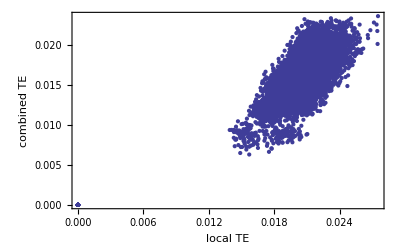

```mathematica
Clear[ii,jj];ListPlot[Flatten[Table[{adjAtest⟦ii,jj⟧,adjAtest2⟦ii,jj⟧},{ii,size/.pars},{jj,size/.pars}],1],FrameLabel->{"local TE","combined TE"},PlotRange->Automatic]
```

```mathematica
SetDirectory@basedir;globaltransferentropy=<<"~/Desktop/Doktorarbeit/Imaging/transferentropy/output/transferentropy_global.mx";
```

```mathematica
SetDirectory@basedir;maximatransferentropy=<<"~/Desktop/Doktorarbeit/Imaging/transferentropy/output/transferentropy_maxima.mx";
```

```mathematica
Clear[ii,jj];
ListPlot[Flatten[Table[{adjAtransferentropy⟦ii,jj⟧,adjAtest⟦ii,jj⟧},{ii,size/.pars},{jj,size/.pars}],1],FrameLabel->{"fitted weight","variance reduction (0,0)"}]
ListPlot[Flatten[Table[{adjAtransferentropy⟦ii,jj⟧,adjAtest2⟦ii,jj⟧},{ii,size/.pars},{jj,size/.pars}],1],FrameLabel->{"fitted weight","variance reduction (1,1)"}]
ListPlot[Flatten[Table[{adjAtest2⟦ii,jj⟧,adjAtest3⟦ii,jj⟧},{ii,size/.pars},{jj,size/.pars}],1],FrameLabel->{"variance reduction (0,0)","variance reduction (1,1)"}]
```

```mathematica
BarChart[Table[Total@Flatten@adjAtest⟦All,All,kk⟧,{kk,1,20}],Frame->True,FrameLabel->{"bin","total TE contribution"},PlotLabel->"all connections"]
```

```mathematica
TElinked=TEnotlinked=TElinkedUnidir=TElinkedBidir=Table[0,{20}];
For[source=1,source≤size/.pars,source++,
For[target=1,target≤size/.pars,target++,
If[MemberQ[GetConnections@adjA,{source,target}],
TElinked+=adjAtest⟦source,target⟧;
If[MemberQ[GetConnections@adjA,{target,source}],
TElinkedBidir+=adjAtest⟦source,target⟧;
,
TElinkedUnidir+=adjAtest⟦source,target⟧;
];
,
TEnotlinked+=adjAtest⟦source,target⟧;
];
];
];
Clear[source,target];
```

```mathematica
BarChart[Table[Total@Flatten@adjAtest⟦All,All,kk⟧,{kk,1,20}],FrameLabel->{"bin","total TE contribution"},PlotLabel->"all connections"]
BarChart[TElinked,Frame->True,FrameLabel->{"bin","total TE contribution"},PlotLabel->"linked"]
BarChart[TEnotlinked,Frame->True,FrameLabel->{"bin","total TE contribution"},PlotLabel->"not linked"]
BarChart[TElinkedUnidir,Frame->True,FrameLabel->{"bin","total TE contribution"},PlotLabel->"linked (uni-directional)"]
BarChart[TElinkedBidir,Frame->True,FrameLabel->{"bin","total TE contribution"},PlotLabel->"linked (bi-directional)"]
```

### compare adjacency matrix directly

```mathematica
ArrayPlot[adjA,ColorFunction->"AvocadoColors"]
ArrayPlot[adjAtest2,ColorFunction->"AvocadoColors"]
(* ArrayPlot[maximatransferentropy,ColorFunction->"AvocadoColors"] *)
```

{m→-0.0012449,b→0.00446494}

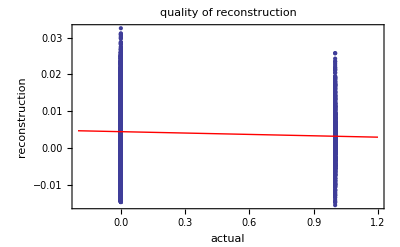

-0.0523861

```mathematica
(* compare single entries, 1st order *)
xdata=Drop[Sort@Flatten[Table[{adjA⟦ii,jj⟧,adjAtest⟦ii,jj⟧},{ii,Length@adjA},{jj,Length@adjA}],1],Length@adjA];
xfit=FindFit[xdata,m x+b,{m,b},x]
xplot={ListPlot[xdata,PlotRange->All],Plot[(m x+b)/.xfit,{x,-0.2,1.2},PlotStyle->Red]};
Show[xplot,FrameLabel->{"actual","reconstruction"},PlotLabel->"quality of reconstruction"]
Correlation[xdata⟦All,1⟧,xdata⟦All,2⟧]
Clear[ii,jj,m,x,b,xfit,xplot];
```

```mathematica
SetupCorAdjA:=Module[{xx,ii,jj},
xAdjAcor=Table[0,{size*(size-1)/.pars}];
xx=0;
For[ii=1,ii≤size/.pars,ii++,
For[jj=1,jj≤size/.pars,jj++,
If[ii≠jj,xAdjAcor⟦++xx⟧=adjA⟦ii,jj⟧];
];
]];
```

```mathematica
FindCorAdjA[adjAtest_]:=Module[{ii,jj,xx=0,xcorResult},
xcorResult=Table[0,{size*(size-1)/.pars}];
For[ii=1,ii≤size/.pars,ii++,
For[jj=1,jj≤size/.pars,jj++,
If[ii≠jj,xcorResult⟦++xx⟧=adjAtest⟦ii,jj⟧];
];
];

Correlation[xAdjAcor,xcorResult]
];
```

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/NoiseFPSnew";
```

```mathematica
SetDirectory@basedir;
tauFs={0,0,0,0,350001,291667,250001,218751,194445,175001,159091,145834,134616,125001,116667,109376,102942,97223,92106,87501,83334,79546,76087,72917,70001,67308,64815,62501,60345,58334};
qualityA=Table[0,{11},{11}];
For[i=0,i≤110,i++,
xtemp=<<("adjA_iteration"<>ToString@i<>".mx");
xpars=<<("pars_iteration"<>ToString@i<>".mx");
(* Print[ToString@Round@(noise/.xpars)/0.03<>" und "<>ToString[(First@First@Position[tauFs,samples/.xpars]-5)/2]]; *)
qualityA⟦1+Round@((noise/.xpars)/0.03),1+(First@First@Position[tauFs,samples/.xpars]-5)/2⟧=FindCorAdjA[xtemp];
];
```

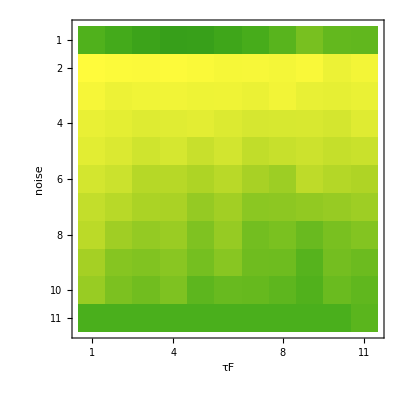

```mathematica
MatrixPlot[qualityA,ColorFunction->"AvocadoColors",FrameLabel->{"noise","τF"}]
```

### generate ROC curves (old functions)

```mathematica
GenerateROC[xadjA_]:=GenerateROC[xadjA,100];
GenerateROC[xadjA_,xsteps_]:=Module[{xdata,xx,t,xmin,xmax,xstepsize,xP,xTP,xN,xFP,xROCpoints},
xROCpoints=Table[{0,0},{xsteps+1}];
(* compare single entries, 1st order *)
xdata=DeleteCases[Sort@Flatten[Table[If[ii≠jj,{adjA⟦ii,jj⟧,xadjA⟦ii,jj⟧},{"nix"}],{ii,Length@adjA},{jj,Length@adjA}],1],{"nix"}];
(* test if exactly the diagonal elements have been deleted *)
If[Length@xdata!=Length@adjA*(Length[adjA]-1),Print["Warning: length="<>ToString@Length@xdata];];

xmin=Min@Last@Transpose@xdata;
xmax=Max@Last@Transpose@xdata;
xstepsize=(xmax-xmin)/xsteps;
If[xstepsize<10^-9,Abort[]];
(* go through all possible threshold values and compute the ROC data points *)
For[t=0,t≤xsteps,t++,
xx=xmin+t*xstepsize;
(*ShowStatus["xx="<>ToString@xx];*)
xP=Length@Cases[xdata,{1,_}];
xTP=Length@Cases[xdata,{1,_?((#>xx)&)}];
xN=Length@Cases[xdata,{0,_}];
xFP=Length@Cases[xdata,{0,_?((#>xx)&)}];
xROCpoints⟦t+1⟧=N@{xFP/xN,xTP/xP};
];

xROCpoints
];
```

```mathematica
GenerateROCfn[xdata_,fraction_]:=Module[{xx,xP,xTP,xN,xFP,xROCpointsLocal,middle},
(* go through all possible threshold values and compute the ROC data points *)
xx=Min@Flatten@xdata+(Max@Flatten@xdata-Min@Flatten@xdata)*fraction;
xP=Length@Cases[xdata,{1,_}];
xTP=Length@Cases[xdata,{1,_?((#>xx)&)}];
xN=Length@Cases[xdata,{0,_}];
xFP=Length@Cases[xdata,{0,_?((#>xx)&)}];
N@{xFP/xN,xTP/xP}
];
x2Data[xadjA_]:=Module[{ii,jj,xdata},
xdata=DeleteCases[Sort@Flatten[Table[If[ii≠jj,{adjA⟦ii,jj⟧,xadjA⟦ii,jj⟧},{"nix"}],{ii,Length@adjA},{jj,Length@adjA}],1],{"nix"}];
(* test if exactly the diagonal elements have been deleted *)
If[Length@xdata!=Length@adjA*(Length[adjA]-1),Print["Warning: length="<>ToString@Length@xdata]];
xdata
];
```

```mathematica
SetDirectory@basedir;
xROClist={};
For[i=0,i≤3,i++,
xtemp=<<("adjA_iteration"<>ToString[i]<>".mx");
(*xpars=<<("pars_iteration"<>ToString@i<>".mx");*)
ShowStatus["i = "<>ToString[i]<>"..."];
AppendTo[xROClist,GenerateROC@xtemp];
];
(*Print[Length@xROClist];*)
ShowStatus["done."];
Clear[i,xtemp,xpars];
```

### generate ROC curves (adaptive functions)

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/granger-sim/Paris/SatNoise";
SetDirectory@basedir;
```

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/Paris/2DbinningCondSatNoise/Leogang";
SetDirectory@basedir;
```

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/0815B-GEI/2DCond";
SetDirectory@basedir;
```

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/VectorPlotReplicateTest";
SetDirectory@basedir;
```

```mathematica
importlist2=(Get["adjA_iteration"<>ToString@#<>".mx"]⟦All,All,1⟧&/@Range[1,4]);
```

```mathematica
xindex=0;
importlist=<<("adjA_iteration"<>ToString@xindex<>".mx");
parsstring=<<("pars_iteration"<>ToString@xindex<>".mx");
importlist2=Table[importlist⟦All,All,ii⟧,{ii,Last@Dimensions@importlist}];
Clear[importlist,xindex];
```

```mathematica
xindex=1;
importlist2=<<("adjA_iteration"<>ToString@xindex<>".mx");
parsstring=<<("pars_iteration"<>ToString@xindex<>".mx");
Clear[importlist,xindex];
```

```mathematica
parsstring
```

{iteration→1,size→100,bins→255,samples→359951,inputscaling→0.51,cutoff→-1,p→1,noise→0.03,tauF→20,saturation→300,DetrendTimeSeriesQ→0,OverrideRescalingQ→0,HighPassFilterQ→1,inputfile→../../Simulationen/NEST/calciumbursts2/Paris/LeogangTopology/noisefree_rawCalcium_uchar_20ms.dat,outputfile→Paris/SatNoise/adjA_iteration1.mx}

```mathematica
ArrayPlot[Total@importlist2,ColorFunction->"AvocadoColors",PlotLabel->"GTE: bins & globalbins: 15"]
```

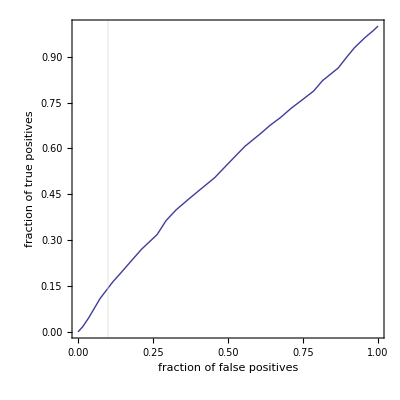

```mathematica
ListPlot[GenerateROCsmart@importlist2,Joined->True,GridLines->{{0.1},{}},Axes->False,AspectRatio->1,FrameLabel->{"fraction of false positives","fraction of true positives"},PlotLabel->"",PlotRange->All]
```

```mathematica
xtempindex=11*20+3
Print[xtemp=<<("pars_iteration"<>ToString@xtempindex<>".mx")];
Print["local bins: ",bins/.xtemp];
Print["global bins: ",globalbins/.xtemp];
Print["conditioning level: ",GlobalConditioningLevel/.xtemp];
```

```mathematica
ListPlot[{Transpose@{Flatten[importlistMO1⟦1⟧],Flatten[importlistMO2⟦1⟧]},Transpose@{Flatten[importlistMO1⟦1⟧*adjA],Flatten[importlistMO2⟦1⟧*adjA]}},FrameLabel->{"TE order 1","TE order 2"},AspectRatio->1,PlotLabel->"globalbin 1"]
ListPlot[{Transpose@{Flatten[importlistMO1⟦2⟧],Flatten[importlistMO2⟦2⟧]},Transpose@{Flatten[importlistMO1⟦2⟧*adjA],Flatten[importlistMO2⟦2⟧*adjA]}},FrameLabel->{"TE order 1","TE order 2"},AspectRatio->1,PlotLabel->"globalbin 1"]
```

### evaluate single adjacency matrix regarding topological features

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/Paris/2DbinningCondSatNoise/Random";
SetDirectory@basedir;
```

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/Paris/2DbinningCondSatNoise/Leogang";
SetDirectory@basedir;
```

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/Olav0816A/2DConditioned";
SetDirectory@basedir;
```

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/0811B-GEI/2DbinningCond";
SetDirectory@basedir;
```

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/0815B-GEI/2DCond";
SetDirectory@basedir;
```

```mathematica
Clear[bins,globalbins,GlobalConditioningLevel];
```

```mathematica
xindex=346;
importlist=<<("adjA_iteration"<>ToString@xindex<>".mx");
parsstring=<<("pars_iteration"<>ToString@xindex<>".mx")
importlist2=Table[importlist⟦All,All,ii⟧,{ii,Last@Dimensions@importlist}];
xadjA=First@importlist2;
Clear[importlist,xindex];
```

{executable→teglobalsim,iteration→138,size→100,rawdatabins→255,bins→7,cutoff→-1,globalbins→2,samples→359951,p→1,noise→0.03,tauF→20,OverrideRescalingQ→0,HighPassFilterQ→1,InstantFeedbackTermQ→1,saturation→300,IncludeGlobalSignalQ→1,GenerateGlobalFromFilteredDataQ→0,GlobalConditioningLevel→0.225,inputfile→../../Simulationen/NEST/calciumbursts2/Paris/LeogangTopology/noisefree_rawCalcium_uchar_20ms.dat,outputfile→Paris/2DbinningCondSatNoise/Leogang/adjA_iteration346.mx,outputparsfile→Paris/2DbinningCondSatNoise/Leogang/pars_iteration346.mx,outputcrossvalfile→Paris/2DbinningCondSatNoise/Leogang/crossval_iteration346.mx}

```mathematica
xadjA:=xadjARnd;
```

```mathematica
xbins=25;
xconsfraction=0.1;
DataSetID="Leogang SatNoise";
QualityType="clustering index, cycle type, all entries";

xtempCycle2=MeasureQuality[ThresholdedFractionA[xadjA,xconsfraction],QualityType];
xtempCycle1=MeasureQuality[adjA,QualityType];
```

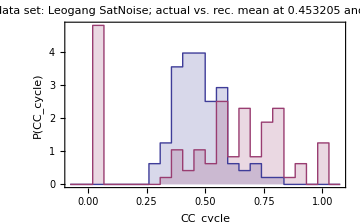

```mathematica
ListPlot[{FineHistogramP[xtempCycle1,xbins,xrange={-0.1,1.1}],FineHistogramP[xtempCycle2,xbins,xrange]},Joined->True,PlotRange->All,FrameLabel->{"CC_cycle","P(CC_cycle)"},PlotLabel->"data set: "<>DataSetID<>"; actual vs. rec.\nmean at "<>ToString[N@Mean@xtempCycle1]<>" and "<>ToString[N@Mean@xtempCycle2],ImageSize->Medium,InterpolationOrder->0,Filling->0]
```

```mathematica
xbins=25;
xconsfraction=0.1;
DataSetID="Leogang SatNoise";
QualityType="undirected clustering index, all entries";

xtempCycle2=MeasureQuality[ThresholdedFractionA[xadjA,xconsfraction],QualityType];
xtempCycle1=MeasureQuality[adjA,QualityType];
```

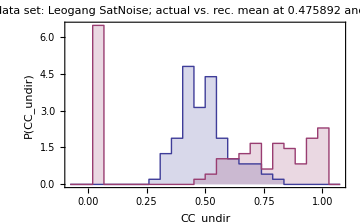

```mathematica
ListPlot[{FineHistogramP[xtempCycle1,xbins,xrange={-0.1,1.1}],FineHistogramP[xtempCycle2,xbins,xrange]},Joined->True,PlotRange->All,FrameLabel->{"CC_undir","P(CC_undir)"},PlotLabel->"data set: "<>DataSetID<>"; actual vs. rec.\nmean at "<>ToString[N@Mean@xtempCycle1]<>" and "<>ToString[N@Mean@xtempCycle2],ImageSize->Medium,InterpolationOrder->0,Filling->0]
```

```mathematica
xbins=30;
xconsfraction=0.1;
DataSetID="Leogang SatNoise";
QualityType="in-degree, all entries";
(*QualityType="clustering index, full type, all entries";*)

xtempkin2=MeasureQuality[ThresholdedFractionA[xadjA,xconsfraction],QualityType];
xtempkin1=MeasureQuality[adjA,QualityType];
```

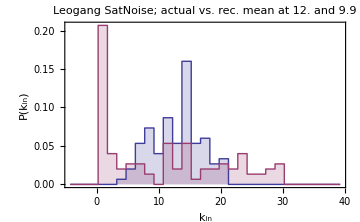

```mathematica
ListPlot[{FineHistogramP[xtempkin1,xbins,xrange={-5,40}],FineHistogramP[xtempkin2,xbins,xrange]},Joined->True,PlotRange->All,FrameLabel->{"k_in","P(k_in)"},PlotLabel->DataSetID<>"; actual vs. rec.\nmean at "<>ToString[N@Mean@xtempkin1]<>" and "<>ToString[N@Mean@xtempkin2],ImageSize->Medium,InterpolationOrder->0,Filling->0]
```

```mathematica
xbins=30;
xconsfraction=0.1;
DataSetID="Leogang SatNoise";
QualityType="out-degree, all entries";
(*QualityType="clustering index, full type, all entries";*)

xtempkout2=MeasureQuality[ThresholdedFractionA[xadjA,xconsfraction],QualityType];
xtempkout1=MeasureQuality[adjA,QualityType];
```

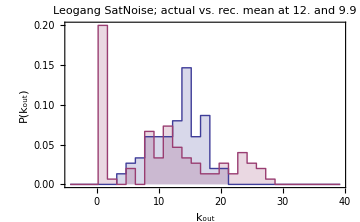

```mathematica
ListPlot[{FineHistogramP[xtempkout1,xbins,xrange={-5,40}],FineHistogramP[xtempkout2,xbins,xrange]},Joined->True,PlotRange->All,FrameLabel->{"k_out","P(k_out)"},PlotLabel->DataSetID<>"; actual vs. rec.\nmean at "<>ToString[N@Mean@xtempkout1]<>" and "<>ToString[N@Mean@xtempkout2],ImageSize->Medium,InterpolationOrder->0,Filling->0]
```

```mathematica
xbins=40;
xconsfraction=0.1;
DataSetID="Leogang SatNoise";

xtempddistr2=DistanceDistributionInNetwork[ThresholdedFractionA[xadjA,xconsfraction],pos];
xtempddistr1=DistanceDistributionInNetwork[adjA,pos];
```

```mathematica
DistanceDistributionInNetwork[xadjA_,poslist_]:=Module[{cfrom,cto,count,result={},xSelectA},
For[cfrom=1,cfrom≤Length@xadjA,cfrom++,
For[cto=1,cto≤Length@xadjA,cto++,
If[(cfrom≠cto)&&(xadjA⟦cfrom,cto⟧==1),
AppendTo[result,N@Norm[poslist⟦cfrom⟧-poslist⟦cto⟧]];
]
]];
(* Print[count,", fractional ",N@count/(size(size-1)/.pars)]; *)
Return[result];
];
```

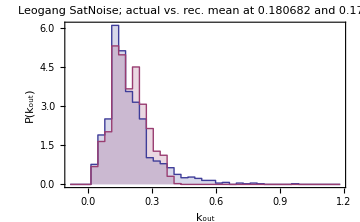

```mathematica
ListPlot[{FineHistogramP[xtempddistr1,xbins,xrange={-0.1,1.2}],FineHistogramP[xtempddistr2,xbins,xrange]},Joined->True,PlotRange->All,FrameLabel->{"k_out","P(k_out)"},PlotLabel->DataSetID<>"; actual vs. rec.\nmean at "<>ToString[N@Mean@xtempddistr1]<>" and "<>ToString[N@Mean@xtempddistr2],ImageSize->Medium,InterpolationOrder->0,Filling->0]
```

#### identify reconstructed core to compare topological indices to

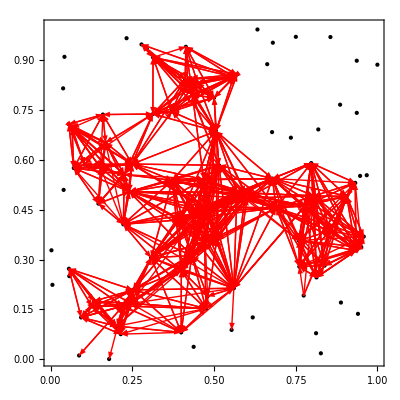

```mathematica
PlotVectorGraph[pos,xadjAtemp=ThresholdedFractionA[xadjA,0.1],""]
```

```mathematica
xtemp=(If[Total@#>3,1,0]&/@xadjAtemp);
CoreNodesList=Flatten@Position[xtemp,1]
```

{2,3,4,7,8,10,11,12,14,15,17,18,21,25,26,27,28,29,30,31,32,33,34,35,36,37,38,40,42,43,46,47,48,49,51,52,53,54,56,57,58,60,61,62,63,65,66,67,68,70,71,72,73,75,76,77,78,79,80,82,83,84,85,90,91,92,95,99,100}

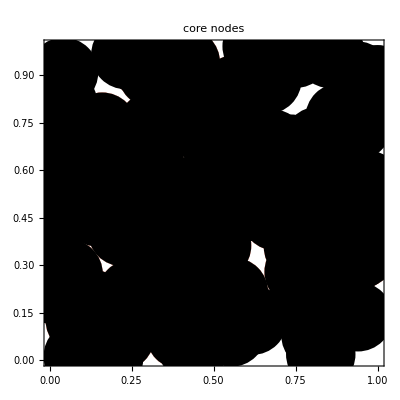

```mathematica
ListPlot[{pos⟦CoreNodesList⟧,pos⟦CoreNodesList⟧,pos},AspectRatio->1,PlotLabel->"core nodes",PlotStyle->{Directive[RGBColor[1,0.3,0.3],PointSize[xtemp=0.16],Opacity[1]],Directive[RGBColor[1,0.9,0.8],PointSize[xtemp-0.01],Opacity[1]],Directive[Black,PointSize[Large]]}]
```

```mathematica
adjAReduced=adjA⟦CoreNodesList,CoreNodesList⟧;
xadjAReduced=xadjA⟦CoreNodesList,CoreNodesList⟧;
posReduced=pos⟦CoreNodesList⟧;
Dimensions@xadjAReduced
```

{69,69}

```mathematica
Total@Flatten@#&/@{adjA,adjAReduced}
Total@Flatten@#&/@{xadjAtemp,xadjAtemp⟦CoreNodesList,CoreNodesList⟧}
```

{1200,819}

{990,986}

```mathematica
PlotVectorGraph[posReduced,xadjAtemp⟦CoreNodesList,CoreNodesList⟧,"core nodes with their (rec.) connections"]
```

```mathematica
xbins=25;
xconsfraction=0.1;
DataSetID="Leogang SatNoise (reduced)";
QualityType="clustering index, cycle type, all entries";

xtempCycle1=MeasureQuality[adjAReduced,QualityType];(*xtempCycle2=MeasureQuality[ThresholdedFractionA[xadjAReduced,xconsfraction],QualityType];*)
xtempCycle2=MeasureQuality[xadjAtemp⟦CoreNodesList,CoreNodesList⟧,QualityType];
```

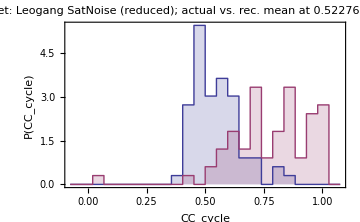

```mathematica
ListPlot[{FineHistogramP[xtempCycle1,xbins,xrange={-0.1,1.1}],FineHistogramP[xtempCycle2,xbins,xrange]},Joined->True,PlotRange->All,FrameLabel->{"CC_cycle","P(CC_cycle)"},PlotLabel->"data set: "<>DataSetID<>"; actual vs. rec.\nmean at "<>ToString[N@Mean@xtempCycle1]<>" and "<>ToString[N@Mean@xtempCycle2],ImageSize->Medium,InterpolationOrder->0,Filling->0]
```

```mathematica
xbins=25;
xconsfraction=0.1;
DataSetID="Leogang SatNoise (reduced)";
QualityType="undirected clustering index, all entries";

xtempCycle1=MeasureQuality[adjAReduced,QualityType];(*xtempCycle2=MeasureQuality[ThresholdedFractionA[xadjAReduced,xconsfraction],QualityType];*)
xtempCycle2=MeasureQuality[xadjAtemp⟦CoreNodesList,CoreNodesList⟧,QualityType];
```

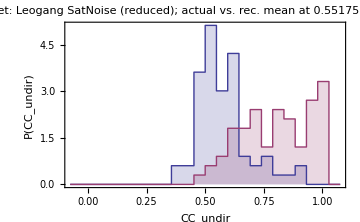

```mathematica
ListPlot[{FineHistogramP[xtempCycle1,xbins,xrange={-0.1,1.1}],FineHistogramP[xtempCycle2,xbins,xrange]},Joined->True,PlotRange->All,FrameLabel->{"CC_undir","P(CC_undir)"},PlotLabel->"data set: "<>DataSetID<>"; actual vs. rec.\nmean at "<>ToString[N@Mean@xtempCycle1]<>" and "<>ToString[N@Mean@xtempCycle2],ImageSize->Medium,InterpolationOrder->0,Filling->0]
```

```mathematica
xbins=20;
xconsfraction=0.1;
DataSetID="Leogang SatNoise";
QualityType="in-degree, all entries";
(*QualityType="clustering index, full type, all entries";*)

xtempkin2=MeasureQuality[xadjAtemp⟦CoreNodesList,CoreNodesList⟧,QualityType];
xtempkin1=MeasureQuality[adjAReduced,QualityType];
```

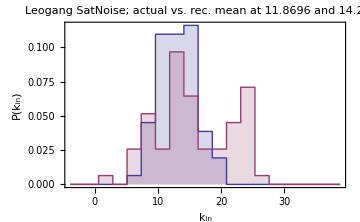

```mathematica
ListPlot[{FineHistogramP[xtempkin1,xbins,xrange={-5,40}],FineHistogramP[xtempkin2,xbins,xrange]},Joined->True,PlotRange->All,FrameLabel->{"k_in","P(k_in)"},PlotLabel->DataSetID<>"; actual vs. rec.\nmean at "<>ToString[N@Mean@xtempkin1]<>" and "<>ToString[N@Mean@xtempkin2],ImageSize->Medium,InterpolationOrder->0,Filling->0]
```

### generate 3D plots of ROC curves

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/Paris/NoiseLevelTest/LeogangNoSatCTE";
SetDirectory@basedir;
```

```mathematica
xindexlist=Range[0,20];
importlist=(<<("adjA_iteration"<>ToString@#<>".mx")&/@xindexlist);
importlist2=importlist⟦All,All,All,1⟧;
parslist=(<<("pars_iteration"<>ToString@#<>".mx")&/@xindexlist);
```

```mathematica
Dimensions@importlist
```

{21,100,100,2}

```mathematica
xplotdata=GenerateROCsmart@importlist2;
xplotdata3D=Flatten[Table[Flatten[{noise/.parslist⟦ii⟧,#}]&/@xplotdata⟦ii⟧,{ii,Length@xplotdata}],1];
```

```mathematica
ListPlot[xplotdata,Joined->True,GridLines->{{0.1},{}},Axes->False,AspectRatio->1,FrameLabel->{"fraction of false positives","fraction of true positives"},PlotLabel->"GTE cond. to 60, no Sat + Noise, 5 bins, Leogang",PlotRange->All]
ListPlot3D[xplotdata3D,AspectRatio->1,AxesLabel->{"σ","FP","TP"},PlotRange->All,ColorFunction->"SunsetColors"]
```

```mathematica
ListPlot[xplotdata,Joined->True,GridLines->{{0.1},{}},Axes->False,AspectRatio->1,FrameLabel->{"fraction of false positives","fraction of true positives"},PlotLabel->"Local TE, no Sat + Noise, Leogang",PlotRange->All]
ListPlot3D[xplotdata3D,AspectRatio->1,AxesLabel->{"σ","FP","TP"},PlotRange->All,ColorFunction->"SunsetColors"]
```

```mathematica
ListPlot3D[xplotdata3D,AspectRatio->1,AxesLabel->{"σ","FP","TP"},PlotRange->All,ColorFunction->"SunsetColors"]
```

```mathematica
TellMeWhatHappened@parslist
```

```mathematica
xtemp1=Table[If[cfrom≠cto,{adjA⟦cfrom,cto⟧,importlist2⟦cfrom,cto⟧},"nix"],{cfrom,size/.pars},{cto,size/.pars}];
xtemp2=Flatten[xtemp1,1];
xtemp3=DeleteCases[xtemp2,"nix"];
xplotdata=Last[Transpose@Cases[xtemp3,{#,_}]]&/@{0,1};
Clear[xtemp1,xtemp2,xtemp3];
```

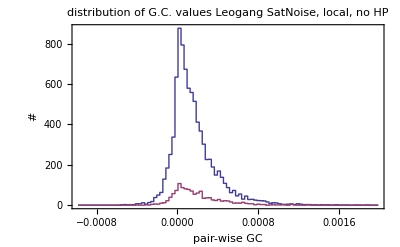

```mathematica
ListPlot[FineHistogram[#,100,{-0.001,0.002}]&/@xplotdata,Joined->True,PlotRange->All,FrameLabel->{"pair-wise GC","#"},InterpolationOrder->0,PlotLabel->"distribution of G.C. values\nLeogang SatNoise, local, no HP\n"]
```

## load and evaluate reconstruction in terms of directionality

```mathematica
Length@importlistMO1
adjAtest=importlistMO2⟦1⟧;
adjAtest/=Max@adjAtest;
```

2

```mathematica
RawDirectionalityIndex[adjAin_]:=Module[{xlist={},ii,jj,i2j,j2i,i2jrec,j2irec,adjAtest},
adjAtest=If[Max@adjAin>10^-9,adjAin/(Max@adjAin),adjAin];
xlist={};
For[ii=1,ii≤size/.pars,ii++,
For[jj=ii+1,jj≤size/.pars,jj++,
i2j=adjA⟦ii,jj⟧;
j2i=adjA⟦jj,ii⟧;
i2jrec=adjAtest⟦ii,jj⟧;
j2irec=adjAtest⟦jj,ii⟧;
AppendTo[xlist,{If[i2j+j2i>0,(i2j-j2i)/(i2j+j2i),0],If[i2jrec+j2irec>0,(i2jrec-j2irec)/(i2jrec+j2irec),0]}];
]];
xlist
];
```

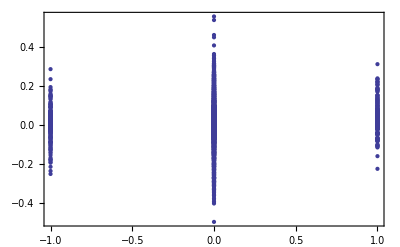

0.0418079

```mathematica
xlist=RawDirectionalityIndex@adjAtest;
ListPlot[xlist,PlotRange->All]
Correlation[First@Transpose@xlist,Second@Transpose@xlist]
```

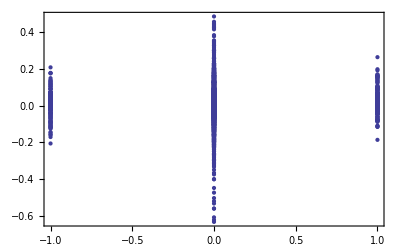

0.0220241

```mathematica
xlist=RawDirectionalityIndex@adjAtest;
ListPlot[xlist,PlotRange->All]
Correlation[First@Transpose@xlist,Second@Transpose@xlist]
```

```mathematica
Correlation@@Transpose@xlist
```

0.228458

```mathematica
GenerateHistogram3DData[adjA_,adjAtest_]:=Module[{i,j,index=1,tempresult,result},
result=Table[{},{(size^2-size)/2/.pars}];
For[i=1,i≤size/.pars,i++,
For[j=i+1,j≤size/.pars,j++,
Switch[DirID[adjA⟦i,j⟧,adjA⟦j,i⟧],
0,tempresult={{0,adjAtest⟦i,j⟧},{0,adjAtest⟦j,i⟧}};,
1,tempresult={{2,adjAtest⟦i,j⟧},{1,adjAtest⟦j,i⟧}};,
2,tempresult={{1,adjAtest⟦i,j⟧},{2,adjAtest⟦j,i⟧}};,
3,tempresult={{3,adjAtest⟦i,j⟧},{3,adjAtest⟦j,i⟧}};,
_,Abort[];
];
result⟦index⟧=tempresult;
index++;
]];
Flatten[result,1]
];
```

```mathematica
RefineViaDPISimple[xadjA_,xthresh_,factor_]:=RefineViaDPISimple[xadjA,xthresh,factor,factor];
RefineViaDPISimple[xadjA_,xthresh_,factorProxy_,factorIndirect_]:=Module[{nodeA,nodeB,nodeC,adjAbinary,modifiedA,changes=0,goodchanges=0},
adjAbinary=Map[If[#>xthresh,True,False]&,xadjA,{2}];
modifiedA=xadjA;

(* go through the triples exaustively *)
For[nodeA=1,nodeA≤size/.pars,nodeA++,
ShowStatus["RefineViaDPISimple: nodeA = "<>ToString@nodeA];
For[nodeB=1,nodeB≤size/.pars,nodeB++,

If[adjAbinary⟦nodeA,nodeB⟧,
For[nodeC=1,nodeC≤size/.pars,nodeC++,
(* if the nodes are really a triple *)
If[(nodeA≠nodeB)&&(nodeA≠nodeC)&&(nodeB≠nodeC),
(* examine AB - proxy motif *)
If[adjAbinary⟦nodeC,nodeA⟧&&adjAbinary⟦nodeC,nodeB⟧,
If[(xadjA⟦nodeC,nodeA⟧>xadjA⟦nodeA,nodeB⟧)&&(xadjA⟦nodeC,nodeB⟧>xadjA⟦nodeA,nodeB⟧),modifiedA⟦nodeA,nodeB⟧=modifiedA⟦nodeA,nodeB⟧*factorProxy;changes++;If[adjA⟦nodeA,nodeB⟧==0,goodchanges++];];
];
(* examine AB - indirect motif *)
If[adjAbinary⟦nodeA,nodeC⟧&&adjAbinary⟦nodeC,nodeB⟧,
If[(xadjA⟦nodeA,nodeC⟧>xadjA⟦nodeA,nodeB⟧)&&(xadjA⟦nodeC,nodeB⟧>xadjA⟦nodeA,nodeB⟧),modifiedA⟦nodeA,nodeB⟧*=factorIndirect;changes++;If[adjA⟦nodeA,nodeB⟧==0,goodchanges++];];
];
]]];

If[adjAbinary⟦nodeB,nodeA⟧,
For[nodeC=1,nodeC≤size/.pars,nodeC++,
(* if the nodes are really a triple *)
If[(nodeA≠nodeB)&&(nodeA≠nodeC)&&(nodeB≠nodeC),
(* examine BA - proxy motif *)
If[adjAbinary⟦nodeC,nodeA⟧&&adjAbinary⟦nodeC,nodeB⟧,
If[(xadjA⟦nodeC,nodeA⟧>xadjA⟦nodeB,nodeA⟧)&&(xadjA⟦nodeC,nodeB⟧>xadjA⟦nodeB,nodeA⟧),modifiedA⟦nodeB,nodeA⟧*=factorProxy;changes++;If[adjA⟦nodeB,nodeA⟧==0,goodchanges++];];
];
(* examine BA - indirect motif *)
If[adjAbinary⟦nodeC,nodeA⟧&&adjAbinary⟦nodeB,nodeC⟧,
If[(xadjA⟦nodeC,nodeA⟧>xadjA⟦nodeB,nodeA⟧)&&(xadjA⟦nodeB,nodeC⟧>xadjA⟦nodeB,nodeA⟧),modifiedA⟦nodeB,nodeA⟧*=factorIndirect;changes++;If[adjA⟦nodeB,nodeA⟧==0,goodchanges++];];
];
]]];

]];
Print["RefineViaDPISimple: ",changes," made, of which ",goodchanges," (",N@((100*goodchanges)/changes),"%) were correct."]; 
Return[modifiedA]
];
```

```mathematica
MarkViaDPISimple[xadjA_,xthresh_]:=Module[{nodeA,nodeB,nodeC,adjAbinary,modifiedA,changes=0,goodchanges=0},
adjAbinary=Map[If[#>xthresh,True,False]&,xadjA,{2}];
modifiedA=Table[0,{size/.pars},{size/.pars}];

(* go through the triples exaustively *)
For[nodeA=1,nodeA≤size/.pars,nodeA++,
ShowStatus["MarkViaDPISimple: nodeA = "<>ToString@nodeA];
For[nodeB=1,nodeB≤size/.pars,nodeB++,

If[adjAbinary⟦nodeA,nodeB⟧,
For[nodeC=1,nodeC≤size/.pars,nodeC++,
(* if the nodes are really a triple *)
If[(nodeA≠nodeB)&&(nodeA≠nodeC)&&(nodeB≠nodeC),
(* examine AB - proxy motif *)
If[adjAbinary⟦nodeC,nodeA⟧&&adjAbinary⟦nodeC,nodeB⟧,
If[(xadjA⟦nodeC,nodeA⟧>xadjA⟦nodeA,nodeB⟧)&&(xadjA⟦nodeC,nodeB⟧>xadjA⟦nodeA,nodeB⟧),modifiedA⟦nodeA,nodeB⟧--;changes++;If[adjA⟦nodeA,nodeB⟧==0,goodchanges++];];
];
(* examine AB - indirect motif *)
If[adjAbinary⟦nodeA,nodeC⟧&&adjAbinary⟦nodeC,nodeB⟧,
If[(xadjA⟦nodeA,nodeC⟧>xadjA⟦nodeA,nodeB⟧)&&(xadjA⟦nodeC,nodeB⟧>xadjA⟦nodeA,nodeB⟧),modifiedA⟦nodeA,nodeB⟧--;changes++;If[adjA⟦nodeA,nodeB⟧==0,goodchanges++];];
];
]]];

If[adjAbinary⟦nodeB,nodeA⟧,
For[nodeC=1,nodeC≤size/.pars,nodeC++,
(* if the nodes are really a triple *)
If[(nodeA≠nodeB)&&(nodeA≠nodeC)&&(nodeB≠nodeC),
(* examine BA - proxy motif *)
If[adjAbinary⟦nodeC,nodeA⟧&&adjAbinary⟦nodeC,nodeB⟧,
If[(xadjA⟦nodeC,nodeA⟧>xadjA⟦nodeB,nodeA⟧)&&(xadjA⟦nodeC,nodeB⟧>xadjA⟦nodeB,nodeA⟧),modifiedA⟦nodeB,nodeA⟧--;changes++;If[adjA⟦nodeB,nodeA⟧==0,goodchanges++];];
];
(* examine BA - indirect motif *)
If[adjAbinary⟦nodeC,nodeA⟧&&adjAbinary⟦nodeB,nodeC⟧,
If[(xadjA⟦nodeC,nodeA⟧>xadjA⟦nodeB,nodeA⟧)&&(xadjA⟦nodeB,nodeC⟧>xadjA⟦nodeB,nodeA⟧),modifiedA⟦nodeB,nodeA⟧--;changes++;If[adjA⟦nodeB,nodeA⟧==0,goodchanges++];];
];
]]];

]];
Print["MarkViaDPISimple: ",changes," made, of which ",goodchanges," (",N@((100*goodchanges)/changes),"%) were correct. (xtresh = ",xthresh,")"]; 
Return[modifiedA]
];
```

```mathematica
SumUpViaDPISimple[xadjA_,xthresh_]:=Module[{nodeA,nodeB,nodeC,adjAbinary,modifiedA,changes=0,goodchanges=0},
adjAbinary=Map[If[#>xthresh,True,False]&,xadjA,{2}];
modifiedA=Table[0,{size/.pars},{size/.pars}];

(* go through the triples exaustively *)
For[nodeA=1,nodeA≤size/.pars,nodeA++,
ShowStatus["SumUpViaDPISimple: nodeA = "<>ToString@nodeA];
For[nodeB=1,nodeB≤size/.pars,nodeB++,

If[adjAbinary⟦nodeA,nodeB⟧,
For[nodeC=1,nodeC≤size/.pars,nodeC++,
(* if the nodes are really a triple *)
If[(nodeA≠nodeB)&&(nodeA≠nodeC)&&(nodeB≠nodeC),
(* examine AB - proxy motif *)
If[adjAbinary⟦nodeC,nodeA⟧&&adjAbinary⟦nodeC,nodeB⟧,
If[(xadjA⟦nodeC,nodeA⟧>xadjA⟦nodeA,nodeB⟧)&&(xadjA⟦nodeC,nodeB⟧>xadjA⟦nodeA,nodeB⟧),modifiedA⟦nodeA,nodeB⟧-=(xadjA⟦nodeC,nodeA⟧+xadjA⟦nodeC,nodeB⟧)/2-xadjA⟦nodeA,nodeB⟧;changes++;If[adjA⟦nodeA,nodeB⟧==0,goodchanges++];];
];
(* examine AB - indirect motif *)
If[adjAbinary⟦nodeA,nodeC⟧&&adjAbinary⟦nodeC,nodeB⟧,
If[(xadjA⟦nodeA,nodeC⟧>xadjA⟦nodeA,nodeB⟧)&&(xadjA⟦nodeC,nodeB⟧>xadjA⟦nodeA,nodeB⟧),modifiedA⟦nodeA,nodeB⟧-=(xadjA⟦nodeA,nodeC⟧+xadjA⟦nodeC,nodeB⟧)/2-xadjA⟦nodeA,nodeB⟧;changes++;If[adjA⟦nodeA,nodeB⟧==0,goodchanges++];];
];
]]];

If[adjAbinary⟦nodeB,nodeA⟧,
For[nodeC=1,nodeC≤size/.pars,nodeC++,
(* if the nodes are really a triple *)
If[(nodeA≠nodeB)&&(nodeA≠nodeC)&&(nodeB≠nodeC),
(* examine BA - proxy motif *)
If[adjAbinary⟦nodeC,nodeA⟧&&adjAbinary⟦nodeC,nodeB⟧,
If[(xadjA⟦nodeC,nodeA⟧>xadjA⟦nodeB,nodeA⟧)&&(xadjA⟦nodeC,nodeB⟧>xadjA⟦nodeB,nodeA⟧),modifiedA⟦nodeB,nodeA⟧-=(xadjA⟦nodeC,nodeA⟧+xadjA⟦nodeC,nodeB⟧)/2-xadjA⟦nodeB,nodeA⟧;changes++;If[adjA⟦nodeB,nodeA⟧==0,goodchanges++];];
];
(* examine BA - indirect motif *)
If[adjAbinary⟦nodeC,nodeA⟧&&adjAbinary⟦nodeB,nodeC⟧,
If[(xadjA⟦nodeC,nodeA⟧>xadjA⟦nodeB,nodeA⟧)&&(xadjA⟦nodeB,nodeC⟧>xadjA⟦nodeB,nodeA⟧),modifiedA⟦nodeB,nodeA⟧-=(xadjA⟦nodeC,nodeA⟧+xadjA⟦nodeB,nodeC⟧)/2-xadjA⟦nodeB,nodeA⟧;changes++;If[adjA⟦nodeB,nodeA⟧==0,goodchanges++];];
];
]]];

]];
Print["SumUpViaDPISimple: ",changes," made, of which ",goodchanges," (",N@((100*goodchanges)/changes),"%) were correct. (xtresh = ",xthresh,")"]; 
Return[modifiedA]
];
```

```mathematica
Histogram3D[GenerateHistogram3DData[adjA,adjAtest],{{1},{0.02}},PlotRange->{0,300},ImageSize->Large,PlotLabel->"(Rnd, no DPI) 0: no link, 1: unidir wrong dir, 2: unidir right dir., 3: bidir"]
```

-Graphics3D-

```mathematica
Histogram3D[GenerateHistogram3DData[adjA,RefineViaDPISimple[adjAtest,0.05,0.95,1]],{{1},{0.02}},PlotRange->{0,300},ImageSize->Large,PlotLabel->"(Rnd with DPI, 0: no link, 1: unidir wrong dir, 2: unidir right dir., 3: bidir"]
```

RefineViaDPISimple: 34664 made, of which 23854 (68.8149%) were correct.

-Graphics3D-

```mathematica
xtest=MarkViaDPISimple[adjAtest,0.1];
```

MarkViaDPISimple: 16482 made, of which 8204 (49.7755%) were correct. (xtresh = 0.1)

```mathematica
xtest=SumUpViaDPISimple[adjAtest,0.1];
```

SumUpViaDPISimple: 16482 made, of which 8204 (49.7755%) were correct. (xtresh = 0.1)

```mathematica
xtest=SumUpViaDPISimple[adjAtest,0];
xtable=xnum={0,0,0,0};
xtableSimple=xnumSimple={0,0};

For[ii=1,ii≤size/.pars,ii++,
For[jj=1,jj≤size/.pars,jj++,
If[ii≠jj,
xnum⟦DirID[adjA⟦ii,jj⟧,adjA⟦jj,ii⟧]+1⟧++;
xtable⟦DirID[adjA⟦ii,jj⟧,adjA⟦jj,ii⟧]+1⟧+=xtest⟦ii,jj⟧;

xexist=adjA⟦ii,jj⟧;
xnumSimple⟦xexist+1⟧++;
xtableSimple⟦xexist+1⟧+=xtest⟦ii,jj⟧;
]]];
Clear[ii,jj,xexist];
Print["raw ",xtable,", mean ",N@(xtable/xnum)];

Print["raw ",xtableSimple,", mean ",N@(xtableSimple/xnumSimple)];
```

SumUpViaDPISimple: 1298398 made, of which 1261458 (97.155%) were correct. (xtresh = 0)

raw {-165135.,-3032.2,-5176.17,-3596.23}, mean {-19.8862,-7.65707,-13.0711,-4.47293}

raw {-170311.,-6628.44}, mean {-19.576,-5.5237}

```mathematica
(* generate directionality lindex list for original adjA *)
adjAdirlist={};
For[ii=1,ii≤size/.pars,ii++,
For[jj=ii+1,jj≤size/.pars,jj++,
i2j=adjA⟦ii,jj⟧;
j2i=adjA⟦jj,ii⟧;
AppendTo[adjAdirlist,If[i2j+j2i>0,(i2j-j2i)/(i2j+j2i),0]];
]];
Clear[ii,jj,i2j,j2i];
Length@adjAdirlist
```

4950

```mathematica
xMark=Abs@{-148.25553949903662,-40.71212121212121,-76.62626262626263,-25.893034825870647};
xSum=Abs@{-19.886236699502117,-7.657073828511361,-13.07113482645198,-4.472928002946291};
BarChart[xMark]
BarChart[xSum]
```

```mathematica
(#⟦3⟧)/(#⟦2⟧)&/@{xMark,xSum}
```

{1.88215,1.70707}

```mathematica
(* generate directionality indices to plot next to the ROC curve *)
xpoints=50;
adjAtestdirlist={{0,0},{1,0}};
xdata=DeleteCases[Sort@Flatten[Table[If[ii≠jj,{adjA⟦ii,jj⟧,adjAtest⟦ii,jj⟧},{"nix"}],{ii,Length@adjA},{jj,ii+1,Length@adjA}],1],{"nix"}];

For[step=1,step<xpoints-1,step++,
xfthresh=(N@step)/xpoints;
xlist={};
For[ii=1,ii≤size/.pars,ii++,
For[jj=ii+1,jj≤size/.pars,jj++,
i2jrec=If[adjAtest⟦ii,jj⟧>xfthresh,1.,0.];
j2irec=If[adjAtest⟦jj,ii⟧>xfthresh,1.,0.];
AppendTo[xlist,If[i2jrec+j2irec>0,(i2jrec-j2irec)/(i2jrec+j2irec),0]];
]];

AppendTo[adjAtestdirlist,{N@((Length@Cases[xdata,{0,_?((#>xfthresh)&)}])/(Length@Cases[xdata,{0,_}])),Correlation[adjAdirlist,xlist]}];
];
Clear[step,ii,jj,xdata];
```

```mathematica
adjAtestdirlist
```

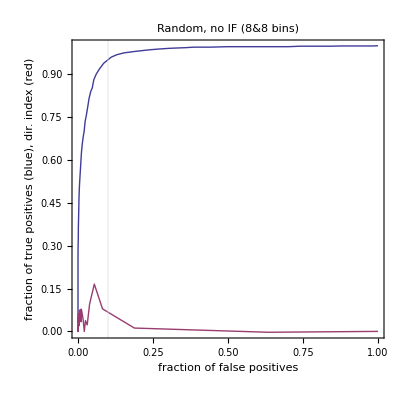

```mathematica
ListPlot[{GenerateROCsmart@adjAtest,Sort@adjAtestdirlist},Joined->True,GridLines->{{0.1},{}},Axes->False,AspectRatio->1,FrameLabel->{"fraction of false positives","fraction of true positives (blue), dir. index (red)"},PlotLabel->"Random, no IF (8&8 bins)",PlotRange->All]
```

#### examine directionality as a 2D plot (copied from below)

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/Paris/2Dbinning/Leogang";
SetDirectory@basedir;
```

```mathematica
xstarttime=AbsoluteTime[];
startii=0;
endii=399;
xdirlist=Table[0,{endii-startii+1}];
For[ii=startii,ii≤endii,ii++,
ShowStatus["ii = "<>ToString@ii<>", ETA "<>ETA[ii-startii,endii-startii,xstarttime]];
xadjA=Get["adjA_iteration"<>ToString@ii<>".mx"]⟦All,All,1⟧;
parsstring=Get["pars_iteration"<>ToString@ii<>".mx"];

templist=RawDirectionalityIndex@xadjA;

xdirlist⟦ii-startii+1⟧={bins/.parsstring,globalbins/.parsstring,If[Variance@Second@Transpose@templist>10^-9,Correlation@@Transpose@templist,0]};
];
ShowStatus["done."];
Clear[xstarttime,ii,startii,endii,parsstring,xadjA];
```

```mathematica
(* save results *)
xdirlist>>"xdirlist.mx";
```

```mathematica
(* load results *)
xdirlist=<<"xdirlist.mx";
```

```mathematica
xdirlist
```

```mathematica
ListContourPlot[xdirlist,PlotLabel->"raw directionality index",ContourLabels->Automatic,Contours->Automatic,FrameLabel->{"localbins","globalbins"}]
```

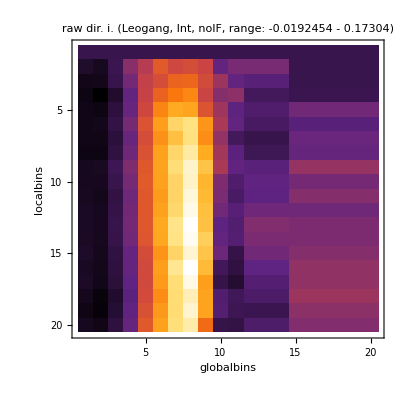

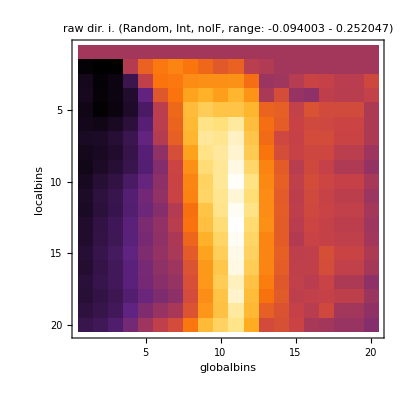

```mathematica
(* generate arrayplot from the data above, assuming we start at 1 *)
xmax=Max@xdirlist⟦All,1⟧;
ymax=Max@xdirlist⟦All,1⟧;
xdirlist2D=Table[0,{xmax},{ymax}];
(xdirlist2D⟦First@#,Second@#⟧=Third@#)&/@xdirlist;

ArrayPlot[xdirlist2D,ColorFunction->"SunsetColors",FrameLabel->{"localbins","globalbins"},PlotLabel->"raw dir. i. (Leogang, Int, noIF, range: "<>ToString@Min@xdirlist2D<>" - "<>ToString@Max@xdirlist2D<>")",FrameTicks->Automatic]
```

```mathematica
(* examine directionality not with index, but with probabilities *)
DirID[i2j_,j2i_]:=Module[{result=-1},
Switch[{i2j,j2i},
{0,0},result=0,
{1,0},result=1,
{0,1},result=2,
{1,1},result=3,
_,Print["DirID: Invalid input indices!"];Abort[];
];
result
];

ProbDirectionalityIndices[adjAtest_,thresh_]:=Module[{ii,jj,i2j,j2i,i2jrec,j2irec,result},
result=Table[0,{4},{4}];
For[ii=1,ii≤size/.pars,ii++,
For[jj=ii+1,jj≤size/.pars,jj++,
i2j=adjA⟦ii,jj⟧;
j2i=adjA⟦jj,ii⟧;
i2jrec=If[adjAtest⟦ii,jj⟧>thresh,1,0];
j2irec=If[adjAtest⟦jj,ii⟧>thresh,1,0];
result⟦DirID[i2j,j2i]+1,DirID[i2jrec,j2irec]+1⟧++;
]];
result
];
```

```mathematica
InterestingDirs[adjAtest_,thresh_]:=Module[{xtest,nrIsNo,nrIsUni,nrIsBi=0,adjAcons},
adjAcons=GetConnections@adjA;
If[MemberQ[adjAcons,{Second@#,First@#}],nrIsBi++]&/@adjAcons;
nrIsBi/=2;
nrIsUni=Length@adjAcons-(2 nrIsBi);
nrIsNo=((size/.pars)^2-(size/.pars))/2-nrIsBi-nrIsUni;
ShowStatus["InterestingDirs: nrIsNo="<>ToString@nrIsNo<>", nrIsUni="<>ToString@nrIsUni<>", nrIsBi="<>ToString@nrIsBi];
xtest=ProbDirectionalityIndices[adjAtest,thresh];
N@{xtest⟦1,1⟧/nrIsNo,(xtest⟦1,2⟧+xtest⟦1,3⟧)/nrIsNo,xtest⟦1,4⟧/nrIsNo,(xtest⟦2,1⟧+xtest⟦3,1⟧)/nrIsUni,(xtest⟦2,3⟧+xtest⟦3,2⟧)/nrIsUni,(xtest⟦2,2⟧+xtest⟦3,3⟧)/nrIsUni,(xtest⟦2,4⟧+xtest⟦3,4⟧)/nrIsUni,xtest⟦4,4⟧/nrIsBi,(xtest⟦4,2⟧+xtest⟦4,3⟧)/nrIsBi,xtest⟦4,1⟧/nrIsBi}
];
```

```mathematica
xtest=Table[Flatten@{xt,InterestingDirs[adjAtest,xt]},{xt,0,1,0.01}];
```

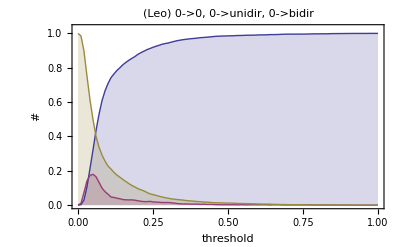

```mathematica
prefix="(Leo)";
ListPlot[Table[xtest⟦All,{1,index}⟧,{index,2,4,1}],Joined->True,Filling->0,PlotRange->{0,1.03},PlotLabel->prefix<>" 0->0, 0->unidir, 0->bidir",FrameLabel->{"threshold","#"}]
ListPlot[Table[xtest⟦All,{1,index}⟧,{index,5,8,1}],Joined->True,Filling->0,PlotRange->{0,1.03},PlotLabel->prefix<>" unidir->0, unidir falschrum, unidir richtig, unidir->bidir",FrameLabel->{"threshold","#"}]
ListPlot[Table[xtest⟦All,{1,index}⟧,{index,9,11,1}],Joined->True,Filling->0,PlotRange->{0,1.03},PlotLabel->prefix<>" bidir->bidir, bidir->unidir, bidir->0",FrameLabel->{"threshold","#"}]
```

## examine which connections the reconstruction captures well

```mathematica
Length@importlist2
adjAtest=importlist2⟦1⟧;
adjAtest/=Max@adjAtest;
```

4

```mathematica
ListPlot[GenerateROCsmartVector[adjA⟦All,#⟧,adjAtest⟦All,#⟧]&/@Range[1,100],Joined->True,GridLines->{{0.1},{}},Axes->False,AspectRatio->1,FrameLabel->{"fraction of false positives","fraction of true positives"},PlotLabel->"SGTE for 1 node, (1st in-shell)",PlotRange->All]
ListPlot[GenerateROCsmartVector[adjA⟦#,All⟧,adjAtest⟦#,All⟧]&/@Range[1,100],Joined->True,GridLines->{{0.1},{}},Axes->False,AspectRatio->1,FrameLabel->{"fraction of false positives","fraction of true positives"},PlotLabel->"SGTE for 1 node, (1st out-shell)",PlotRange->All]
```

```mathematica
AUCin[adjAtest_,index_]:=NIntegrate[Interpolation[ReduceForInterpolation@GenerateROCsmartVector[adjA⟦All,index⟧,adjAtest⟦All,index⟧]][x],{x,0,1}];
AUCout[adjAtest_,index_]:=NIntegrate[Interpolation[ReduceForInterpolation@GenerateROCsmartVector[adjA⟦index,All⟧,adjAtest⟦index,All⟧]][x],{x,0,1}]
```

```mathematica
Histogram[2(AUCin[adjAtest,#]-0.5)&/@Range[1,size/.pars],FrameLabel->{"predictive power","#"},PlotLabel->"reconstruction of 1st in-shell",PlotRange->All]
Histogram[2(AUCout[adjAtest,#]-0.5)&/@Range[1,size/.pars],FrameLabel->{"predictive power","#"},PlotLabel->"reconstruction of 1st out-shell",PlotRange->All]
```

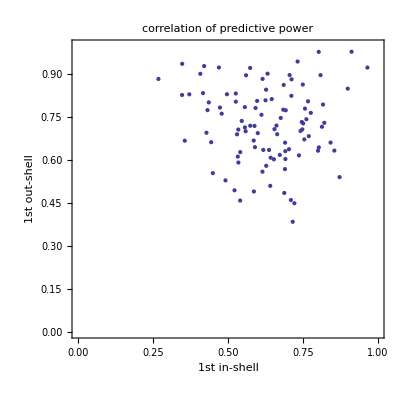

```mathematica
(* correlation of predictive power *)
ListPlot[Transpose@{2(AUCin[adjAtest,#]-0.5)&/@Range[1,size/.pars],2(AUCout[adjAtest,#]-0.5)&/@Range[1,size/.pars]},Axes->False,AspectRatio->1,FrameLabel->{"1st in-shell","1st out-shell"},PlotLabel->"correlation of predictive power",PlotRange->{{0,1},{0,1}}]
```

```mathematica
(* Test, ob man einfach künstlich "asymmetrisieren" kann *)
adjAtest2=adjAtest/Max@adjAtest;
For[ii=1,ii≤size/.pars,ii++,
xtempNoDiag=Drop[adjAtest⟦All,ii⟧,{ii}];
(* Print[Min@xtempNoDiag]; *)
adjAtest2⟦All,ii⟧=Insert[(xtempNoDiag-Min@xtempNoDiag)/(Max@xtempNoDiag-Min@xtempNoDiag)(**Max@xtempNoDiag*),0,ii];
adjAtest2⟦All,ii⟧=adjAtest2⟦All,ii⟧*UnitStep[adjAtest2⟦All,ii⟧];
];
Clear[xtempNoDiag];
```

```mathematica
adjAtest⟦1,1;;10⟧
adjAtest2⟦1,1;;10⟧
```

{0.,0.143883,0.110241,0.233184,0.108754,0.0881215,0.242168,0.169246,0.316345,0.268319}

{0,0.268249,0.672172,0.475721,0.204179,0.338066,0.272223,0.347512,0.410265,0.327009}

```mathematica
Histogram[adjAtest2⟦All,#⟧]&/@Range[4]
```

```mathematica
(* Test, die Asymmetrie pro Verbindung zu verstärken *)
xadjAlist={adjAtest};
For[amount=0.1,amount≤0.8,amount+=0.1,
adjAtemp=adjAtest;
For[ii=1,ii≤size/.pars,ii++,
For[jj=ii+1,jj≤size/.pars,jj++,
If[adjAtemp⟦ii,jj⟧>adjAtemp⟦jj,ii⟧,
adjAtemp⟦jj,ii⟧=adjAtemp⟦jj,ii⟧*(1-amount),adjAtemp⟦ii,jj⟧=adjAtemp⟦ii,jj⟧*(1-amount)
]
]]
AppendTo[xadjAlist,Evaluate@adjAtemp];
];
Clear[ii,jj,amount,adjAtemp];
```

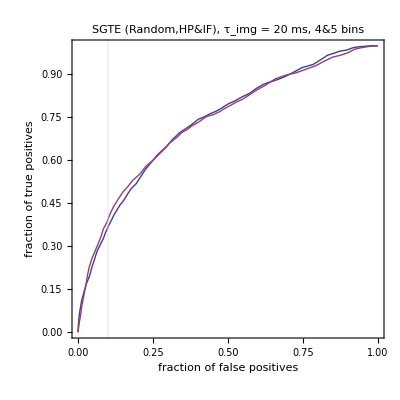

```mathematica
ListPlot[GenerateROCsmart/@{adjAtest,adjAtest2},Joined->True,GridLines->{{0.1},{}},Axes->False,AspectRatio->1,FrameLabel->{"fraction of false positives","fraction of true positives"},PlotLabel->"SGTE (Random,HP&IF), τ_img = 20 ms, 4&5 bins",PlotRange->All]
```

```mathematica
xmean=N@Mean@Flatten@DeleteCases[Flatten[Table[If[ii≠jj,adjAtest⟦ii,jj⟧,"nix"],{ii,Length@adjA},{jj,Length@adjA}],1],"nix"]

separationA={};
For[ii=1,ii≤size/.pars,ii++,
xin=inDegree@ii;
xout=outDegree@ii;
For[jj=1,jj≤size/.pars,jj++,
If[ii≠jj,
AppendTo[separationA,{xin,xout,adjAtest⟦ii,jj⟧/xmean}];
];
]];
Clear[ii,jj,xin,xout,xmean];
```

0.000238699

```mathematica
(* neues Maß *)
separationA={};
For[ii=1,ii≤size/.pars,ii++,
xin=inDegree@ii;
xout=outDegree@ii;

originalV=reconstructedV={};
For[jj=1,jj≤size/.pars,jj++,
If[ii≠jj,
AppendTo[originalV,adjA⟦ii,jj⟧];
AppendTo[reconstructedV,adjAtest⟦All,ii⟧];
];
];
AppendTo[separationA,{xin,xout,Correlation[originalV,reconstructedV]}];
];
```

```mathematica
Histogram[Table[inDegree[ii],{ii,size/.pars}],{1},PlotLabel->"distribution of in-degrees"]
Histogram[Table[outDegree[ii],{ii,size/.pars}],{1},PlotLabel->"distribution of out-degrees"]
```

```mathematica
ListPlot[(If[Length@#>0,Mean@Last@Transpose@#,1]&)/@Table[Cases[separationA,{xx,_,_}],{xx,0,25}],Joined->True,Filling->1,PlotRange->All,FrameLabel->{"k_in","avg. contrast"}]
ListPlot[(If[Length@#>0,Mean@Last@Transpose@#,1]&)/@Table[Cases[separationA,{_,xx,_}],{xx,0,25}],Joined->True,Filling->1,PlotRange->All,FrameLabel->{"k_out","avg. contrast"}]
```

```mathematica
ListPlot[(If[Length@#>0,Mean@Last@Transpose@#,0]&)/@Table[Cases[separationA,{xx,_,_}],{xx,0,25}],Joined->True,Filling->0,PlotRange->All,FrameLabel->{"k_in","avg. correlation"}]
ListPlot[(If[Length@#>0,Mean@Last@Transpose@#,0]&)/@Table[Cases[separationA,{_,xx,_}],{xx,0,25}],Joined->True,Filling->0,PlotRange->All,FrameLabel->{"k_out","avg. correlation"}]
Print[<<"pars_iteration0.mx"];
```

```mathematica
Union[outDegree/@Range[1,size/.pars]]
```

{4,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

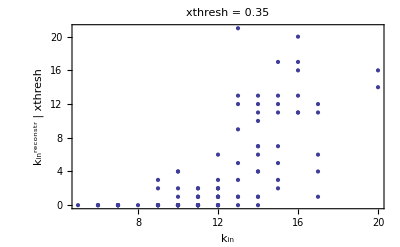

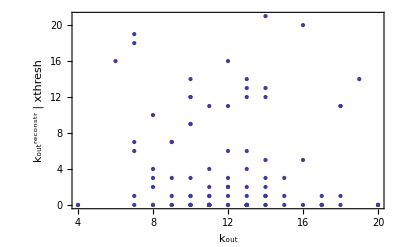

```mathematica
(* scatter plot à la Demian *)
xthresh = 0.35;

adjAtest-=Min@adjAtest;
adjAtest/=Max@adjAtest;

scatterAin=scatterAout={};
For[ii=1,ii≤size/.pars,ii++,
AppendTo[scatterAin,{inDegree@ii,Length@Cases[adjAtest⟦All,ii⟧,_?(#>xthresh&)]}];
AppendTo[scatterAout,{outDegree@ii,Length@Cases[adjAtest⟦ii,All⟧,_?(#>xthresh&)]}];
];

ListPlot[scatterAin,FrameLabel->{"k_in","k_in^reconstr | xthresh"},PlotRange->All,PlotLabel->"xthresh = "<>ToString@xthresh]
ListPlot[scatterAout,FrameLabel->{"k_out","k_out^reconstr | xthresh"},PlotRange->All]
Clear[ii];
```

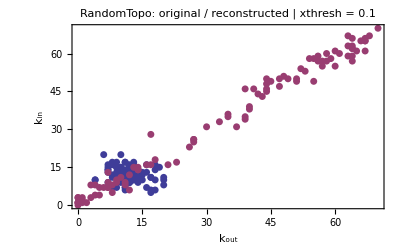

```mathematica
(* scatter plot à la Demian *)
xthresh = 0.1;

adjAtest-=Min@adjAtest; (* nonsense, because it includes diagonal elements *)
adjAtest/=Max@adjAtest;

scatterA=scatterArec={};
For[ii=1,ii≤size/.pars,ii++,
AppendTo[scatterArec,{Length@Cases[adjAtest⟦ii,All⟧,_?(#>xthresh&)],Length@Cases[adjAtest⟦All,ii⟧,_?(#>xthresh&)]}];
AppendTo[scatterA,{outDegree@ii,inDegree@ii}];
];

ListPlot[{scatterA,scatterArec},FrameLabel->{"k_out","k_in"},PlotRange->All,PlotLabel->"RandomTopo: original / reconstructed | xthresh = "<>ToString@xthresh,PlotStyle->AbsolutePointSize[5]]
Clear[ii];
```

```mathematica
(* scatter plot à la Demian + 3D feature *)
xthresh = 0.1;

adjAtest-=Min@adjAtest;
adjAtest/=Max@adjAtest;

scatterAin=scatterAout={};
For[ii=1,ii≤size/.pars,ii++,
AppendTo[scatterAin,{inDegree@ii,Length@Cases[adjAtest⟦All,ii⟧,_?(#>xthresh&)],((If[#>xthresh,1,0]&)/@adjAtest⟦All,ii⟧).adjA⟦All,ii⟧}];
AppendTo[scatterAout,{outDegree@ii,Length@Cases[adjAtest⟦ii,All⟧,_?(#>xthresh&)],((If[#>xthresh,1,0]&)/@adjAtest⟦ii,All⟧).adjA⟦ii,All⟧}];
];

ListContourPlot[scatterAin,PlotRange->All,PlotLabel->"xthresh = "<>ToString@xthresh,ContourLabels->All,FrameLabel->{"k_in","k_in^reconstr | xthresh"}]
ListContourPlot[scatterAout,PlotRange->All,ContourLabels->All,FrameLabel->{"k_out","k_out^reconstr | xthresh"}]
Clear[ii];
```

```mathematica
(* scatter plot à la Demian + 3D feature normiert *)
xthresh = 0.1;

adjAtest-=Min@adjAtest;
adjAtest/=Max@adjAtest;

scatterAin=scatterAout={};
For[ii=1,ii≤size/.pars,ii++,
AppendTo[scatterAin,{inDegree@ii,Length@Cases[adjAtest⟦All,ii⟧,_?(#>xthresh&)],(((If[#>xthresh,1,0]&)/@adjAtest⟦All,ii⟧).adjA⟦All,ii⟧)/(Length@Cases[GetConnections@adjA,{_,ii}])}];
AppendTo[scatterAout,{outDegree@ii,Length@Cases[adjAtest⟦ii,All⟧,_?(#>xthresh&)],(((If[#>xthresh,1,0]&)/@adjAtest⟦ii,All⟧).adjA⟦ii,All⟧)/(Length@Cases[GetConnections@adjA,{ii,_}])}];
];

ListContourPlot[scatterAin,PlotRange->All,PlotLabel->"fraction of true positives, xthresh = "<>ToString@xthresh,ContourLabels->All,FrameLabel->{"k_in","k_in^reconstr | xthresh"}]
ListContourPlot[scatterAout,PlotRange->All,ContourLabels->All,FrameLabel->{"k_out","k_out^reconstr | xthresh"}]
Clear[ii];
```

## create 2 D plots of the reconstruction quality (local & global binning)

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/Paris/2DbinningLaggedInt/Random";
SetDirectory@basedir;
```

```mathematica
startii=0;
endii=399;
xstarttime=AbsoluteTime[];
x10percentlist=AUClist=Table[{},{endii-startii+1}];
For[ii=startii,ii≤endii,ii++,
ShowStatus["ii = "<>ToString@ii<>", ETA "<>ETA[ii-startii,endii-startii+1,xstarttime]];
xadjA=Get["adjA_iteration"<>ToString@ii<>".mx"]⟦All,All,1⟧;
parsstring=Get["pars_iteration"<>ToString@ii<>".mx"];
fn=Interpolation[ReduceForInterpolation@N@GenerateROCsmart@xadjA,InterpolationOrder->1];

x10percentlist⟦ii-startii+1⟧={bins/.parsstring,globalbins/.parsstring,fn[0.1]};
AUClist⟦ii-startii+1⟧={bins/.parsstring,globalbins/.parsstring,NIntegrate[fn[x],{x,0,1}]};
];
ShowStatus["done."];
Clear[xstarttime,ii,startii,endii,parsstring,xadjA,fn,ROCpoints];
```

```mathematica
(* save results *)
x10percentlist>>"x10percentlist.mx";
AUClist>>"AUClist.mx";
```

```mathematica
(* load results *)
x10percentlist=<<"x10percentlist.mx";
AUClist=<<"AUClist.mx";
```

```mathematica
x10percentlist
AUClist
```

```mathematica
ListContourPlot[x10percentlist,PlotLabel->"TP rate at 10% FP (Random)",ContourLabels->Automatic,Contours->Automatic,FrameLabel->{"localbins","globalbins"}]
```

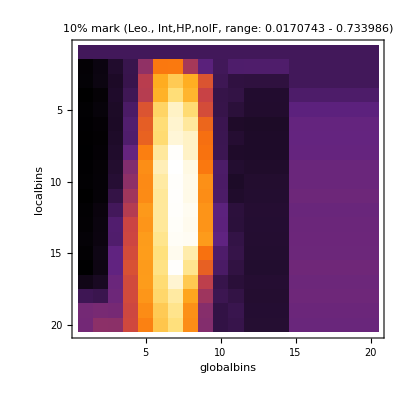

```mathematica
(* generate arrayplot from the data above, aussuming we start at 1 *)
xmax=Max@x10percentlist⟦All,1⟧;
ymax=Max@x10percentlist⟦All,1⟧;
x10percentlist2D=AUClist2D=Table[0,{xmax},{ymax}];
(x10percentlist2D⟦First@#,Second@#⟧=Third@#)&/@x10percentlist;
(AUClist2D⟦First@#,Second@#⟧=Third@#)&/@AUClist;

ArrayPlot[x10percentlist2D,ColorFunction->"SunsetColors",FrameLabel->{"localbins","globalbins"},PlotLabel->"10% mark (Leo., Int,HP,noIF, range: "<>ToString@Min@x10percentlist2D<>" - "<>ToString@Max@x10percentlist2D<>")",FrameTicks->Automatic]
ArrayPlot[AUClist2D,ColorFunction->"SunsetColors",FrameLabel->{"localbins","globalbins"},PlotLabel->"AUC (range: "<>ToString@Min@AUClist2D<>" - "<>ToString@Max@AUClist2D<>")",FrameTicks->Automatic]
Clear[xmax,ymax];
```

## create 2 D plots of the reconstruction quality (local binning & global conditioning)

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/Paris/2DbinningCondSatNoise10msExtended/Random";
SetDirectory@basedir;
```

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/Paris/LightScatter-Test/NoIF";
SetDirectory@basedir;
```

```mathematica
startii=0;
endii=399;
xstarttime=AbsoluteTime[];
x10percentlist=AUClist={};
For[ii=startii,ii≤endii,ii++,
ShowStatus["ii = "<>ToString@ii<>", ETA "<>ETA[ii-startii,endii-startii+1,xstarttime]];
If[FileExistsQ["adjA_iteration"<>ToString@ii<>".mx"],
xadjA=Get["adjA_iteration"<>ToString@ii<>".mx"]⟦All,All,1⟧;
parsstring=Get["pars_iteration"<>ToString@ii<>".mx"];
fn=Interpolation[ReduceForInterpolation@N@GenerateROCsmart@xadjA,InterpolationOrder->1];

AppendTo[x10percentlist,{bins/.parsstring,GlobalConditioningLevel/.parsstring,fn[0.1]}];
AppendTo[AUClist,{bins/.parsstring,GlobalConditioningLevel/.parsstring,NIntegrate[fn[x],{x,0,1}]}];
];
];
ShowStatus["done."];
Clear[xstarttime,ii,startii,endii,parsstring,xadjA,fn,ROCpoints];
```

```mathematica
x10percentlist
```

```mathematica
(* save results *)
x10percentlist>>"x10percentlist.mx";
AUClist>>"AUClist.mx";
```

```mathematica
(* load results *)
x10percentlist=<<"x10percentlist.mx";
AUClist=<<"AUClist.mx";
```

```mathematica
x10percentlist
AUClist
```

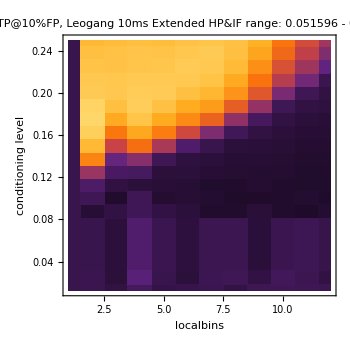
-Graphics-   -Graphics-

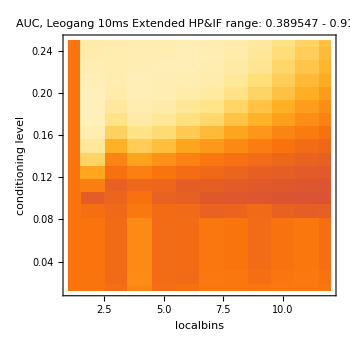
-Graphics-   -Graphics-

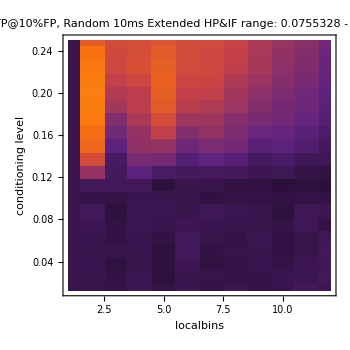
-Graphics-   -Graphics-

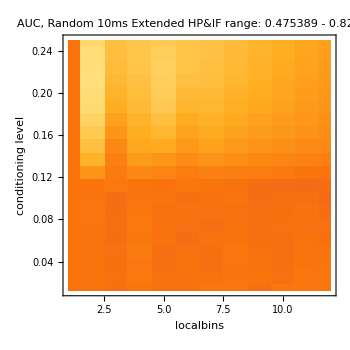
-Graphics-   -Graphics-

```mathematica
(* automatically generate arrayplot from the data above *)
Row[{ListContourPlot[#,InterpolationOrder->0,ColorFunction->"SunsetColors",ColorFunctionScaling->False,FrameLabel->{"localbins","conditioning level"},PlotLabel->"TP@10%FP, Leogang\n10ms Extended HP&IF\nrange: "<>ToString@Min@Cases[Flatten@#⟦All,3⟧,_Real]<>" - "<>ToString@Max@Cases[Flatten@#⟦All,3⟧,_Real],FrameTicks->Automatic,Contours->Union@#⟦All,3⟧,ImageSize->350,PlotRange->All],"   ",QuickLegend[0,1]}]&@x10percentlist

Row[{ListContourPlot[#,InterpolationOrder->0,ColorFunction->"SunsetColors",ColorFunctionScaling->False,FrameLabel->{"localbins","conditioning level"},PlotLabel->"AUC, Leogang\n10ms Extended HP&IF\nrange: "<>ToString@Min@Cases[Flatten@#⟦All,3⟧,_Real]<>" - "<>ToString@Max@Cases[Flatten@#⟦All,3⟧,_Real],FrameTicks->Automatic,Contours->Union@#⟦All,3⟧,ImageSize->350,PlotRange->All],"   ",QuickLegend[0,1]}]&@AUClist
```

## create 2 D plots of the reconstruction quality (local binning & local conditioning)

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/Localcond-2D/Random";
SetDirectory@basedir;
```

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/MinLocalcond-2D/Random";
SetDirectory@basedir;
```

```mathematica
startii=0;
endii=399;
xstarttime=AbsoluteTime[];
x10percentlist=AUClist={};
For[ii=startii,ii≤endii,ii++,
ShowStatus["ii = "<>ToString@ii<>", ETA "<>ETA[ii-startii,endii-startii+1,xstarttime]];
If[FileExistsQ["adjA_iteration"<>ToString@ii<>".mx"],
xadjA=Get["adjA_iteration"<>ToString@ii<>".mx"]⟦All,All,1⟧;
parsstring=Get["pars_iteration"<>ToString@ii<>".mx"];
fn=Interpolation[ReduceForInterpolation@N@GenerateROCsmart@xadjA,InterpolationOrder->1];

AppendTo[x10percentlist,{bins/.parsstring,LocalConditioningLevel/.parsstring,fn[0.1]}];
AppendTo[AUClist,{bins/.parsstring,LocalConditioningLevel/.parsstring,NIntegrate[fn[x],{x,0,1}]}];
];
];
ShowStatus["done."];
Clear[xstarttime,ii,startii,endii,parsstring,xadjA,fn,ROCpoints];
```

```mathematica
x10percentlist
```

```mathematica
(* save results *)
x10percentlist>>"x10percentlist.mx";
AUClist>>"AUClist.mx";
```

```mathematica
(* load results *)
x10percentlist=<<"x10percentlist.mx";
AUClist=<<"AUClist.mx";
```

```mathematica
x10percentlist
AUClist
```

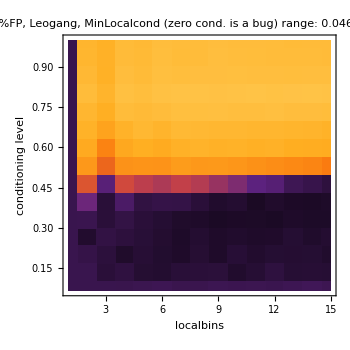
-Graphics-   -Graphics-

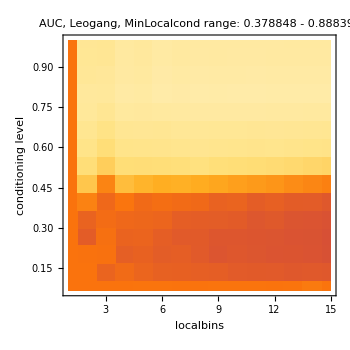
-Graphics-   -Graphics-

```mathematica
(* automatically generate arrayplot from the data above *)
Row[{ListContourPlot[#,InterpolationOrder->0,ColorFunction->"SunsetColors",ColorFunctionScaling->False,FrameLabel->{"localbins","conditioning level"},PlotLabel->"TP@10%FP, Leogang, MinLocalcond\n(zero cond. is a bug)\nrange: "<>ToString@Min@Cases[Flatten@#⟦All,3⟧,_Real]<>" - "<>ToString@Max@Cases[Flatten@#⟦All,3⟧,_Real],FrameTicks->Automatic,Contours->Union@#⟦All,3⟧,ImageSize->350,PlotRange->All],"   ",QuickLegend[0,1]}]&@x10percentlist

Row[{ListContourPlot[#,InterpolationOrder->0,ColorFunction->"SunsetColors",ColorFunctionScaling->False,FrameLabel->{"localbins","conditioning level"},PlotLabel->"AUC, Leogang, MinLocalcond\nrange: "<>ToString@Min@Cases[Flatten@#⟦All,3⟧,_Real]<>" - "<>ToString@Max@Cases[Flatten@#⟦All,3⟧,_Real],FrameTicks->Automatic,Contours->Union@#⟦All,3⟧,ImageSize->350,PlotRange->All],"   ",QuickLegend[0,1]}]&@AUClist
```

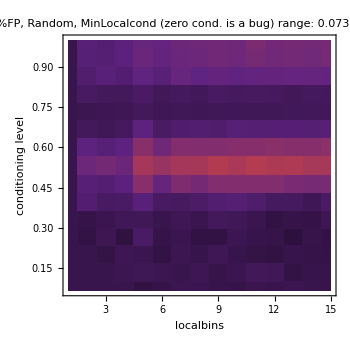
-Graphics-   -Graphics-

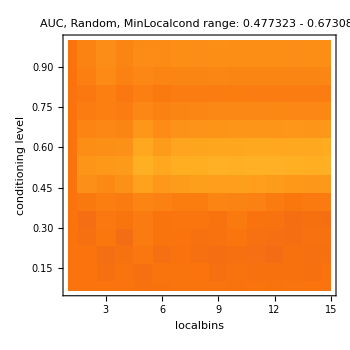
-Graphics-   -Graphics-

```mathematica
(* automatically generate arrayplot from the data above *)
Row[{ListContourPlot[#,InterpolationOrder->0,ColorFunction->"SunsetColors",ColorFunctionScaling->False,FrameLabel->{"localbins","conditioning level"},PlotLabel->"TP@10%FP, Random, MinLocalcond\n(zero cond. is a bug)\nrange: "<>ToString@Min@Cases[Flatten@#⟦All,3⟧,_Real]<>" - "<>ToString@Max@Cases[Flatten@#⟦All,3⟧,_Real],FrameTicks->Automatic,Contours->Union@#⟦All,3⟧,ImageSize->350,PlotRange->All],"   ",QuickLegend[0,1]}]&@x10percentlist

Row[{ListContourPlot[#,InterpolationOrder->0,ColorFunction->"SunsetColors",ColorFunctionScaling->False,FrameLabel->{"localbins","conditioning level"},PlotLabel->"AUC, Random, MinLocalcond\nrange: "<>ToString@Min@Cases[Flatten@#⟦All,3⟧,_Real]<>" - "<>ToString@Max@Cases[Flatten@#⟦All,3⟧,_Real],FrameTicks->Automatic,Contours->Union@#⟦All,3⟧,ImageSize->350,PlotRange->All],"   ",QuickLegend[0,1]}]&@AUClist
```

```mathematica
xBins=9;
xCond=0.45;
xindex=Round[15*(xBins-1)+15*xCond]
parsstring=Get["pars_iteration"<>ToString@xindex<>".mx"]
```

127

{executable→teextendedsim,iteration→128,size→100,rawdatabins→255,bins→9,cutoff→-1,globalbins→2,samples→359951,StartSampleIndex→1,EndSampleIndex→359950,EqualSampleNumberQ→False,MaxSampleNumberPerBin→-1,AvailableSamples→{189068,170881},noise→0.03,tauF→20,OverrideRescalingQ→False,HighPassFilterQ→True,InstantFeedbackTermQ→True,saturation→300,IncludeGlobalSignalQ→True,GenerateGlobalFromFilteredDataQ→False,GlobalConditioningLevel→inactive at compile time,LocalConditioningLevel→0.533333,TargetMarkovOrder→1,SourceMarkovOrder→1,inputfile→../../Simulationen/NEST/calciumbursts2/Paris/RandomTopology/noisefree_rawCalcium_uchar_20ms.dat,outputfile→MinLocalcond-2D/Random/adjA_iteration127.mx}

```mathematica
adjAtest=Get["adjA_iteration"<>ToString@xindex<>".mx"]⟦All,All,1⟧;
```

```mathematica
xadjARnd:=adjAtest;
```

## create 2 D plots of topological quantities (local binning & global conditioning)

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/Paris/2DbinningCondSatNoiseExtended/Random";
SetDirectory@basedir;
```

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/Paris/LightScatter-Test/IF";
SetDirectory@basedir;
```

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/Olav0816A/2DConditioned";
SetDirectory@basedir;
```

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/0811B-GEI/2DbinningCond";
SetDirectory@basedir;
```

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/0811B-GE/2DbinningCond";
SetDirectory@basedir;
```

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/0815B-GEI/2DCond";
SetDirectory@basedir;
```

```mathematica
xconsfraction=0.05;
xmethod="clustering index, cycle type, all entries";
(* xmethod="undirected clustering index, all entries"; *)

startii=0;
endii=399;
xstarttime=AbsoluteTime[];
CClist={};
For[ii=startii,ii≤endii,ii++,
ShowStatus["ii = "<>ToString@ii<>", elapsed "<>Seconds2StringComfort[AbsoluteTime[]-xstarttime,2]<>", ETA "<>ETA[ii-startii,endii-startii+1,xstarttime]];
If[FileExistsQ["adjA_iteration"<>ToString@ii<>".mx"],
xadjA=Get["adjA_iteration"<>ToString@ii<>".mx"]⟦All,All,1⟧;
parsstring=Get["pars_iteration"<>ToString@ii<>".mx"];

AppendTo[CClist,{bins/.parsstring,GlobalConditioningLevel/.parsstring,If[Length@Union@Flatten@xadjA<3,0,Mean@MeasureQuality[ThresholdedFractionASparse[xadjA,xconsfraction],xmethod]]}];
];
];
ShowStatus["done."];
Clear[xstarttime,ii,startii,endii,parsstring,xadjA,bins,xmethod];
```

```mathematica
CClist
Length@%
```

200

```mathematica
f[x_,y_,opts:OptionsPattern[]]:=bla;
Options[f,opts]={offset->0};
```

```mathematica
f[x_,y_,opts___Rule]:=x+y+(offset /.{opts}/.Options[f]);
Options[f]={offset->0};
```

```mathematica
f[x,y,offset->100]
```

100+x+y

```mathematica
(* save results *)
CClist>>"CClist.mx";
```

```mathematica
(* load results *)
CClist=<<"CClist.mx";
```

```mathematica
(* load results *)
CClist=<<"CCundirlist.mx";
```

```mathematica
QuickLegend[0,1]
```

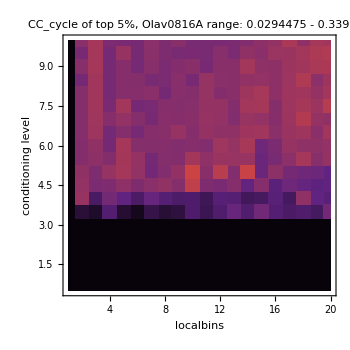
-Graphics-   -Graphics-

```mathematica
(* automatically generate arrayplot from the data above *)
Row[{ListContourPlot[CClist,InterpolationOrder->0,ColorFunction->"SunsetColors",ColorFunctionScaling->False,FrameLabel->{"localbins","conditioning level"},PlotLabel->"CC_cycle of top 5%, Olav0816A\nrange: "<>ToString@Min@Cases[Flatten@CClist⟦All,3⟧,_Real]<>" - "<>ToString@Max@Cases[Flatten@CClist⟦All,3⟧,_Real],FrameTicks->Automatic,Contours->Union@CClist⟦All,3⟧,ImageSize->350],"   ",QuickLegend[0,1]}]
```

## examine rank ordering for different conditioning values

### inital definitions and plots

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/Paris/2DbinningCondSatNoise/Leogang";
SetDirectory@basedir;
```

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/Live/2DConditioned";
SetDirectory@basedir;
```

```mathematica
xindices=Table[14+20*ii,{ii,0,19}]
```

{14,34,54,74,94,114,134,154,174,194,214,234,254,274,294,314,334,354,374,394}

```mathematica
xindices=Table[ii+20*9,{ii,0,19}]
```

{180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199}

```mathematica
TellMeWhatHappened[Get["pars_iteration"<>ToString@#<>".mx"]&/@xindices,3]
```

constant parameters:

{executable→teglobalsim,size→40,rawdatabins→255,cutoff→-1,globalbins→2,samples→40954,p→1,noise→-1,tauF→40,OverrideRescalingQ→0,HighPassFilterQ→1,InstantFeedbackTermQ→1,AdaptiveBinningQ→0,saturation→-1,IncludeGlobalSignalQ→1,GenerateGlobalFromFilteredDataQ→0,GlobalConditioningLevel→5,inputfile→../../Imaging/Olav0816A/xresponse_255bins.dat}

variable parameters:

#1: {iteration→10,bins→1,outputfile→Live/2DConditioned/adjA_iteration180.mx}

#2: {iteration→30,bins→2,outputfile→Live/2DConditioned/adjA_iteration181.mx}

#3: {iteration→50,bins→3,outputfile→Live/2DConditioned/adjA_iteration182.mx}

(remaining 17 iterations hidden.)

```mathematica
xstarttime=AbsoluteTime[];
parslist=rankslist=x10percentlist=meandistlist={};
For[ii=1,ii≤Length@xindices,ii++,
ShowStatus["ii = "<>ToString@ii<>", ETA "<>ETA[ii-1,Length@xindices,xstarttime]];
xadjA=Get["adjA_iteration"<>ToString@xindices⟦ii⟧<>".mx"]⟦All,All,1⟧;
xdata=DeleteCases[Sort@Flatten[Table[If[ii≠jj,{adjA⟦ii,jj⟧,xadjA⟦ii,jj⟧},{"nix"}],{ii,Length@adjA},{jj,Length@adjA}],1],{"nix"}];
AppendTo[parslist,parsstring=Get["pars_iteration"<>ToString@xindices⟦ii⟧<>".mx"]];

AppendTo[rankslist,RankOrder@Flatten@RemoveDiagonal@xadjA]; (* smallest element first *)

(*fn=Interpolation[ReduceForInterpolation@N@GenerateROCsmart@xadjA,InterpolationOrder->1];
AppendTo[x10percentlist,fn[0.1]];*)

AppendTo[meandistlist,MeanDistanceInNetwork[xadjA,0.1,pos]];

];
ShowStatus["done."];
Clear[xstarttime,ii,tempindex,startii,endii,parsstring,xadjA,fn];
```

```mathematica
{parslist,rankslist,x10percentlist}>>"ParsRanks10PercentLists.mx"
```

```mathematica
x10percentlist
```

{0.0837892,0.109314,0.109314,0.109314,0.109314,0.109314,0.0755224,0.0993613,0.119092,0.198907,0.392182,0.609804,0.717234,0.780361,0.766629,0.742888,0.735966,0.727171,0.719617,0.696763}

```mathematica
meandistlist
```

{0.469183,0.469183,0.469183,0.469183,0.469183,0.469183,0.351237,0.347532,0.378326,0.385204,0.389992,0.400546,0.413915,0.415092,0.416621,0.422983,0.42767,0.429053,0.433131,0.439598}

```mathematica
ListPlot[meandistlist,Joined->True,FrameLabel->{"iteration #","<d> of top 10% links"}]
```

```mathematica
TellMeWhatHappened[parslist,2]
```

```mathematica
Dimensions@Transpose@rankslist
```

{9900,20}

```mathematica
ListPlot[x10percentlist,Joined->True,PlotRange->All,FrameLabel->{"iteration #","TP @ 10% FP"}]
```

```mathematica
xtrajectories=Transpose@rankslist;
xdifftrajectories=Table[xtrajectories⟦ii,it⟧-xtrajectories⟦ii,it-1⟧,{ii,Length@xtrajectories},{it,2,Length@First@xtrajectories}];
```

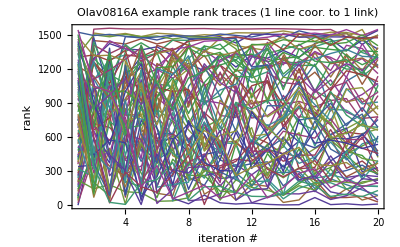

```mathematica
ListPlot[xtrajectories⟦1;;40*39;;20⟧,Joined->True,PlotRange->All,FrameLabel->{"iteration #","rank"},PlotLabel->"Olav0816A\nexample rank traces (1 line coor. to 1 link)"]
```

```mathematica
ListPlot[xtemp=Mean@Abs@xdifftrajectories,Joined->True,PlotRange->All,FrameLabel->{"iteration #","abs. Δ rank"},PlotLabel->"avg. of all off-diagonal CGTE entries"]
```

### Does the rank of links fluctuate less than the rank of non - links?

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/Paris/2DbinningCondSatNoise/Random";
SetDirectory@basedir;
```

```mathematica
xindices=Table[4+20*ii,{ii,0,19}]
```

{4,24,44,64,84,104,124,144,164,184,204,224,244,264,284,304,324,344,364,384}

```mathematica
TellMeWhatHappened[Get["pars_iteration"<>ToString@#<>".mx"]&/@xindices,2]
```

constant parameters:

{executable→teglobalsim,size→100,rawdatabins→255,bins→5,cutoff→-1,globalbins→2,samples→359951,p→1,noise→0.03,tauF→20,OverrideRescalingQ→0,HighPassFilterQ→1,InstantFeedbackTermQ→1,saturation→300,IncludeGlobalSignalQ→1,GenerateGlobalFromFilteredDataQ→0,inputfile→../../Simulationen/NEST/calciumbursts2/Paris/RandomTopology/noisefree_rawCalcium_uchar_20ms.dat}

variable parameters:

#1: {iteration→81,GlobalConditioningLevel→0.0125,outputfile→Paris/2DbinningCondSatNoise/Random/adjA_iteration4.mx,outputparsfile→Paris/2DbinningCondSatNoise/Random/pars_iteration4.mx,outputcrossvalfile→Paris/2DbinningCondSatNoise/Random/crossval_iteration4.mx}

#2: {iteration→82,GlobalConditioningLevel→0.025,outputfile→Paris/2DbinningCondSatNoise/Random/adjA_iteration24.mx,outputparsfile→Paris/2DbinningCondSatNoise/Random/pars_iteration24.mx,outputcrossvalfile→Paris/2DbinningCondSatNoise/Random/crossval_iteration24.mx}

(remaining 18 iterations hidden.)

```mathematica
xstarttime=AbsoluteTime[];
parslist=rankslist=x10percentlist=meandistlist={};
For[ii=1,ii≤Length@xindices,ii++,
ShowStatus["ii = "<>ToString@ii<>", ETA "<>ETA[ii-1,Length@xindices,xstarttime]];
xadjA=Get["adjA_iteration"<>ToString@xindices⟦ii⟧<>".mx"]⟦All,All,1⟧;
xdata=DeleteCases[Sort@Flatten[Table[If[ii≠jj,{adjA⟦ii,jj⟧,xadjA⟦ii,jj⟧},{"nix"}],{ii,Length@adjA},{jj,Length@adjA}],1],{"nix"}];
AppendTo[parslist,parsstring=Get["pars_iteration"<>ToString@xindices⟦ii⟧<>".mx"]];

AppendTo[rankslist,RankOrder@Flatten@RemoveDiagonal@xadjA]; (* smallest element first *)

fn=Interpolation[ReduceForInterpolation@N@GenerateROCsmart@xadjA,InterpolationOrder->1];
AppendTo[x10percentlist,fn[0.1]];

(*AppendTo[meandistlist,MeanDistanceInNetwork[xadjA,0.1,pos]];*)

];
ShowStatus["done."];
Clear[xstarttime,ii,tempindex,startii,endii,parsstring,xadjA,fn];
```

```mathematica
xtrajectories=Transpose@rankslist;
xdifftrajectories=Table[xtrajectories⟦ii,it⟧-xtrajectories⟦ii,it-1⟧,{ii,Length@xtrajectories},{it,2,Length@First@xtrajectories}];
```

```mathematica
ListPlot[xtrajectories⟦1;;((size/.pars)*((size/.pars)-1));;100⟧,Joined->True,PlotRange->All,FrameLabel->{"iteration #","rank"},PlotLabel->"Leogang\nexample rank traces (1 line coor. to 1 link)"]
```

```mathematica
adjAtrajectories=SwitchFromRanksToMatrix/@rankslist;

adjAtrajectoriesTrue=adjAtrajectoriesFalse={};
For[ii=1,ii≤size/.pars,ii++,
For[jj=1,jj≤size/.pars,jj++,
If[ii≠jj,
If[adjA⟦ii,jj⟧==1,AppendTo[adjAtrajectoriesTrue,adjAtrajectories⟦All,ii,jj⟧],AppendTo[adjAtrajectoriesFalse,adjAtrajectories⟦All,ii,jj⟧]];
];
]];
Clear[ii,jj];
```

```mathematica
Dimensions@adjAtrajectoriesTrue
Dimensions@adjAtrajectoriesFalse
```

{1200,20}

{8700,20}

```mathematica
ListPlot[x10percentlist,Joined->True,PlotRange->All,FrameLabel->{"iteration #","TP @ 10% FP"}]
```

```mathematica
ListPlot[adjAtrajectoriesTrue⟦1;;Length@adjAtrajectoriesTrue;;20⟧,Joined->True,PlotRange->All,FrameLabel->{"iteration #","rank"},PlotLabel->"example rank traces of true links (1 line coor. to 1 link)"]
ListPlot[adjAtrajectoriesFalse⟦1;;Length@adjAtrajectoriesTrue;;20⟧,Joined->True,PlotRange->All,FrameLabel->{"iteration #","rank"},PlotLabel->"example rank traces of non-links (1 line coor. to 1 link)"]
```

```mathematica
ListPlot[{Mean@Abs@adjAtrajectoriesFalse,Mean@Abs@adjAtrajectoriesTrue},Joined->True,PlotRange->All,FrameLabel->{"iteration #","avg. rank"},PlotLabel->"non-links / links"]
```

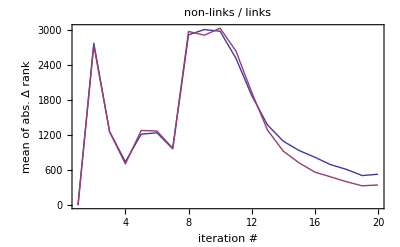

```mathematica
ListPlot[{Mean@Abs[SwitchToDiff/@adjAtrajectoriesFalse],Mean@Abs[SwitchToDiff/@adjAtrajectoriesTrue]},Joined->True,PlotRange->All,FrameLabel->{"iteration #","mean of abs. Δ rank"},PlotLabel->"non-links / links"]
```

### Is it possibly to improve reconstruction by averaging over ROCs?

```mathematica
ListPlot[x10percentlist,Joined->True,PlotRange->All,FrameLabel->{"iteration #","TP @ 10% FP"}]
```

```mathematica
Dimensions@rankslist
```

{20,9900}

```mathematica
Dimensions@SwitchFromRanksToMatrix@rankslist⟦14⟧
```

{100,100}

```mathematica
ArrayPlot@SwitchFromRanksToMatrix@rankslist⟦14⟧
```

```mathematica
ListPlot[GenerateROCsmart@SwitchFromRanksToMatrix@rankslist⟦14⟧,Joined->True,GridLines->{{0.1},{}},Axes->False,AspectRatio->1,FrameLabel->{"fraction of false positives","fraction of true positives"},PlotLabel->"ROC from ranks only (it. #14)",PlotRange->All]
```

```mathematica
startit=7;
endit=Length@parslist;
meanadjAs={};
For[it=startit,it≤endit,it+=2,
AppendTo[meanadjAs,SwitchFromRanksToMatrix@RankOrder@Flatten@RemoveDiagonal@Mean@rankslist⟦startit;;it⟧]
];
```

```mathematica
ListPlot[GenerateROCsmart/@meanadjAs,Joined->True,GridLines->{{0.1},{}},Axes->False,AspectRatio->1,FrameLabel->{"fraction of false positives","fraction of true positives"},PlotLabel->"ROC from ranks only, ranks averaged from it. #7 up",PlotRange->All]
```

```mathematica
startit=7;
endit=Length@parslist-1;
meanadjAs={};
For[it=startit,it≤endit,it+=2,
AppendTo[meanadjAs,SwitchFromRanksToMatrix@RankOrder@Flatten@RemoveDiagonal@Mean@rankslist⟦it-1;;it+1⟧]
];
```

```mathematica
ListPlot[GenerateROCsmart/@meanadjAs,Joined->True,GridLines->{{0.1},{}},Axes->False,AspectRatio->1,FrameLabel->{"fraction of false positives","fraction of true positives"},PlotLabel->"ROC from ranks only, ranks averaged around current it.",PlotRange->All]
```

### rank ordering as a way to identify best parameters? (1D)

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/Paris/RankOrderTest/Leogang";
SetDirectory@basedir;
```

```mathematica
TellMeWhatHappened[importpars=Get["pars_iteration0.mx"],3]
```

parameters: {executable→teglobalsim,iteration→1,size→100,rawdatabins→255,bins→5,cutoff→-1,globalbins→40,samples→359951,StartSampleIndex→1,EndSampleIndex→359950,AvailableSamples→{11,1,0,0,0,2,912,24422,91982,69353,27283,15459,12019,9880,8583,7729,6800,6341,6015,5609,5217,5028,4786,4510,4417,4111,4122,3900,3802,3719,3671,3547,3584,3399,3495,3499,1756,626,288,71},p→1,noise→0.03,tauF→20,OverrideRescalingQ→0,HighPassFilterQ→1,InstantFeedbackTermQ→1,saturation→300,IncludeGlobalSignalQ→1,GenerateGlobalFromFilteredDataQ→0,GlobalConditioningLevel→-1,inputfile→../../Simulationen/NEST/calciumbursts2/Paris/LeogangTopology/noisefree_rawCalcium_uchar_20ms.dat,outputfile→Paris/RateConditioningTest/Leogang/adjA_iteration0.mx,outputparsfile→Paris/RateConditioningTest/Leogang/pars_iteration0.mx}

```mathematica
(* plot ROC curves *)
xindex=4; (* 5 localbins *)
importlist=<<("adjA_iteration"<>ToString@xindex<>".mx");
parsstring=<<("pars_iteration"<>ToString@xindex<>".mx");
importlist2=Table[importlist⟦All,All,ii⟧,{ii,Last@Dimensions@importlist}];
Clear[importlist,xindex];
```

```mathematica
xplotdata=GenerateROCsmart/@importlist2;
xplotdata3D=Flatten[Table[Flatten[{ii,#}]&/@xplotdata⟦ii⟧,{ii,Length@xplotdata}],1];
```

```mathematica
ListPlot[GenerateROCsmart/@importlist2,Joined->True,GridLines->{{0.1},{}},Axes->False,AspectRatio->1,FrameLabel->{"fraction of false positives","fraction of true positives"},PlotLabel->"ROC from ranks only, ranks averaged from it. #7 up",PlotRange->All]
```

```mathematica
ListPlot3D[xplotdata3D,AspectRatio->1,AxesLabel->{"globalbin","FP","TP"},PlotRange->All,ColorFunction->"SunsetColors"]
```

-Graphics3D-

```mathematica
xstarttime=AbsoluteTime[];
rankslist=x10percentlist={};
ximport=Get["adjA_iteration4.mx"];
For[ii=1,ii≤(globalbins/.importpars),ii++,
ShowStatus["ii = "<>ToString@ii<>", ETA "<>ETA[ii-1,Length@xindices,xstarttime]];
xadjA=ximport⟦All,All,ii⟧;
xdata=Module[{ii,jj},DeleteCases[Sort@Flatten[Table[If[ii≠jj,{adjA⟦ii,jj⟧,xadjA⟦ii,jj⟧},{"nix"}],{ii,Length@adjA},{jj,Length@adjA}],1],{"nix"}]];
AppendTo[rankslist,RankOrder@Flatten@RemoveDiagonal@xadjA]; (* smallest element fist *)

fn=Interpolation[ReduceForInterpolation@N@GenerateROCsmart@xadjA,InterpolationOrder->1];
AppendTo[x10percentlist,fn[0.1]];

];
ShowStatus["done."];
Clear[xstarttime,ii,tempindex,startii,endii,parsstring,xadjA,fn];
```

```mathematica
x10percentlist
```

{0.101163,0.1,0.1,0.1,0.1,0.0986868,0.0766154,0.0825062,0.169883,0.32761,0.577144,0.685564,0.726491,0.701758,0.638596,0.599181,0.545349,0.44826,0.400654,0.374708,0.341636,0.342796,0.320737,0.312346,0.340855,0.323985,0.334399,0.306305,0.285658,0.286014,0.33927,0.313578,0.388352,0.411721,0.305939,0.366473,0.36666,0.321378,0.297125,0.237685}

```mathematica
Dimensions@Transpose@rankslist
```

{9900,20}

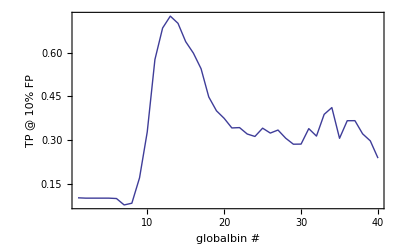

```mathematica
ListPlot[x10percentlist,Joined->True,PlotRange->All,FrameLabel->{"globalbin #","TP @ 10% FP"}]
```

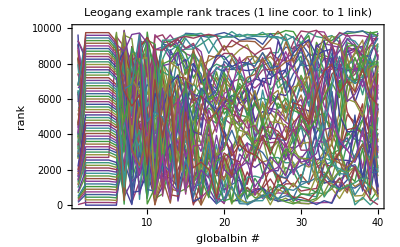

```mathematica
ListPlot[Transpose[rankslist]⟦1;;9900;;150⟧,Joined->True,PlotRange->{0,10000},FrameLabel->{"globalbin #","rank"},PlotLabel->"Leogang\nexample rank traces (1 line coor. to 1 link)"]
```

```mathematica
xtrajectories=Transpose@rankslist;
xdifftrajectories=Table[xtrajectories⟦ii,it⟧-xtrajectories⟦ii,it-1⟧,{ii,Length@xtrajectories},{it,2,Length@First@xtrajectories}];
```

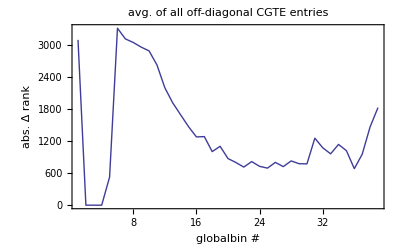

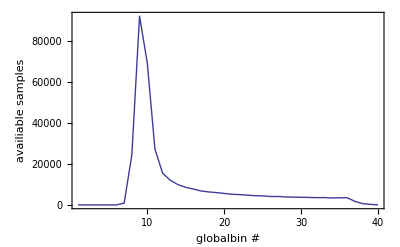

```mathematica
ListPlot[xtemp=Mean@Abs@xdifftrajectories,Joined->True,PlotRange->All,FrameLabel->{"globalbin #","abs. Δ rank"},PlotLabel->"avg. of all off-diagonal CGTE entries"]
ListPlot[AvailableSamples/.importpars,Joined->True,PlotRange->All,FrameLabel->{"globalbin #","availiable samples"}]
```

```mathematica
ListPlot[Table[√(Variance@xdifftrajectories⟦All,tt⟧),{tt,Length@First@xdifftrajectories}],Joined->True,PlotRange->All,FrameLabel->{"globalbin #","σ of Δ rank"},PlotLabel->"avg. of all off-diagonal CGTE entries"]
```

### rank ordering as a way to identify best parameters? (2D)

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/Paris/RankOrderTest/Leogang";
SetDirectory@basedir;
```

```mathematica
xstarttime=AbsoluteTime[];
parslist=rankslist=x10percentlist={};
xnum=20;
For[il=1,il≤xnum,il++,
ximport=Get["adjA_iteration"<>ToString@(il-1)<>".mx"];
AppendTo[parslist,Get["pars_iteration"<>ToString@(il-1)<>".mx"]];
ShowStatus["il = "<>ToString@il<>", ETA "<>ETA[il-1,xnum,xstarttime]];

For[ii=1,ii≤(globalbins/.Last@parslist),ii++,
xadjA=ximport⟦All,All,ii⟧;
xdata=Module[{ii,jj},DeleteCases[Sort@Flatten[Table[If[ii≠jj,{adjA⟦ii,jj⟧,xadjA⟦ii,jj⟧},{"nix"}],{ii,Length@adjA},{jj,Length@adjA}],1],{"nix"}]];
AppendTo[rankslist,RankOrder@Flatten@RemoveDiagonal@xadjA]; (* smallest element fist *)

fn=Interpolation[ReduceForInterpolation@N@GenerateROCsmart@xadjA,InterpolationOrder->1];
AppendTo[x10percentlist,fn[0.1]];

]];
ShowStatus["done."];
Clear[xstarttime,ii,il,tempindex,startii,endii,parsstring,xadjA,fn,ximport,xdata];
```

```mathematica
{parslist,rankslist,x10percentlist}>>"temp.mx"
```

```mathematica
{parslist,rankslist,x10percentlist}=<<"temp.mx";
xtemp=globalbins/.Last@parslist;
rankslist=Partition[rankslist,xtemp];
x10percentlist=Partition[x10percentlist,xtemp];
Clear[xtemp];
```

```mathematica
TellMeWhatHappened[parslist,2]
```

constant parameters:

{executable→teglobalsim,size→100,rawdatabins→255,cutoff→-1,globalbins→40,samples→359951,StartSampleIndex→1,EndSampleIndex→359950,AvailableSamples→{11,1,0,0,0,2,912,24422,91982,69353,27283,15459,12019,9880,8583,7729,6800,6341,6015,5609,5217,5028,4786,4510,4417,4111,4122,3900,3802,3719,3671,3547,3584,3399,3495,3499,1756,626,288,71},p→1,noise→0.03,tauF→20,OverrideRescalingQ→0,HighPassFilterQ→1,InstantFeedbackTermQ→1,saturation→300,IncludeGlobalSignalQ→1,GenerateGlobalFromFilteredDataQ→0,GlobalConditioningLevel→-1,inputfile→../../Simulationen/NEST/calciumbursts2/Paris/LeogangTopology/noisefree_rawCalcium_uchar_20ms.dat}

variable parameters:

#1: {iteration→1,bins→1,outputfile→Paris/RankOrderTest/Leogang/adjA_iteration0.mx,outputparsfile→Paris/RankOrderTest/Leogang/pars_iteration0.mx}

#2: {iteration→2,bins→2,outputfile→Paris/RankOrderTest/Leogang/adjA_iteration1.mx,outputparsfile→Paris/RankOrderTest/Leogang/pars_iteration1.mx}

(remaining 18 iterations hidden.)

```mathematica
Dimensions@x10percentlist
Dimensions@rankslist
```

{20,40}

{20,40,9900}

```mathematica
ListPlot3D[Flatten[Table[{bins/.parslist⟦ii⟧,jj,x10percentlist⟦ii,jj⟧},{ii,20},{jj,40}],1],AxesLabel->{"localbins","globalbin\n(sep.)","TP@10%FP"},PlotRange->All,ColorFunction->"SunsetColors",PlotLabel->"topology: Leogang"]
```

#### simple left - right 2 D plots

```mathematica
xtrajectories=Transpose[rankslist,{2,3,1}];
```

```mathematica
Dimensions@rankslist
Dimensions@xtrajectories
```

{20,40,9900}

{9900,20,40}

```mathematica
xtemp=Flatten[Table[{bins/.parslist⟦ii⟧,jj,Mean@Abs[xtrajectories⟦All,ii,jj⟧-xtrajectories⟦All,ii,jj-1⟧]},{ii,20},{jj,2,40}],1];
ListPlot3D[xtemp,AxesLabel->{"localbins","globalbin #","<|Δrank|>"},PlotRange->All,ColorFunction->"SunsetColors",PlotLabel->"avg. of all off-diagonal CGTE entries\nΔ is calculated going from lower to higher globabins"]
```

-Graphics3D-

```mathematica
xtemp=Flatten[Table[{bins/.parslist⟦ii⟧,jj,Mean@Abs[xtrajectories⟦All,ii,jj⟧-xtrajectories⟦All,ii-1,jj⟧]},{ii,2,20},{jj,40}],1];
ListPlot3D[xtemp,AxesLabel->{"localbins","globalbin #","<|Δrank|>"},PlotRange->All,ColorFunction->"SunsetColors",PlotLabel->"avg. of all off-diagonal CGTE entries\nΔ is calculated going from lower to higher localbin number"]
```

## plot original time series in comparison to reconstruction

```mathematica
(* load original time series, take input file from reconstuction output *)
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/Paris/SeparatedTest";
SetDirectory@basedir;
Clear[inputfile];
Print[xpars=<<"pars_iteration0.mx"];

SetDirectory["../.."];
xinput=Import[inputfile/.xpars,"UnsignedInteger8"];
If[Mod[Length@xinput,size/.pars]≠0,Abert[]];
xinput=Partition[xinput,Length@xinput/(size/.pars)];
```

{executable→teglobalsim,iteration→1,size→100,rawdatabins→255,bins→2,cutoff→-1,globalbins→2,samples→359951,p→1,noise→-1,tauF→20,OverrideRescalingQ→0,HighPassFilterQ→1,InstantFeedbackTermQ→1,AdaptiveBinningQ→0,inputfile→../../Simulationen/NEST/calciumbursts2/Paris/RandomTopology/noisefree_rawCalcium_uchar_20ms.dat,outputfile→Paris/SeparatedTest/adjA_iteration0.mx}

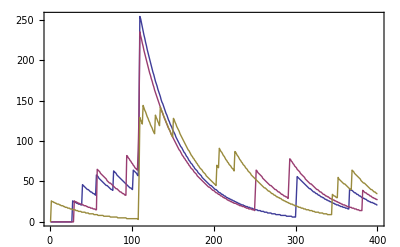

```mathematica
ListPlot[xinput⟦1;;3,1;;400⟧,Joined->True,PlotRange->All]
```

```mathematica
inDegree/@Range[1,13]
```

{14,12,9,13,10,11,13,11,15,14,9,15,7}

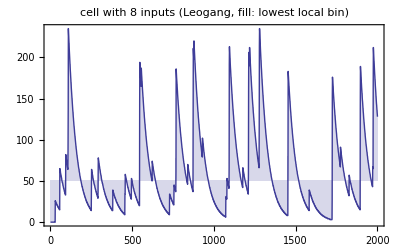

```mathematica
ListPlot[xinput⟦2,1;;2000⟧,Joined->True,PlotRange->All,Filling->(Max@xinput⟦2⟧)/5,PlotLabel->"cell with 8 inputs (Leogang, fill: lowest local bin)"]
ListPlot[xinput⟦7,1;;2000⟧,Joined->True,PlotRange->All,Filling->(Max@xinput⟦7⟧)/5,PlotLabel->"cell with 17 inputs (Leogang, fill: lowest local bin)"]
ListPlot[Mean@xinput⟦All,1;;2000⟧,Joined->True,PlotRange->All,Filling->(Max@Mean@xinput)/4,PlotLabel->"avg. activity (Leogang, fill: lowest global bin)"]
```

```mathematica
Histogram[xinput⟦{2,7}⟧]
```

```mathematica
Min/@xinput⟦{2,7}⟧
Max/@xinput⟦{2,7}⟧
N@(Max/@xinput⟦{2,7}⟧)/5
(N@Sqrt@Variance@#&)/@xinput⟦{2,7}⟧
```

{0,0}

{208,254}

{41.6,50.8}

{27.103,46.9173}

```mathematica
N@Max@Mean@xinput
%/4
N@Sqrt@Variance@Mean@xinput
```

182.37

45.5925

30.9614

```mathematica
xinputDelta=Table[0,{size/.pars},{samples/.xpars}];
For[ii=1,ii≤size/.pars,ii++,
ShowStatus["ii = "<>ToString@ii];
For[tt=2,tt≤samples/.xpars,tt++,
xinputDelta⟦ii,tt⟧=N[xinput⟦ii,tt⟧-xinput⟦ii,tt-1⟧];
]];
Clear[ii,tt];
```

$Aborted

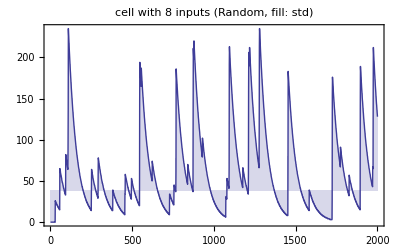

```mathematica
ListPlot[xinput⟦2,1;;2000⟧,Joined->True,PlotRange->All,Filling->Sqrt@Variance@xinput⟦13⟧,PlotLabel->"cell with 8 inputs (Random, fill: std)"]
ListPlot[xinput⟦7,1;;2000⟧,Joined->True,PlotRange->All,Filling->Sqrt@Variance@xinput⟦12⟧,PlotLabel->"cell with 17 inputs (Random, fill: std)"]
ListPlot[xinputDelta⟦2,1;;2000⟧,Joined->True,PlotRange->All,Filling->Sqrt@Variance@xinputDelta⟦13⟧,PlotLabel->"cell with 8 inputs (Random, fill: std)"]
ListPlot[xinputDelta⟦7,1;;2000⟧,Joined->True,PlotRange->All,Filling->Sqrt@Variance@xinputDelta⟦12⟧,PlotLabel->"cell with 17 inputs (Random, fill: std)"]
```

```mathematica
ListPlot[xinput⟦2,1;;2000⟧,Joined->True,PlotRange->All,Filling->Sqrt@Variance@xinput⟦2⟧,PlotLabel->"cell with 8 inputs (Leogang, fill: std)"]
ListPlot[xinput⟦7,1;;2000⟧,Joined->True,PlotRange->All,Filling->Sqrt@Variance@xinput⟦7⟧,PlotLabel->"cell with 17 inputs (Leogang, fill: std)"]
```

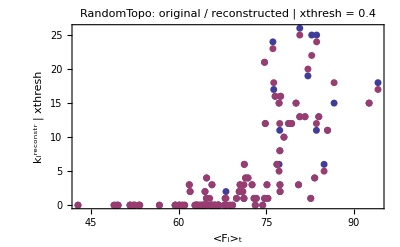

```mathematica
(* correlate firing frequency with reconstruction *)
xthresh = 0.4;

adjAtest-=Min@adjAtest; (* nonsense, because it includes diagonal elements *)
adjAtest/=Max@adjAtest;

scatterAin=scatterAout={};
For[ii=1,ii≤size/.pars,ii++,
AppendTo[scatterAin,{Mean@xinput⟦ii⟧,Length@Cases[adjAtest⟦ii,All⟧,_?(#>xthresh&)]}];
AppendTo[scatterAout,{Mean@xinput⟦ii⟧,Length@Cases[adjAtest⟦All,ii⟧,_?(#>xthresh&)]}];
];

ListPlot[{scatterAin,scatterAout},FrameLabel->{"<F_i>_t","k_i^reconstr | xthresh"},PlotRange->All,PlotLabel->"RandomTopo: original / reconstructed | xthresh = "<>ToString@xthresh,PlotStyle->AbsolutePointSize[5]]
Clear[ii];
```

```mathematica
(* correlate firing frequency with reconstruction 2*)
adjAtest-=Min@adjAtest; (* nonsense, because it includes diagonal elements *)
adjAtest/=Max@adjAtest;

scatterAin=scatterAout={};
For[ii=1,ii≤size/.pars,ii++,
AppendTo[scatterAin,{Mean@xinput⟦ii⟧,Mean@adjAtest⟦ii,All⟧}];
AppendTo[scatterAout,{Mean@xinput⟦ii⟧,Mean@adjAtest⟦All,ii⟧}];
];

ListPlot[{scatterAin,scatterAout},FrameLabel->{"<F_i>_t","<A_ij^reconstr>_(i/j)"},PlotRange->All,PlotStyle->AbsolutePointSize[5]]
ListPlot[Transpose@{Mean@adjAtest⟦#,All⟧&/@Range[size/.pars],Mean@adjAtest⟦All,#⟧&/@Range[size/.pars]},FrameLabel->{"<A_ij^reconstr>_i (in)","<A_ij^reconstr>_j (out)"},PlotRange->All,PlotStyle->AbsolutePointSize[5]]
Clear[ii];
```

```mathematica
xmin=Min[DeleteCases[adjAtest⟦All,#⟧,0.]]&/@Range[size/.pars];
xmax=Max[DeleteCases[adjAtest⟦All,#⟧,0.]]&/@Range[size/.pars];
ListPlot[Transpose@{xmin,xmax}]
```

## improve reconstruction using DPI

### single threshold

```mathematica
adjAtest=<<"adjA_iteration0.mx";
Print[<<"pars_iteration0.mx"];
(* normalization *)
adjAtest-=Min@adjAtest;
adjAtest/=Max@adjAtest;
```

{executable→teglobalsim,iteration→1,size→100,rawdatabins→255,bins→5,cutoff→-1,globalbins→3,samples→359951,p→1,noise→0,tauF→20,OverrideRescalingQ→0,HighPassFilterQ→1,InstantFeedbackTermQ→1,inputfile→../../Simulationen/NEST/calciumbursts2/Paris/RandomTopology/noisefree_rawCalcium_uchar_20ms.dat,outputfile→Paris/RandomTopology/adjA_iteration0.mx}

```mathematica
adjAtest2=adjAtest;
```

```mathematica
adjAtestList={adjAtest2};
```

```mathematica
cutcount=0;
threshold=0.05;
trials=0;
While[cutcount<6*size*size/.pars,
trials++;
(* For[trials=1,trials≤10000,trials++, *)
nodeA=Random[Integer,{1,size/.pars}];
nodeB=Random[Integer,{1,size/.pars}];
nodeC=Random[Integer,{1,size/.pars}];
If[(nodeA≠nodeB)&&(nodeA≠nodeC)&&(nodeB≠nodeC),
If[(adjAtest2⟦nodeA,nodeB⟧>adjAtest2⟦nodeA,nodeC⟧+threshold)&&(adjAtest2⟦nodeB,nodeC⟧>adjAtest2⟦nodeA,nodeC⟧+threshold),
adjAtest2⟦nodeA,nodeC⟧*=0.2;
cutcount++];
];
If[Mod[trials,1111]==0, ShowStatus["iteration: "<>ToString@trials<>", "<>ToString@cutcount<>" links 'deleted'."]];
];
ShowStatus[ToString@cutcount<>" links deleted. done."];
Clear[nodeA,nodeB,nodeC,cutcount,threshold,trials];
AppendTo[adjAtestList,adjAtest2];
```

```mathematica
Histogram@Flatten@adjAtest
```

```mathematica
Histogram@Flatten@adjAtest2
```

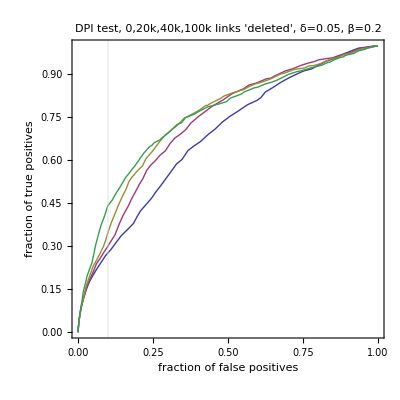

```mathematica
ListPlot[GenerateROCsmart/@adjAtestList,Joined->True,GridLines->{{0.1},{}},Axes->False,AspectRatio->1,FrameLabel->{"fraction of false positives","fraction of true positives"},PlotLabel->"DPI test, 0,20k,40k,100k links 'deleted', δ=0.05, β=0.2",PlotRange->All]
```

```mathematica
Print[<<"pars_iteration0.mx"];
```

{executable→teglobalsim,iteration→1,size→100,rawdatabins→255,bins→5,cutoff→-1,globalbins→3,samples→359951,p→1,noise→0,tauF→20,OverrideRescalingQ→0,HighPassFilterQ→1,InstantFeedbackTermQ→1,inputfile→../../Simulationen/NEST/calciumbursts2/Paris/RandomTopology/noisefree_rawCalcium_uchar_20ms.dat,outputfile→Paris/RandomTopology/adjA_iteration0.mx}

```mathematica
xROC3D=Flatten[Table[{i+1,xROClist⟦i,x,1⟧,xROClist⟦i,x,2⟧},{i,Length@xROClist},{x,101}],1];
```

```mathematica
ListPlot3D[xROC3D,AspectRatio->1,ColorFunction->"AvocadoColors",ImageSize->Medium]
```

```mathematica
xdata=DeleteCases[Sort@Flatten[Table[{adjA⟦ii,jj⟧,adjAtest⟦ii,jj⟧},{ii,Length@adjA},{jj,Length@adjA}],1],{0,0.0}];
(* test if exactly the diagonal elements have been deleted *)
If[Length@xdata!=Length@adjA*(Length[adjA]-1),Print@Length@xdata;Abort[]];
xhistodata={Last@Transpose@Cases[xdata,{0,_}],Last@Transpose@Cases[xdata,{1,_}]};Histogram[xhistodata,ImageSize->Large]
```

```mathematica
tenpercent={};
For[i=1,i≤33,i++,
index=1;
While[xROClist⟦i,index,1⟧>0.2,index++];
AppendTo[tenpercent,{1+i,xROClist⟦i,index,2⟧}]
];
```

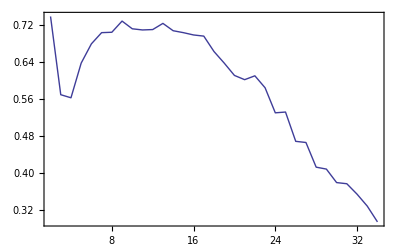

```mathematica
ListPlot[tenpercent,Joined->True]
```

### improve reconstruction using DPI - the ARACHNE two thresholds way

```mathematica
adjAtest-=Min@adjAtest;
adjAtest/=Max@adjAtest;
```

```mathematica
Histogram@Flatten@adjAtest
```

```mathematica
ImbalanceIndex[AB_,ACx_,BC_]:=Min[1,(2 ACx)/(AB+BC)];
imbalanceArray=Table[0,{size/.pars},{size/.pars},{size/.pars}];
(* go through the triples exaustively, and save imbalace index *)
For[nodeA=1,nodeA≤size/.pars,nodeA++,
ShowStatus["running: nodeA = "<>ToString@nodeA];
For[nodeB=1,nodeB≤size/.pars,nodeB++,
For[nodeC=1,nodeC≤size/.pars,nodeC++,
(* if the nodes are really a triple *)
If[(nodeA≠nodeB)&&(nodeA≠nodeC)&&(nodeB≠nodeC),
imbalanceArray⟦nodeA,nodeB,nodeC⟧=ImbalanceIndex[adjAtest⟦nodeA,nodeB⟧,adjAtest⟦nodeA,nodeC⟧,adjAtest⟦nodeB,nodeC⟧]
];
]]];
Clear[nodeA,nodeB,nodeC];
ShowStatus["done."];
```

```mathematica
Histogram@Flatten@imbalanceArray
```

```mathematica
Single2DROCpoint[xadjA_,tPresent_,tImbalanced_]:=Module[{ii,jj,nodeA,nodeB,nodeC,modifiedA,xdata,xP,xTP,xN,xFP,β=0.5,xmaxi},
modifiedA=xadjA;
(* go through the triples exaustively *)
For[nodeA=1,nodeA≤size/.pars,nodeA++,
(* ShowStatus["running: nodeA = "<>ToString@nodeA]; *)
For[nodeB=1,nodeB≤size/.pars,nodeB++,
If[(xadjA⟦nodeA,nodeB⟧>tPresent)||(xadjA⟦nodeB,nodeA⟧>tPresent),
For[nodeC=1,nodeC≤size/.pars,nodeC++,
(* if the nodes are really a triple *)
If[(nodeA≠nodeB)&&(nodeA≠nodeC)&&(nodeB≠nodeC),
(* examine AC *)
If[(xadjA⟦nodeA,nodeB⟧>tPresent)&&(xadjA⟦nodeA,nodeC⟧>tPresent)&&(xadjA⟦nodeB,nodeC⟧>tPresent),
If[imbalanceArray⟦nodeA,nodeB,nodeC⟧<tImbalanced,modifiedA⟦nodeA,nodeC⟧=β*modifiedA⟦nodeA,nodeC⟧]
];
(* examine CA *)
If[(xadjA⟦nodeC,nodeB⟧>tPresent)&&(xadjA⟦nodeB,nodeA⟧>tPresent)&&(xadjA⟦nodeC,nodeA⟧>tPresent),
If[imbalanceArray⟦nodeC,nodeB,nodeA⟧<tImbalanced,modifiedA⟦nodeC,nodeA⟧=β*modifiedA⟦nodeC,nodeA⟧]
];
]];
]]];

xdata=DeleteCases[Flatten[Table[If[ii≠jj,{adjA⟦ii,jj⟧,modifiedA⟦ii,jj⟧},{"nix"}],{ii,Length@adjA},{jj,Length@adjA}],1],{"nix"}];
xP=Length@Cases[xdata,{1,_}];
xmaxi=Max@Flatten@modifiedA;
xTP=Length@Cases[xdata,{1,_?((#>tPresent*xmaxi)&)}];
xN=Length@Cases[xdata,{0,_}];
xFP=Length@Cases[xdata,{0,_?((#>tPresent*xmaxi)&)}];
N@{xFP/xN,xTP/xP}
]
```

```mathematica
x3Ddata=Table[{"leer"},{21},{21}];
For[tPresent=0,tPresent≤20,tPresent++,
For[tImbalanced=0,tImbalanced≤20,tImbalanced++,
tP=tPresent/20.;
tI=tImbalanced/20.;
ShowStatus["running: tPresent = "<>ToString@tP<>", tImbalanced = "<>ToString@tI<>" ..."];
x3Ddata⟦tPresent+1,tImbalanced+1⟧=Flatten@{tI,Single2DROCpoint[adjAtest,tP,tI]};
]];
Clear[tp,tI,tPresent,tImbalanced];
x3Ddata=DeleteCases[Flatten[x3Ddata,1],{"leer"}];
ShowStatus["done"];
```

```mathematica
Single2DROCpoint[adjAtest,0.5,0.5]
```

{0.00149425,0.0766667}

```mathematica
ListPlot3D[x3Ddata]
```

-Graphics3D-

```mathematica
x3Ddata
```

```mathematica
xtest={1,2,3};
{a,#}&/@xtest
```

{{a,1},{a,2},{a,3}}

```mathematica
size/.pars
```

100

```mathematica
ImbalanceIndex[AB_,ACx_,BC_]:=Min[1,(2 ACx)/(AB+BC)];
GenerateImbalanceArray[xadjA_]:=Module[{nodeA,nodeB,nodeC,imbalanceArray},
imbalanceArray=Table[0,{size/.pars},{size/.pars},{size/.pars}];
(* go through the triples exaustively, and save imbalance index *)
For[nodeA=1,nodeA≤size/.pars,nodeA++,
ShowStatus["generating imbalanceArray: nodeA = "<>ToString@nodeA];
For[nodeB=1,nodeB≤size/.pars,nodeB++,
For[nodeC=1,nodeC≤size/.pars,nodeC++,
(* if the nodes are really a triple *)
If[(nodeA≠nodeB)&&(nodeA≠nodeC)&&(nodeB≠nodeC),
imbalanceArray⟦nodeA,nodeB,nodeC⟧=ImbalanceIndex[xadjA⟦nodeA,nodeB⟧,xadjA⟦nodeA,nodeC⟧,xadjA⟦nodeB,nodeC⟧]
];
]]];
Return@imbalanceArray
];

Generate2DROCsmart[xadjA_]:=Generate2DROCsmart[xadjA,0.04];
Generate2DROCsmart[xadjA_,maxdist_]:=Module[{ii,steps,data3D={},imbalanceArray={}},
imbalanceArray=GenerateImbalanceArray[xadjA];
steps=Ceiling[1/maxdist];
For[ii=0,ii≤steps,ii++,
AppendTo[data3D,{ii/steps,#}&/@Generate2DROCsmartInner[xadjA,imbalanceArray,N[ii/steps],maxdist]];
];
ShowStatus["done."];
Return[Partition[Flatten@data3D,3]] (* hack *)
];

Generate2DROCsmartInner[xadjA_,imbalanceArray_,tImbalanced_,maxdist_]:=Module[{xdata,xmin,xmax,xROCpoints,oldRL},
xROCpoints={{0,0},{1,1}};
xdata=DeleteCases[Flatten[Table[If[ii≠jj,{adjA⟦ii,jj⟧,xadjA⟦ii,jj⟧},{"nix"}],{ii,size/.pars},{jj,size/.pars}],1],{"nix"}];
(* test if exactly the diagonal elements have been deleted *)
If[Length@xdata≠(size*(size-1))/.pars,Print["Warning: length="<>ToString@Length@xdata];];

xmin=N@Min@Last@Transpose@xdata;
xmax=N@Max@Last@Transpose@xdata;
If[xmax-xmin<10^-9,Abort[]];
oldRL=$RecursionLimit;
$RecursionLimit=1000;
xROCpoints=Generate2DROCrecursive[xadjA,imbalanceArray,{0,0},xmax,{1,1},xmin,xROCpoints,maxdist,tImbalanced];
$RecursionLimit=oldRL;
Return@Sort@xROCpoints
];

Generate2DROCrecursive[xadjA_,imbalanceArray_,left_,xmax_,right_,xmin_,xROCpoints_,maxDist2D_,tImbalanced_]:=Module[{tPresent,xP,xTP,xN,xFP,xROCpointsLocal,middle,nodeA,nodeB,nodeC,modifiedA,β=0.8,xdata,xmaxi},
xROCpointsLocal=xROCpoints;
(* go through all possible threshold values and compute the ROC data points *)
tPresent=N@((xmin+xmax)/2);
ShowStatus["Generate2DROCrecursive: tPresent = "<>ToString@N@tPresent<>", tImbalanced = "<>ToString@N@tImbalanced<>" ..."];
modifiedA=xadjA;
(* go through the triples exaustively *)
For[nodeA=1,nodeA≤size/.pars,nodeA++,
(* ShowStatus["running: nodeA = "<>ToString@nodeA]; *)
For[nodeB=1,nodeB≤size/.pars,nodeB++,
If[(xadjA⟦nodeA,nodeB⟧>tPresent)||(xadjA⟦nodeB,nodeA⟧>tPresent),
For[nodeC=1,nodeC≤size/.pars,nodeC++,
(* if the nodes are really a triple *)
If[(nodeA≠nodeB)&&(nodeA≠nodeC)&&(nodeB≠nodeC),
(* examine AC *)
If[(xadjA⟦nodeA,nodeB⟧>tPresent)&&(xadjA⟦nodeA,nodeC⟧>tPresent)&&(xadjA⟦nodeB,nodeC⟧>tPresent),
If[imbalanceArray⟦nodeA,nodeB,nodeC⟧<tImbalanced,modifiedA⟦nodeA,nodeC⟧=β*modifiedA⟦nodeA,nodeC⟧]
];
(* examine CA *)
If[(xadjA⟦nodeC,nodeB⟧>tPresent)&&(xadjA⟦nodeB,nodeA⟧>tPresent)&&(xadjA⟦nodeC,nodeA⟧>tPresent),
If[imbalanceArray⟦nodeC,nodeB,nodeA⟧<tImbalanced,modifiedA⟦nodeC,nodeA⟧=β*modifiedA⟦nodeC,nodeA⟧]
];
]];
]]];

xdata=DeleteCases[Flatten[Table[If[ii≠jj,{adjA⟦ii,jj⟧,modifiedA⟦ii,jj⟧},{"nix"}],{ii,size/.pars},{jj,size/.pars}],1],{"nix"}];
xP=Length@Cases[xdata,{1,_}];
xmaxi=Max@Flatten@modifiedA;
xTP=Length@Cases[xdata,{1,_?((#>tPresent)&)}];
xN=Length@Cases[xdata,{0,_}];
xFP=Length@Cases[xdata,{0,_?((#>tPresent)&)}];
middle=N@{xFP/xN,xTP/xP};
AppendTo[xROCpointsLocal,middle];

If[Length@Cases[xdata,{_,_?((#>xmin)&&(#<xmax)&)}]>1,
If[Norm[middle-left]>maxDist2D,
xROCpointsLocal=Generate2DROCrecursive[xadjA,imbalanceArray,left,xmax,middle,tPresent,xROCpointsLocal,maxDist2D,tImbalanced]];
If[Norm[right-middle]>maxDist2D,
xROCpointsLocal=Generate2DROCrecursive[xadjA,imbalanceArray,middle,tPresent,right,xmin,xROCpointsLocal,maxDist2D,tImbalanced]];
];
Return@xROCpointsLocal
];
```

```mathematica
x3Ddata=Generate2DROCsmart[adjAtest,0.35];
```

```mathematica
ListPlot3D[x3Ddata2,Mesh->10,MeshShading->{{Blue,Blue},{Pink,Pink}}]
```

```mathematica
ImbalanceIndex[AB_,ACx_,BC_]:=Min[1,(2 ACx)/(AB+BC)];
GenerateImbalanceArray[xadjA_]:=Module[{nodeA,nodeB,nodeC,imbalanceArray},
imbalanceArray=Table[0,{size/.pars},{size/.pars},{size/.pars}];
(* go through the triples exaustively, and save imbalace index *)
For[nodeA=1,nodeA≤size/.pars,nodeA++,
ShowStatus["generating imbalanceArray: nodeA = "<>ToString@nodeA];
For[nodeB=1,nodeB≤size/.pars,nodeB++,
For[nodeC=1,nodeC≤size/.pars,nodeC++,
(* if the nodes are really a triple *)
If[(nodeA≠nodeB)&&(nodeA≠nodeC)&&(nodeB≠nodeC),
imbalanceArray⟦nodeA,nodeB,nodeC⟧=ImbalanceIndex[xadjA⟦nodeA,nodeB⟧,xadjA⟦nodeA,nodeC⟧,xadjA⟦nodeB,nodeC⟧]
];
]]];
Return@imbalanceArray
];

Generate2DROCsmart2[xadjA_]:=Generate2DROCsmart2[xadjA,0.04];
Generate2DROCsmart2[xadjA_,maxdist_]:=Module[{ii,steps,data3D={},imbalanceArray={}},
imbalanceArray=GenerateImbalanceArray[xadjA];
steps=Ceiling[1/maxdist];
For[ii=0,ii≤steps,ii++,
AppendTo[data3D,{ii/steps,#}&/@Generate2DROCsmartInner2[xadjA,imbalanceArray,N[ii/steps],maxdist]];
];
ShowStatus["done."];
Return[Partition[Flatten@data3D,3]] (* hack *)
];

(* this is for the color rasterplots later ("2Dbinning" etc.) *)
GenerateSingleCurveOf2DROCsmart2[xadjA_,maxdist_,tImbalanced_]:=Module[{data3D={},imbalanceArray={}},
imbalanceArray=GenerateImbalanceArray[xadjA];
AppendTo[data3D,Generate2DROCsmartInner2[xadjA,imbalanceArray,tImbalanced,maxdist]];
ShowStatus["done."];
Return[Partition[Flatten@data3D,3]] (* hack *)
];

Generate2DROCsmartInner2[xadjA_,imbalanceArray_,tImbalanced_,maxdist_]:=Module[{xdata,xmin,xmax,xROCpoints,oldRL},
xROCpoints={{0,0},{1,1}};
xdata=DeleteCases[Flatten[Table[If[ii≠jj,{adjA⟦ii,jj⟧,xadjA⟦ii,jj⟧},{"nix"}],{ii,size/.pars},{jj,size/.pars}],1],{"nix"}];
(* test if exactly the diagonal elements have been deleted *)
If[Length@xdata≠(size*(size-1))/.pars,Print["Warning: length="<>ToString@Length@xdata];];

xmin=N@Min@Last@Transpose@xdata;
xmax=N@Max@Last@Transpose@xdata;
If[xmax-xmin<10^-9,Abort[]];
oldRL=$RecursionLimit;
$RecursionLimit=1000;
xROCpoints=Generate2DROCrecursive2[xadjA,imbalanceArray,{0,0},xmax,{1,1},xmin,xROCpoints,maxdist,tImbalanced];
$RecursionLimit=oldRL;
Return@Sort@xROCpoints
];

Generate2DROCrecursive2[xadjA_,imbalanceArray_,left_,xmax_,right_,xmin_,xROCpoints_,maxDist2D_,tImbalanced_]:=Module[{tPresent,xP,xTP,xN,xFP,xROCpointsLocal,middle,nodeA,nodeB,nodeC,modifiedA,βProxy=0.95,βIndirect=0.95,xdata,xmaxi},
xROCpointsLocal=xROCpoints;
(* go through all possible threshold values and compute the ROC data points *)
tPresent=N@((xmin+xmax)/2);
ShowStatus["Generate2DROCrecursive: tPresent = "<>ToString@N@tPresent<>", tImbalanced = "<>ToString@N@tImbalanced<>" ..."];
modifiedA=xadjA;
(* go through the triples exaustively *)
For[nodeA=1,nodeA≤size/.pars,nodeA++, 
(* ShowStatus["running: nodeA = "<>ToString@nodeA]; *)
For[nodeB=1,nodeB≤size/.pars,nodeB++,
If[(xadjA⟦nodeA,nodeB⟧>tPresent)||(xadjA⟦nodeB,nodeA⟧>tPresent),
For[nodeC=1,nodeC≤size/.pars,nodeC++,
(* if the nodes are really a triple *)
If[(nodeA≠nodeB)&&(nodeA≠nodeC)&&(nodeB≠nodeC),
(* examine AC - proxy motif *)
If[(xadjA⟦nodeA,nodeB⟧>tPresent)&&(xadjA⟦nodeA,nodeC⟧>tPresent)&&(xadjA⟦nodeB,nodeC⟧>tPresent),
If[imbalanceArray⟦nodeA,nodeB,nodeC⟧<tImbalanced,modifiedA⟦nodeA,nodeC⟧=βProxy*modifiedA⟦nodeA,nodeC⟧]
];
(* examine AC - indirect motif *)
If[(xadjA⟦nodeA,nodeC⟧>tPresent)&&(xadjA⟦nodeB,nodeA⟧>tPresent)&&(xadjA⟦nodeB,nodeC⟧>tPresent),
If[(xadjA⟦nodeA,nodeC⟧<xadjA⟦nodeB,nodeA⟧)&&(xadjA⟦nodeA,nodeC⟧<xadjA⟦nodeB,nodeC⟧),modifiedA⟦nodeA,nodeC⟧=βIndirect*modifiedA⟦nodeA,nodeC⟧];
];
(* examine CA - proxy motif *)
If[(xadjA⟦nodeC,nodeB⟧>tPresent)&&(xadjA⟦nodeB,nodeA⟧>tPresent)&&(xadjA⟦nodeC,nodeA⟧>tPresent),
If[imbalanceArray⟦nodeC,nodeB,nodeA⟧<tImbalanced,modifiedA⟦nodeC,nodeA⟧=βProxy*modifiedA⟦nodeC,nodeA⟧]
];
(* examine CA - indirect motif *)
If[(xadjA⟦nodeC,nodeA⟧>tPresent)&&(xadjA⟦nodeB,nodeA⟧>tPresent)&&(xadjA⟦nodeB,nodeC⟧>tPresent),
If[(xadjA⟦nodeC,nodeA⟧<xadjA⟦nodeB,nodeA⟧)&&(xadjA⟦nodeC,nodeA⟧<xadjA⟦nodeB,nodeC⟧),modifiedA⟦nodeC,nodeA⟧=βIndirect*modifiedA⟦nodeC,nodeA⟧];
];
]];
]]];

xdata=DeleteCases[Flatten[Table[If[ii≠jj,{adjA⟦ii,jj⟧,modifiedA⟦ii,jj⟧},{"nix"}],{ii,size/.pars},{jj,size/.pars}],1],{"nix"}];
xP=Length@Cases[xdata,{1,_}];
xmaxi=Max@Flatten@modifiedA;
xTP=Length@Cases[xdata,{1,_?((#>tPresent)&)}];
xN=Length@Cases[xdata,{0,_}];
xFP=Length@Cases[xdata,{0,_?((#>tPresent)&)}];
middle=N@{xFP/xN,xTP/xP};
AppendTo[xROCpointsLocal,middle];

If[Length@Cases[xdata,{_,_?((#>xmin)&&(#<xmax)&)}]>1,
If[Norm[middle-left]>maxDist2D,
xROCpointsLocal=Generate2DROCrecursive2[xadjA,imbalanceArray,left,xmax,middle,tPresent,xROCpointsLocal,maxDist2D,tImbalanced]];
If[Norm[right-middle]>maxDist2D,
xROCpointsLocal=Generate2DROCrecursive2[xadjA,imbalanceArray,middle,tPresent,right,xmin,xROCpointsLocal,maxDist2D,tImbalanced]];
];
Return@xROCpointsLocal
];
```

```mathematica
x3Ddata=Generate2DROCsmart2[adjAtest,0.2];
```

$Aborted

```mathematica
ListPlot3D[x3Ddata2,Mesh->10,MeshShading->{{Blue,Blue},{Pink,Pink}}]
```

### DPI for color rasterplots

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/Paris/2DbinningLaggedInt/Random";
SetDirectory@basedir;
```

```mathematica
startii=0;
endii=3;
xstarttime=AbsoluteTime[];
x10percentlist=AUClist=Table[{},{endii-startii+1}];
For[ii=startii,ii≤endii,ii++,
ShowStatus["ii = "<>ToString@ii<>", ETA "<>ETA[ii-startii,endii-startii+1,xstarttime]];
xadjA=Get["adjA_iteration"<>ToString@ii<>".mx"]⟦All,All,1⟧;
parsstring=Get["pars_iteration"<>ToString@ii<>".mx"];
(* fn=Interpolation[ReduceForInterpolation@N@GenerateROCsmart@xadjA,InterpolationOrder->1]; *)
fn=Interpolation[ReduceForInterpolation@N@GenerateSingleCurveOf2DROCsmart2[xadjA,0.04,0.5],InterpolationOrder->1];

x10percentlist⟦ii-startii+1⟧={bins/.parsstring,globalbins/.parsstring,fn[0.1]};
AUClist⟦ii-startii+1⟧={bins/.parsstring,globalbins/.parsstring,NIntegrate[fn[x],{x,0,1}]};
];
ShowStatus["done."];
Clear[xstarttime,ii,startii,endii,parsstring,xadjA,fn,ROCpoints];
```

Power::infy: Infinite expression 1/0.` encountered.

```mathematica
testadjA=Get["adjA_iteration31.mx"]⟦All,All,1⟧;
```

```mathematica
GenerateSingleCurveOf2DROCsmart2[testadjA,0.04,0.25]
```

{{0,0,0.0275862},{0.0166667,0.0598851,0.0383333},{0.0816092,0.0525,0.105977},{0.0658333,0.128046,0.0866667},{0.148736,0.101667,0.167356},{0.1225,0.198506,0.146667},{0.228391,0.168333,0.258276},{0.193333,0.272644,0.204167},{0.278046,0.213333,0.281839},{0.215833,0.284368,0.220833},{0.284828,0.2225,0.284828},{0.2225,0.285057,0.2225},{0.285287,0.223333,0.285287},{0.223333,1,1}}

```mathematica
(* save results *)
x10percentlist>>"x10percentlist.mx";
AUClist>>"AUClist.mx";
```

```mathematica
(* load results *)
x10percentlist=<<"x10percentlist.mx";
AUClist=<<"AUClist.mx";
```

```mathematica
x10percentlist
AUClist
```

```mathematica
ListContourPlot[x10percentlist,PlotLabel->"TP rate at 10% FP (Random)",ContourLabels->Automatic,Contours->Automatic,FrameLabel->{"localbins","globalbins"}]
```

```mathematica
(* generate arrayplot from the data above, aussuming we start at 1 *)
xmax=Max@x10percentlist⟦All,1⟧;
ymax=Max@x10percentlist⟦All,1⟧;
x10percentlist2D=AUClist2D=Table[0,{xmax},{ymax}];
(x10percentlist2D⟦First@#,Second@#⟧=Third@#)&/@x10percentlist;
(AUClist2D⟦First@#,Second@#⟧=Third@#)&/@AUClist;

ArrayPlot[x10percentlist2D,ColorFunction->"SunsetColors",FrameLabel->{"localbins","globalbins"},PlotLabel->"10% mark (Leo., Int,HP,noIF, range: "<>ToString@Min@x10percentlist2D<>" - "<>ToString@Max@x10percentlist2D<>")",FrameTicks->Automatic]
ArrayPlot[AUClist2D,ColorFunction->"SunsetColors",FrameLabel->{"localbins","globalbins"},PlotLabel->"AUC (range: "<>ToString@Min@AUClist2D<>" - "<>ToString@Max@AUClist2D<>")",FrameTicks->Automatic]
Clear[xmax,ymax];
```

```mathematica
GenerateSingleCurveOf2DROCsmart2[xadjA_,maxdist_,tImbalanced_]
```

## MiniTopologyTests - style examinantion

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/MiniTopologyTests";
experiment="b";
```

```mathematica
SetDirectory@basedir;
xCORlist={};
SetupCorAdjA;
For[i=0,i≤15,i++,
xtemp=<<("adjA_iteration"<>ToString@i<>"_"<>experiment<>".mx");
xpars=<<("pars_iteration"<>ToString@i<>"_"<>experiment<>".mx");
ShowStatus["i = "<>ToString[i]<>"..."];
AppendTo[xCORlist,{tauF/.xpars,bins/.xpars,FindCorAdjA@xtemp}];
];
(*Print[Length@xCORlist];*)
ShowStatus["done."];
Clear[i,xtemp,xpars];
```

```mathematica
ListPlot3D[xCORlist,PlotLabel->experiment]
```

```mathematica
Histogram3D[xdata,(*{Automatic,{0.002}},*)PlotRange->All,ImageSize->Large(*,PlotLabel->xfilename*)]
```

## examine iterated TE

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/iterated_test";
SetDirectory@basedir;
```

```mathematica
xtemp=<<"adjA_iteration0.mx";
```

```mathematica
xExistList=Last@Transpose@Cases[GetConnections@adjA,{1,_}]
```

{7,9,10,15,38,49,63,65,74,75}

```mathematica
%-1
```

{6,8,9,14,37,48,62,64,73,74}

```mathematica
xNonExistList=Complement[Range[2,100],xExistList]
```

{2,3,4,5,6,8,11,12,13,14,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,39,40,41,42,43,44,45,46,47,48,50,51,52,53,54,55,56,57,58,59,60,61,62,64,66,67,68,69,70,71,72,73,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

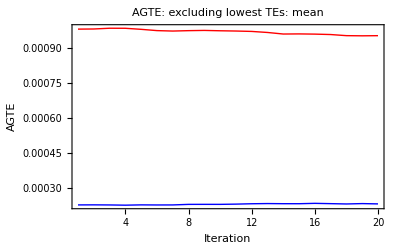

```mathematica
endindex=20;
ListPlot[Flatten[{xtemp⟦xExistList,1;;endindex⟧,xtemp⟦xNonExistList,1;;endindex⟧},1],Joined->True,PlotStyle->{Red,Blue},FrameLabel->{"Iteration","AGTE"},PlotRange->All,PlotLabel->"AGTE: excluding lowest TEs"]
ListPlot[{Mean@xtemp⟦xExistList,1;;endindex⟧,Mean@xtemp⟦xNonExistList,1;;endindex⟧},Joined->True,PlotStyle->{Red,Blue},FrameLabel->{"Iteration","AGTE"},PlotRange->All,PlotLabel->"AGTE: excluding lowest TEs: mean"]
```

## examine TE reconstruction of live data

### set directories and load parameters

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/";

outputdir="Olav0816A/2DConditioned/";
inputdir="../../Imaging/Olav0816A/";
inputfile="xresponse_255bins.dat";

SetDirectory[basedir<>inputdir];
poslist=<<"pos.mx";
pars={size->Length@poslist};
SetDirectory[basedir<>outputdir];
```

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/";

outputdir="0811B-GEI/2DbinningCond/";
inputdir="../../Imaging/0811B-GEI/";
inputfile="xresponse_255bins.dat";

SetDirectory[basedir<>inputdir];
poslist=<<"pos.mx";
pars={size->Length@poslist};
SetDirectory[basedir<>outputdir];
```

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/";

outputdir="0811B-GE/2DbinningCond/";
inputdir="../../Imaging/0811B-GE/";
inputfile="xresponse_255bins.dat";

SetDirectory[basedir<>inputdir];
poslist=<<"../0811B-GEI/pos.mx";
pars={size->Length@poslist};
SetDirectory[basedir<>outputdir];
```

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/Paris/2DbinningCondSatNoise/Leogang";
SetDirectory@basedir;
```

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/";

outputdir="NewCameraClusters/k1_noIF_noHP";
poslist=<<"~/Desktop/Doktorarbeit/Imaging/NewCameraClusters/pos.mx";
pars={size->Length@poslist};
SetDirectory[basedir<>outputdir];
```

### example plots

```mathematica
ArrayPlot[adjAtest,ColorFunction->"AvocadoColors"]
```

```mathematica
xdata=DeleteCases[Flatten[Table[If[ii≠jj,adjAtest⟦ii,jj⟧,"nix"],{ii,size/.pars},{jj,size/.pars}],1],{"nix"}];
Histogram[xdata]
```

```mathematica
ListPlot[poslist,AspectRatio->1,PlotRange->{{0,1},{0,1}},PlotLabel->"cell positions"]
```

```mathematica
xthresh=0.6;
Print[ToString@Length@Cases[Flatten@adjAtest,_?(#>xthresh&)]<>" connections are above the threshold."];
```

215 connections are above the threshold.

```mathematica
(* generate adjacency matrix *)
adjArec=SparseArray[{},{size/.pars,size/.pars},0];
For[ii=1,ii≤size/.pars,ii++,
For[jj=1,jj≤size/.pars,jj++,
If[adjAtest⟦ii,jj⟧>xthresh,adjArec⟦ii,jj⟧=1]
]];
```

```mathematica
(* normalize positions to fit between 0,0 and 1,1 *)
Min/@Transpose@poslist
Max/@Transpose@poslist

poslist2=(#-Evaluate[Min/@Transpose@poslist]&/@poslist);
poslist2=(0.05+#/(1.1*N@Evaluate[Max/@Transpose@poslist2])&/@poslist2);
```

{1,1}

{204,321}

```mathematica
PlotVectorGraph[poslist2,adjArec,"test"]
```

```mathematica
xcons=GetConnections@adjArec;
xdistances={};
For[ii=1,ii≤Length@xcons,ii++,AppendTo[xdistances,Norm[poslist⟦xcons⟦ii,1⟧⟧-poslist⟦xcons⟦ii,2⟧⟧]]];
Histogram[xdistances,FrameLabel->{"distance / px","#"},PlotLabel->"mean distance: "<>ToString@N@Mean@xdistances]
Clear[ii];
```

### estimate mean distance of random network

```mathematica
poslist:=pos;
```

```mathematica
rnddist=0;
For[ii=1,ii≤size/.pars,ii++,
For[jj=1,jj≤size/.pars,jj++,
If[ii≠jj,rnddist+= Norm[poslist⟦ii⟧-poslist⟦jj⟧]]
]];
MeanRandomDist=rnddist/(size(size-1)/.pars)

Clear[ii,jj,rnddist];
```

0.397358

```mathematica
poslist
```

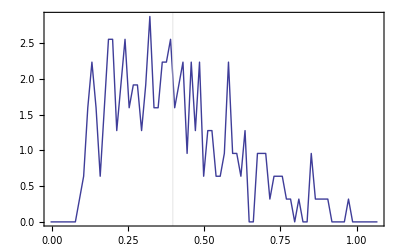

```mathematica
xbins=80;

rnddist=Table[-1,{size(size-1)/.pars}];
count=1;
For[ii=1,ii≤size/.pars,ii++,
For[jj=1,jj≤size/.pars,jj++,
If[ii≠jj,rnddist⟦count++⟧= Norm[poslist⟦ii⟧-poslist⟦jj⟧]]
]];
Clear[ii,jj];

ListPlot[FineHistogramP[rnddist,xbins],Joined->True,PlotRange->All,GridLines->{{MeanRandomDist},{}}]
```

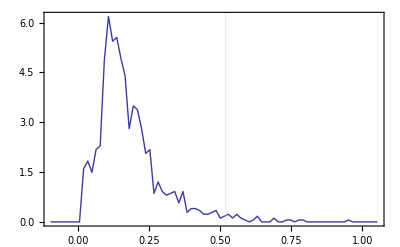

```mathematica
(* if adjacency matri is known *)
xbins=80;

cons=GetConnections@adjA;
distances={};
AppendTo[distances,Norm[poslist⟦First@#⟧-poslist⟦Second@#⟧]]&/@cons;

Clear[cons];

ListPlot[FineHistogramP[distances,xbins],Joined->True,PlotRange->All,GridLines->{{MeanRandomDist},{}}]
```

### make 2 D plot regarding the mean distance of the top connections

```mathematica
startii=0;
endii=399;
xConsFraction=0.10;
xstarttime=AbsoluteTime[];
xMeanDistList=parslist={};

For[ii=startii,ii≤endii,ii++,
ShowStatus["ii = "<>ToString@ii<>", ETA "<>ETA[ii-startii,endii-startii+1,xstarttime]];
If[FileExistsQ["adjA_iteration"<>ToString@ii<>".mx"],
xadjA=Get["adjA_iteration"<>ToString@ii<>".mx"]⟦All,All,1⟧;
parsstring=Get["pars_iteration"<>ToString@ii<>".mx"];

AppendTo[parslist,parsstring];
AppendTo[xMeanDistList,{bins/.parsstring,GlobalConditioningLevel/.parsstring,MeanDistanceInNetwork[xadjA,xConsFraction,poslist]}];
]];
ShowStatus["done."];
Clear[xstarttime,ii,startii,endii,parsstring,xadjA,xdata,xnumber,xrealnumber,xlimit,xmeandist,cfrom,cto];
```

```mathematica
xMeanDistList
```

```mathematica
xMeanDistListnoIFnoHP=xMeanDistList;
```

```mathematica
Histogram@xMeanDistList⟦All,3⟧
```

```mathematica
Max@xMeanDistList⟦All,3⟧
Min@xMeanDistList⟦All,3⟧
```

0.368714

0.331743

```mathematica
(* save results *)
xMeanDistList>>"xMeanDistList.mx";
```

```mathematica
(* load results *)
xMeanDistList=<<"xMeanDistList.mx";
```

```mathematica
ListContourPlot[xMeanDistList,Contours->8,PlotLabel->"cond. below, <d> (10%, Olav0816A, HP&IF)",ContourLabels->All,FrameLabel->{"localbins","conditioning"},PlotRange->All]
```

mean distance of random connectivity: 0.439978

```mathematica
Cfn=Function[{x,y},ColorData["SunsetColors"][y]];
```

```mathematica
xPlotData={xMeanDistListnoIFnoHP,xMeanDistListnoIFHP,xMeanDistListIFnoHP,xMeanDistListIFHP};
xDescription={"no IF, no HP","no IF, with HP","with IF, but no HP","IF and HP"};
```

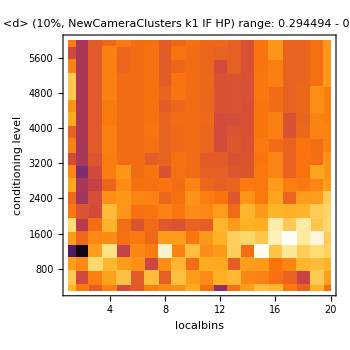
-Graphics-   -Graphics-

```mathematica
(* automatically generate arrayplot from the data above *)
Row[{ListContourPlot[#,InterpolationOrder->0,ColorFunction->"SunsetColors",ColorFunctionScaling->True,FrameLabel->{"localbins","conditioning level"},PlotLabel->"<d> (10%, NewCameraClusters k1 IF HP)\nrange: "<>ToString@Min@Cases[Flatten@#⟦All,3⟧,_Real]<>" - "<>ToString@Max@Cases[Flatten@#⟦All,3⟧,_Real],FrameTicks->Automatic,Contours->Union@#⟦All,3⟧,ImageSize->350],"   ",QuickLegend[#⟦All,3⟧]}]&@xMeanDistList
```

```mathematica
GetName[symbol_]:=ToString@StringDrop[StringDrop[ToString@Unevaluated[symbol],-1],5];
```

```mathematica
Clear@GetName
```

```mathematica
GetName@xPlotData
```

```mathematica
GetName@xMeanDistListnoIFnoHP
```

```mathematica
GetName@xPlotData
```

```mathematica
ToString@Hold@xPlotData
```

Hold[xPlotData]

```mathematica
ToString@StringDrop[StringDrop[ToString@Hold[xPlotData],-1],5]
```

xPlotData

```mathematica
(* automatically generate arrayplot from the data above *)
count=1;
OptimalPars={{{11,Directive[Darker@Green,Thickness[0.06]]}},{{3300,Directive[Darker@Green,Thickness[0.06]]}}};
GraphicsRow[Flatten@{(ListContourPlot[#,InterpolationOrder->0,ColorFunction->Cfn,ColorFunctionScaling->False,FrameLabel->{"localbins","conditioning level"},PlotLabel->"<d> (10%, NewCameraClusters)\n"<>xDescription⟦count++⟧<>"\nrange: "<>ToString@Min@Cases[Flatten@#⟦All,3⟧,_Real]<>" - "<>ToString@Max@Cases[Flatten@#⟦All,3⟧,_Real],FrameTicks->Automatic,Contours->Union@#⟦All,3⟧,ImageSize->350,GridLines->OptimalPars]&/@xPlotData),QuickLegend[0,0.5]}]
```

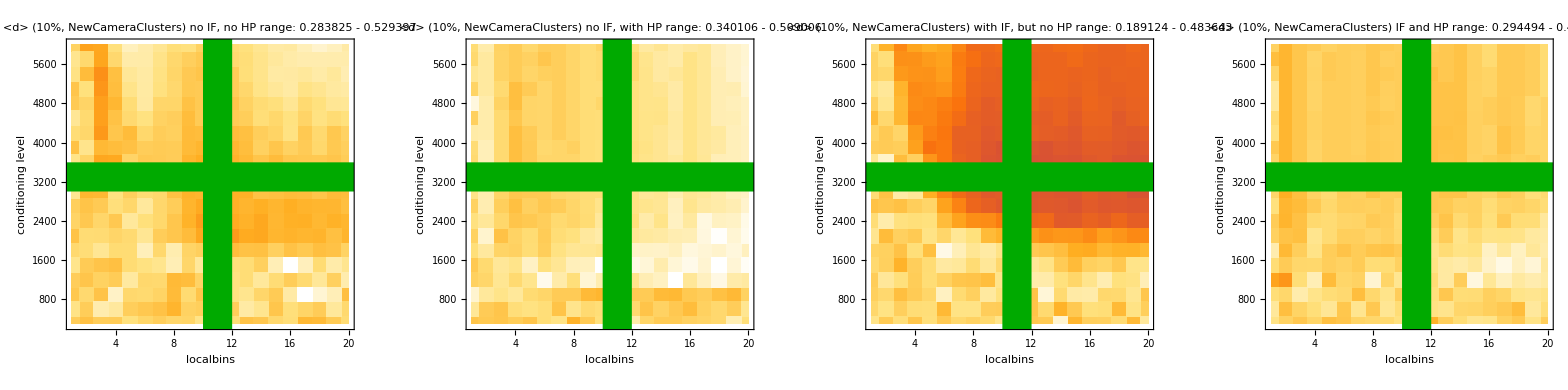

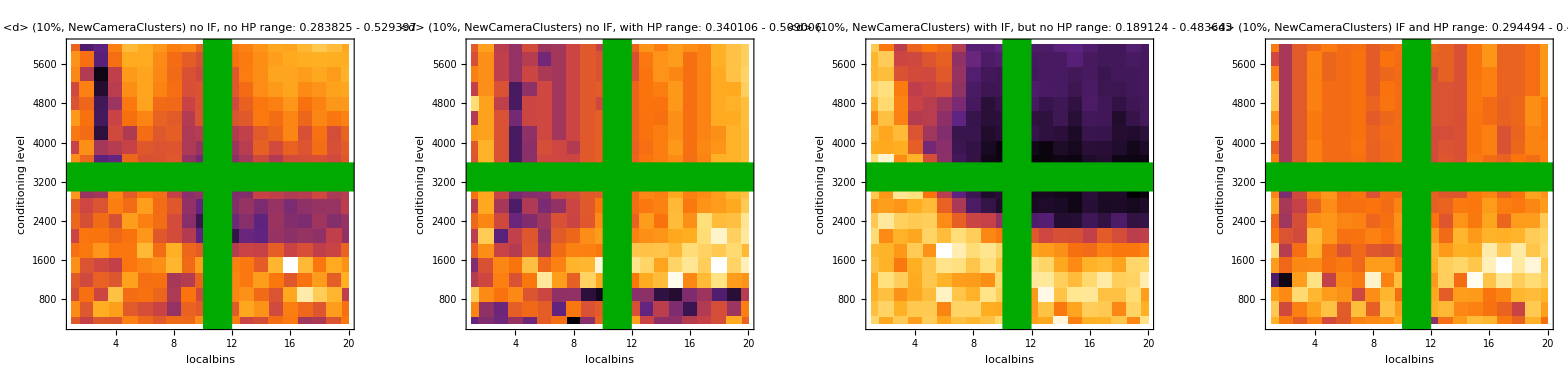

```mathematica
Cfn[x_]:=ColorData["SunsetColors"][2x];
```

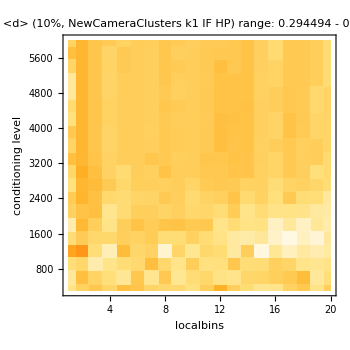
-Graphics-   -Graphics-

```mathematica
(* automatically generate arrayplot from the data above *)
Row[{ListContourPlot[#,InterpolationOrder->0,ColorFunction->Cfn,ColorFunctionScaling->False,FrameLabel->{"localbins","conditioning level"},PlotLabel->"<d> (10%, NewCameraClusters k1 IF HP)\nrange: "<>ToString@Min@Cases[Flatten@#⟦All,3⟧,_Real]<>" - "<>ToString@Max@Cases[Flatten@#⟦All,3⟧,_Real],FrameTicks->Automatic,Contours->Union@#⟦All,3⟧,ImageSize->350],"   ",QuickLegend[0,0.5]}]&@xMeanDistList
```

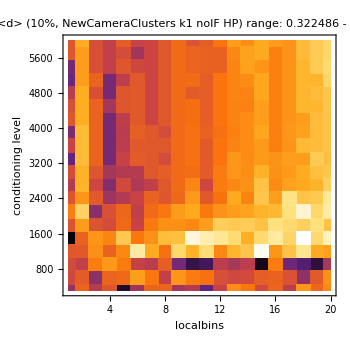
-Graphics-   -Graphics-

```mathematica
(* automatically generate arrayplot from the data above *)
Row[{ListContourPlot[#,InterpolationOrder->0,ColorFunction->"SunsetColors",ColorFunctionScaling->True,FrameLabel->{"localbins","conditioning level"},PlotLabel->"<d> (10%, NewCameraClusters k1 noIF HP)\nrange: "<>ToString@Min@Cases[Flatten@#⟦All,3⟧,_Real]<>" - "<>ToString@Max@Cases[Flatten@#⟦All,3⟧,_Real],FrameTicks->Automatic,Contours->Union@#⟦All,3⟧,ImageSize->350],"   ",QuickLegend[#⟦All,3⟧]}]&@xMeanDistList
```

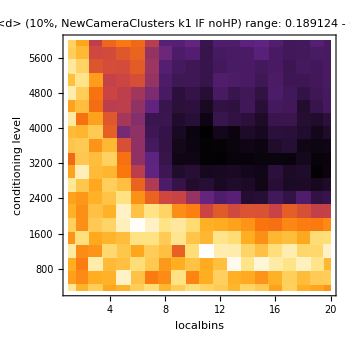
-Graphics-   -Graphics-

```mathematica
(* automatically generate arrayplot from the data above *)
Row[{ListContourPlot[#,InterpolationOrder->0,ColorFunction->"SunsetColors",ColorFunctionScaling->True,FrameLabel->{"localbins","conditioning level"},PlotLabel->"<d> (10%, NewCameraClusters k1 IF noHP)\nrange: "<>ToString@Min@Cases[Flatten@#⟦All,3⟧,_Real]<>" - "<>ToString@Max@Cases[Flatten@#⟦All,3⟧,_Real],FrameTicks->Automatic,Contours->Union@#⟦All,3⟧,ImageSize->350],"   ",QuickLegend[#⟦All,3⟧]}]&@xMeanDistList
```

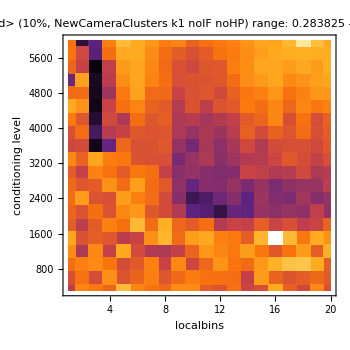
-Graphics-   -Graphics-

```mathematica
(* automatically generate arrayplot from the data above *)
Row[{ListContourPlot[#,InterpolationOrder->0,ColorFunction->"SunsetColors",ColorFunctionScaling->True,FrameLabel->{"localbins","conditioning level"},PlotLabel->"<d> (10%, NewCameraClusters k1 noIF noHP)\nrange: "<>ToString@Min@Cases[Flatten@#⟦All,3⟧,_Real]<>" - "<>ToString@Max@Cases[Flatten@#⟦All,3⟧,_Real],FrameTicks->Automatic,Contours->Union@#⟦All,3⟧,ImageSize->350],"   ",QuickLegend[#⟦All,3⟧]}]&@xMeanDistList
```

### examine P (r | xthresh)

```mathematica
ii=6*20+11;
xadjA=Get["adjA_iteration"<>ToString@ii<>".mx"]⟦All,All,1⟧;
parsstring=Get["pars_iteration"<>ToString@ii<>".mx"]
```

{executable→teglobalsim,iteration→227,size→432,rawdatabins→255,bins→12,cutoff→-1,globalbins→2,samples→25001,StartSampleIndex→1,EndSampleIndex→25000,AvailableSamples→{147,24852},p→1,noise→-1,tauF→40,OverrideRescalingQ→0,HighPassFilterQ→1,InstantFeedbackTermQ→1,saturation→-1,IncludeGlobalSignalQ→1,GenerateGlobalFromFilteredDataQ→0,GlobalConditioningLevel→14,xresponse_255bins.dat→../../Imaging/0811B-GEI/xresponse_255bins.dat,outputfile→0811B-GEI/2DbinningCond/adjA_iteration131.mx,outputparsfile→0811B-GEI/2DbinningCond/pars_iteration131.mx}

```mathematica
ii=12*20+9;
xadjA=Get["adjA_iteration"<>ToString@ii<>".mx"]⟦All,All,1⟧;
parsstring=Get["pars_iteration"<>ToString@ii<>".mx"]
```

```mathematica
xadjA=importlist2⟦1⟧;
```

```mathematica
poslist=pos;
```

```mathematica
xtemp=Table[xx,{xx,0,1,0.01}];
xtemp=Transpose@{xtemp,DiscretizeNew[xtemp,0,1,10]};
ListPlot@xtemp
Clear[xtemp];
```

```mathematica
(* OLD: xlength=2*20;
xbins=2*10;
maxdist=1.4;
CollectedDistances=Table[0,{xlength},{xbins}];
xdata=DeleteCases[Flatten[Table[If[ii≠jj,xadjA⟦ii,jj⟧,"nix"],{ii,size/.pars},{jj,size/.pars}],1],{"nix"}];

For[ii=1,ii≤xlength,ii++,
ShowStatus["ii = "<>ToString@ii];
xConsFraction=N@ii/xlength;
(*xConsFraction={0.05,0.1,0.2,1}⟦ii⟧;*)
xnumber=Round[xConsFraction*Length[xdata]];
xlimit=Sort[Flatten@xdata,Greater]⟦xnumber⟧;

xrealnumber=0;
xtemplist={};
For[cfrom=1,cfrom≤size/.pars,cfrom++,
For[cto=1,cto≤size/.pars,cto++,
If[(cfrom≠cto)&&(xadjA⟦cfrom,cto⟧≥xlimit),AppendTo[xtemplist,N@Norm[poslist⟦cfrom⟧-poslist⟦cto⟧]];
]]];
xtemplist2=DiscretizeNew[xtemplist,0,maxdist,xbins];
For[jj=1,jj≤Length@xtemplist,jj++,CollectedDistances⟦ii,xtemplist2⟦jj⟧⟧++];
];
ShowStatus["done."];
Clear[ii,jj,xdata,xnumber,xrealnumber,xlimit,cfrom,cto]; *)
```

```mathematica
xlength=1/2*20;
xbins=1*20;
maxdist=1.2;
maxrecord=size(size-1)/.pars;

CollectedDistances=Table[0,{xlength},{xbins}];
For[ii=1,ii≤xlength,ii++,
ShowStatus["ii = "<>ToString@ii];
xConsFraction=N@ii/xlength;
xSelectA=ThresholdedFractionA[xadjA,xConsFraction];

recordcount=0;
xtemplist=Table[-1,{maxrecord}];
MapIndexed[If[(#1==1)&&(recordcount<maxrecord),xtemplist⟦++recordcount⟧=N@Norm[poslist⟦#2⟦1⟧⟧-poslist⟦#2⟦2⟧⟧]]&,xSelectA,{2}];
xtemplist=DeleteCases[xtemplist,-1];

xtemplist2=DiscretizeNew[xtemplist,0,maxdist,xbins];
For[jj=1,jj≤Length@xtemplist,jj++,CollectedDistances⟦ii,xtemplist2⟦jj⟧⟧++];
];
ShowStatus["done."];
Clear[ii,jj,xConsFraction,xSelectA,cfrom,cto,xtemplist,xtemplist2];
```

```mathematica
CollectedDistances
```

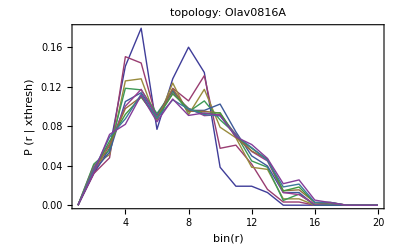

```mathematica
ListPlot[#/(Total@#)&/@CollectedDistances,Joined->True,FrameLabel->{"bin(r)","P (r | xthresh)"},PlotRange->All,PlotLabel->"topology: Olav0816A"]
```

```mathematica
ListPlot3D[#/(Total@#)&/@CollectedDistances,ColorFunction->"SunsetColors",Mesh->False,Filling->False,FillingStyle->Black,AxesLabel->{"bin(r)","xthresh","P(r)"},ImageSize->Large,PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot[#/(Total@#)&/@CollectedDistances,Joined->True,FrameLabel->{"bin(r)","P (r | xthresh)"},PlotRange->All,PlotLabel->"topology: 0811B-GEI"]
```

```mathematica
ListPlot3D[#/(Total@#)&/@CollectedDistances,ColorFunction->"TemperatureMap",Mesh->10,Filling->False,FillingStyle->Black,AxesLabel->{"bin(r)","xthresh","P(r)"},ImageSize->Medium,PlotRange->All]
```

-Graphics3D-

```mathematica
ListContourPlot[#/(Total@#)&/@CollectedDistances,ContourLabels->All,PlotRange->All]
```

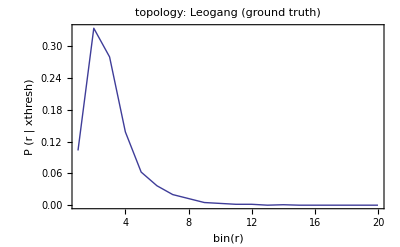

```mathematica
(* in the case of simulations: plot the real P(r) *)
xbins=2*10;
maxdist=1.4;
CollectedDistances=Table[0,{xbins}];

xtemplist=N[Norm[pos⟦#⟦1⟧⟧-pos⟦#⟦2⟧⟧]]&/@GetConnections[adjA];
xtemplist=DiscretizeNew[xtemplist,0,maxdist,xbins];
For[jj=1,jj≤Length@xtemplist,jj++,CollectedDistances⟦xtemplist⟦jj⟧⟧++];

ListPlot[CollectedDistances/(Total@CollectedDistances),Joined->True,FrameLabel->{"bin(r)","P (r | xthresh)"},PlotRange->All,PlotLabel->"topology: Leogang (ground truth)"]
Clear[jj,xtemplist];
```

### examine clustering coefficient

```mathematica
xadjA=importlist2⟦1⟧;
```

```mathematica
xlength=20;
xbins=2*10;
maxdist=1;
CollectedCC=Table[0,{xlength},{xbins}];
xdata=DeleteCases[Flatten[Table[If[ii≠jj,xadjA⟦ii,jj⟧,"nix"],{ii,size/.pars},{jj,size/.pars}],1],{"nix"}];

For[ii=1,ii≤xlength,ii++,
ShowStatus["ii = "<>ToString@ii];
xConsFraction=N@ii/xlength;
(*xConsFraction={0.05,0.1,0.2,1}⟦ii⟧;*)
xnumber=Round[xConsFraction*Length[xdata]];
xlimit=Sort[Flatten@xdata,Greater]⟦xnumber⟧;
xadjAD=Map[If[#>xlimit,1,0]&,xadjA,{2}];

xtemplist2=DiscretizeNew[ClusteringIndexFull@xadjAD,0,maxdist,xbins];
For[jj=1,jj≤Length@xtemplist2,jj++,CollectedCC⟦ii,xtemplist2⟦jj⟧⟧++];
];
ShowStatus["done."];
Clear[ii,jj,xdata,xnumber,xrealnumber,xlimit,cfrom,cto];
```

```mathematica
CollectedCC
```

{{44,28,10,12,1,2,0,0,0,3},{23,23,31,15,4,2,2,0,0,0},{3,17,45,29,6,0,0,0,0,0},{0,6,27,52,14,1,0,0,0,0},{0,0,13,54,31,2,0,0,0,0},{0,0,4,45,47,4,0,0,0,0},{0,0,0,18,75,6,1,0,0,0},{0,0,0,6,70,23,1,0,0,0},{0,0,0,0,41,59,0,0,0,0},{0,0,0,0,8,89,3,0,0,0},{0,0,0,0,0,63,37,0,0,0},{0,0,0,0,0,5,95,0,0,0},{0,0,0,0,0,0,98,2,0,0},{0,0,0,0,0,0,4,96,0,0},{0,0,0,0,0,0,0,100,0,0},{0,0,0,0,0,0,0,1,99,0},{0,0,0,0,0,0,0,0,100,0},{0,0,0,0,0,0,0,0,1,99},{0,0,0,0,0,0,0,0,0,100},{0,0,0,0,0,0,0,0,0,100}}

```mathematica
ClusteringIndexFull@adjA
```

{0.125,0.132937,0.0899471,0.117391,0.146288,0.102871,0.125,0.11976,0.11745,0.133333,0.126482,0.105413,0.128571,0.132275,0.110368,0.131173,0.114286,0.12069,0.141921,0.119128,0.151261,0.121377,0.11244,0.117216,0.12253,0.114545,0.0984043,0.122,0.133971,0.13913,0.123636,0.11008,0.111406,0.10582,0.10814,0.0987654,0.136364,0.123746,0.106491,0.128623,0.119565,0.0872727,0.121377,0.109043,0.124642,0.12963,0.120445,0.136364,0.126984,0.128333,0.126374,0.114035,0.110577,0.116046,0.135802,0.119303,0.119565,0.114058,0.103175,0.123506,0.12381,0.124286,0.141447,0.11745,0.119565,0.133971,0.124224,0.107692,0.121864,0.131429,0.12987,0.141429,0.102871,0.128,0.122222,0.117391,0.136364,0.128676,0.120773,0.116788,0.109524,0.120879,0.1125,0.120805,0.114833,0.13067,0.122507,0.114362,0.114964,0.127737,0.108553,0.123746,0.140873,0.0928571,0.106838,0.114907,0.119816,0.134675,0.102518,0.100671}

```mathematica
TrueCC=Table[0,{xbins}];
xtemp=DiscretizeNew[ClusteringIndexFull@adjA,0,maxdist,xbins];
For[jj=1,jj≤Length@xtemp,jj++,TrueCC⟦xtemp⟦jj⟧⟧++];
ListPlot[TrueCC/(Total@TrueCC),Joined->True,FrameLabel->{"bin(CC)","P (r | xthresh)"},PlotRange->All,PlotLabel->"true CC - topology: Leogang"]
```

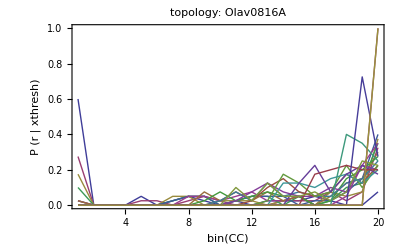

```mathematica
ListPlot[#/(Total@#)&/@CollectedCC,Joined->True,FrameLabel->{"bin(CC)","P (r | xthresh)"},PlotRange->All,PlotLabel->"topology: Olav0816A"]
```

```mathematica
ListPlot3D[#/(Total@#)&/@CollectedCC,ColorFunction->"SunsetColors",Mesh->False,Filling->0,FillingStyle->Black,AxesLabel->{"bin(CC)","xthresh","P(CC)"},ImageSize->Large,PlotRange->All]
```

### are TE values bimodal?

```mathematica
ii=10*20+9;
xadjA=Get["adjA_iteration"<>ToString@ii<>".mx"]⟦All,All,1⟧;
parsstring=Get["pars_iteration"<>ToString@ii<>".mx"]
```

{executable→teglobalsim,iteration→191,size→432,rawdatabins→255,bins→10,cutoff→-1,globalbins→2,samples→25001,StartSampleIndex→1,EndSampleIndex→25000,AvailableSamples→{21727,3272},p→1,noise→-1,tauF→40,OverrideRescalingQ→0,HighPassFilterQ→1,InstantFeedbackTermQ→1,saturation→-1,IncludeGlobalSignalQ→1,GenerateGlobalFromFilteredDataQ→0,GlobalConditioningLevel→22,xresponse_255bins.dat→../../Imaging/0811B-GEI/xresponse_255bins.dat,outputfile→0811B-GEI/2DbinningCond/adjA_iteration209.mx,outputparsfile→0811B-GEI/2DbinningCond/pars_iteration209.mx}

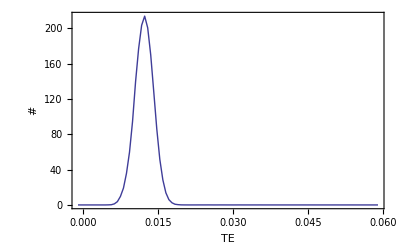

```mathematica
ListPlot[FineHistogram[Flatten@RemoveDiagonal@xadjA,100],Joined->True,PlotRange->All,FrameLabel->{"TE","#"}]
```

```mathematica
Clear@bins
```

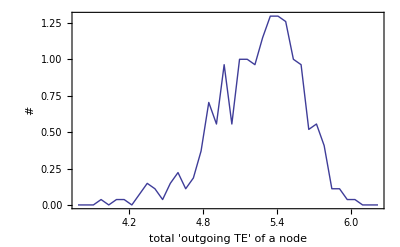

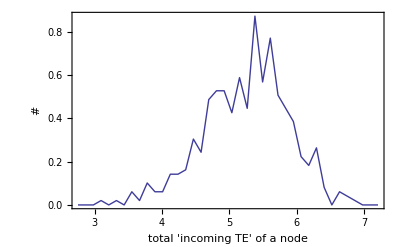

parameters: bins=10, cond. Level=22

```mathematica
ListPlot[FineHistogram[Table[Total@xadjA⟦ii,All⟧,{ii,Length@xadjA}],40],Joined->True,PlotRange->All,FrameLabel->{"total 'outgoing TE' of a node","#"}]
ListPlot[FineHistogram[Table[Total@xadjA⟦All,ii⟧,{ii,Length@xadjA}],40],Joined->True,PlotRange->All,FrameLabel->{"total 'incoming TE' of a node","#"}]
Print["parameters: bins="<>ToString[bins/.parsstring]<>", cond. Level="<>ToString[GlobalConditioningLevel/.parsstring]];
```

### compare different Markov orders

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/";

outputdir="Olav0816A/2DConditionedExtended/";
DataSetID="Olav0816A";
inputdir="../../Imaging/Olav0816A/";
inputfile="xresponse_255bins.dat";

SetDirectory[basedir<>inputdir];
poslist=<<"pos.mx";
pars={size->Length@poslist};
SetDirectory[basedir<>outputdir];
```

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/";

outputdir="0811B-GEI/2DConditionedExtended/";
DataSetID="0811B-GEI";
inputdir="../../Imaging/0811B-GEI/";
inputfile="xresponse_255bins.dat";

SetDirectory[basedir<>inputdir];
poslist=<<"pos.mx";
pars={size->Length@poslist};
SetDirectory[basedir<>outputdir];
```

```mathematica
startii=0;
endii=19;
xConsFraction=0.05;
xstarttime=AbsoluteTime[];
xMeanDistList1=parslist1=xMeanDistList2=parslist2={};

For[ii=startii,ii≤endii,ii+=2,
ShowStatus["ii = "<>ToString@ii<>", ETA "<>ETA[ii-startii,endii-startii+1,xstarttime]];
xadjA1=Get["adjA_iteration"<>ToString@ii<>"_k1.mx"]⟦All,All,1⟧;
xadjA2=Get["adjA_iteration"<>ToString@ii<>"_k2.mx"]⟦All,All,1⟧;
parsstring1=Get["pars_iteration"<>ToString@ii<>"_k1.mx"];
parsstring2=Get["pars_iteration"<>ToString@ii<>"_k2.mx"];

AppendTo[parslist1,parsstring1];
AppendTo[parslist2,parsstring2];
AppendTo[xMeanDistList1,{GlobalConditioningLevel/.parsstring1,MeanDistanceInNetwork[xadjA1,xConsFraction,poslist]}];
AppendTo[xMeanDistList2,{GlobalConditioningLevel/.parsstring2,MeanDistanceInNetwork[xadjA2,xConsFraction,poslist]}];
];
ShowStatus["done."];
Clear[xstarttime,ii,startii,endii,parsstring1,xadjA1,parsstring2,xadjA2];
```

```mathematica
xMeanDistList
```

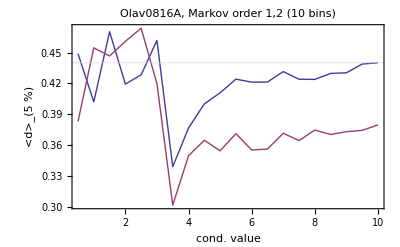

mean dist. of random conn.: 0.439978

mean dist. of top 5% at k=1: 0.339216

mean dist. of top 5% at k=2: 0.301954

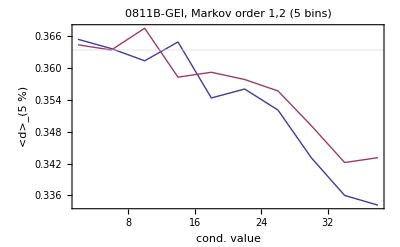

mean dist. of random conn.: 0.363411

mean dist. of top 5% at k=1: 0.334149

mean dist. of top 5% at k=2: 0.342191

```mathematica
ListPlot[{xMeanDistList1,xMeanDistList2},Joined->True,FrameLabel->{"cond. value","<d>_(5  %)"},GridLines->{{},{MeanRandomDist}},PlotLabel->DataSetID<>", Markov order 1,2 (10 bins)"]
Print["mean dist. of random conn.: ",MeanRandomDist];
Print["mean dist. of top 5% at k=1: ",Min@xMeanDistList1⟦All,2⟧];
Print["mean dist. of top 5% at k=2: ",Min@xMeanDistList2⟦All,2⟧];
```

## analyze results of cross - validation

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/Paris/CrossValTest";
SetDirectory@basedir;
```

```mathematica
xindex=0;
importlist=<<("adjA_iteration"<>ToString@xindex<>".mx");
parsstring=<<("pars_iteration"<>ToString@xindex<>".mx");
crossvallist=<<("crossval_iteration"<>ToString@xindex<>".mx");
importlist2=Table[importlist⟦All,All,ii⟧,{ii,Last@Dimensions@importlist}];
Clear[importlist,xindex];
```

```mathematica
ArrayPlot[Total@importlist2,ColorFunction->"AvocadoColors",PlotLabel->"GTE: bins & globalbins: 15"]
```

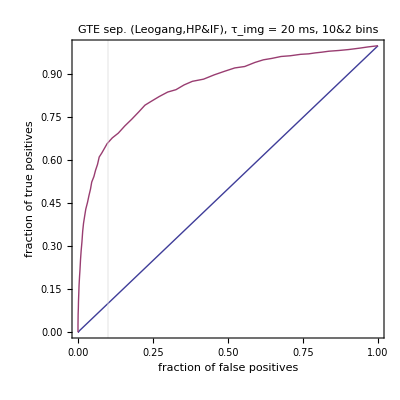

```mathematica
tstring="GTE sep. (Leogang,HP&IF)";
tstring=tstring<>", τ_img = "<>ToString[tauF/.parsstring]<>" ms";
tstring=tstring<>", "<>ToString[bins/.parsstring]<>"&"<>ToString[globalbins/.parsstring]<>" bins";

ListPlot[GenerateROCsmart/@importlist2,Joined->True,GridLines->{{0.1},{}},Axes->False,AspectRatio->1,FrameLabel->{"fraction of false positives","fraction of true positives"},PlotLabel->tstring,PlotRange->All]
Clear[tstring];
```

```mathematica
Print[<<"pars_iteration0.mx"];
```

{executable→teglobalsim,iteration→1,size→100,rawdatabins→255,bins→6,cutoff→-1,globalbins→6,samples→359951,p→1,noise→-1,tauF→20,OverrideRescalingQ→0,HighPassFilterQ→1,InstantFeedbackTermQ→1,AdaptiveBinningQ→0,saturation→-1,IncludeGlobalSignalQ→1,GenerateGlobalFromFilteredDataQ→0,GlobalConditioningLevel→-1,inputfile→../../Simulationen/NEST/calciumbursts2/Paris/LeogangTopology/noisefree_rawCalcium_uchar_20ms.dat,outputfile→Paris/SeparatedTest/adjA_iteration0.mx}

```mathematica
ArrayPlot[crossvallist]
```

### 1 - D plots

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/Paris/CrossValTest";
SetDirectory@basedir;
```

```mathematica
startii=0;
endii=19;
xstarttime=AbsoluteTime[];
x10percentlist=xCrossVallist=Table[{},{endii-startii+1}];
For[ii=startii,ii≤endii,ii++,
ShowStatus["ii = "<>ToString@ii<>", ETA "<>ETA[ii-startii,endii-startii+1,xstarttime]];
xadjA=Get["adjA_iteration"<>ToString@ii<>".mx"]⟦All,All,1⟧;
parsstring=Get["pars_iteration"<>ToString@ii<>".mx"];
crossvallist=<<("crossval_iteration"<>ToString@ii<>".mx");
fn=Interpolation[ReduceForInterpolation@N@GenerateROCsmart@xadjA,InterpolationOrder->1];

x10percentlist⟦ii-startii+1⟧={GlobalConditioningLevel/.parsstring,fn[0.1]};
xCrossVallist⟦ii-startii+1⟧={GlobalConditioningLevel/.parsstring,Mean@Flatten@crossvallist};
];
ShowStatus["done."];
Clear[xstarttime,ii,startii,endii,parsstring,xadjA,crossvallist,ROCpoints];
```

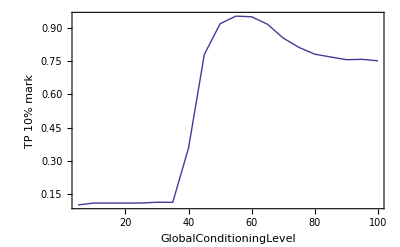

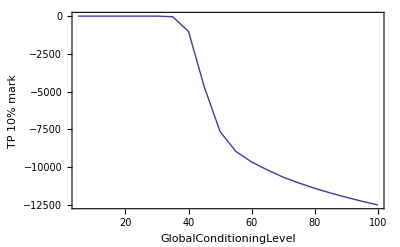

```mathematica
ListPlot[x10percentlist,Joined->True,PlotRange->All,FrameLabel->{"GlobalConditioningLevel","TP 10% mark"}]
ListPlot[xCrossVallist,Joined->True,PlotRange->All,FrameLabel->{"GlobalConditioningLevel","TP 10% mark"}]
```

```mathematica
xCrossVallist
```

{{5,0.},{10,0.},{15,0.},{20,0.},{25,0.},{30,0.},{35,-39.0023},{40,-1018.8},{45,-4701.74},{50,-7653.69},{55,-8969.},{60,-9667.06},{65,-10196.6},{70,-10674.},{75,-11062.5},{80,-11411.4},{85,-11723.},{90,-12007.1},{95,-12273.5},{100,-12512.5}}

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/Paris/CrossValTest/HalfPseudoCount";
SetDirectory@basedir;
```

```mathematica
startii=0;
endii=19;
xstarttime=AbsoluteTime[];
x10percentlist=xCrossVallist=Table[{},{endii-startii+1}];
For[ii=startii,ii≤endii,ii++,
ShowStatus["ii = "<>ToString@ii<>", ETA "<>ETA[ii-startii,endii-startii+1,xstarttime]];
xadjA=Get["adjA_iteration"<>ToString@ii<>".mx"]⟦All,All,1⟧;
parsstring=Get["pars_iteration"<>ToString@ii<>".mx"];
crossvallist=<<("crossval_iteration"<>ToString@ii<>".mx");
fn=Interpolation[ReduceForInterpolation@N@GenerateROCsmart@xadjA,InterpolationOrder->1];

x10percentlist⟦ii-startii+1⟧={GlobalConditioningLevel/.parsstring,fn[0.1]};
xCrossVallist⟦ii-startii+1⟧={GlobalConditioningLevel/.parsstring,Mean@Flatten@crossvallist};
];
ShowStatus["done."];
Clear[xstarttime,ii,startii,endii,parsstring,xadjA,crossvallist,ROCpoints];
```

-Graphics-

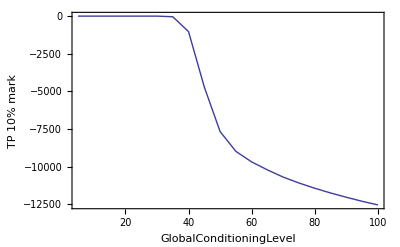

```mathematica
ListPlot[x10percentlist,Joined->True,PlotRange->All,FrameLabel->{"GlobalConditioningLevel","TP 10% mark"}]
ListPlot[xCrossVallist,Joined->True,PlotRange->All,FrameLabel->{"GlobalConditioningLevel","TP 10% mark"}]
```

```mathematica
xCrossVallist
```

{{5,0.},{10,0.},{15,0.},{20,0.},{25,0.},{30,0.},{35,-39.0023},{40,-1018.8},{45,-4701.74},{50,-7653.69},{55,-8969.},{60,-9667.06},{65,-10196.6},{70,-10674.},{75,-11062.5},{80,-11411.4},{85,-11723.},{90,-12007.1},{95,-12273.5},{100,-12512.5}}

```mathematica
xFractionOfSamplesllist={{5,0.00333379},{10,0.0036116},{15,0.0036116},{20,0.0036116},{25,0.0036116},{30,0.00472287},{35,0.365328},{40,8.34947},{45,33.317},{50,51.4589},{55,58.9277},{60,63.0152},{65,66.0529},{70,68.5849},{75,70.7224},{80,72.5674},{85,74.2265},{90,75.6903},{95,77.018},{100,78.249}};
xFractionOfSamplesllist={#⟦1⟧,(#⟦2⟧)/100}&/@xFractionOfSamplesllist;
```

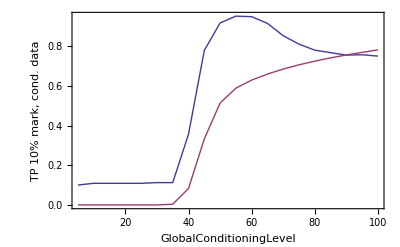

```mathematica
ListPlot[{x10percentlist,xFractionOfSamplesllist},Joined->True,PlotRange->All,FrameLabel->{"GlobalConditioningLevel","TP 10% mark, cond. data"}]
```

```mathematica
Get["pars_iteration0.mx"]
```

{executable→teglobalsim,iteration→1,size→100,rawdatabins→255,bins→10,cutoff→-1,globalbins→2,samples→359951,p→1,noise→-1,tauF→20,OverrideRescalingQ→0,HighPassFilterQ→1,InstantFeedbackTermQ→1,AdaptiveBinningQ→0,saturation→-1,IncludeGlobalSignalQ→1,GenerateGlobalFromFilteredDataQ→0,GlobalConditioningLevel→5,inputfile→../../Simulationen/NEST/calciumbursts2/Paris/LeogangTopology/noisefree_rawCalcium_uchar_20ms.dat,outputfile→Paris/CrossValTest/adjA_iteration0.mx}

```mathematica
xsamples=samples/.Get["pars_iteration0.mx"]
```

359951

```mathematica
xSamplesllist=Floor[xFractionOfSamplesllist.{1,xsamples/2}]
```

{11,16,21,26,31,38,692,15067,60007,92663,106110,113471,118944,123506,127357,130683,133674,136313,138708,140929}

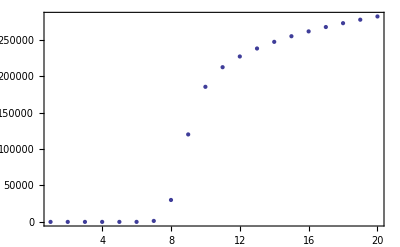

```mathematica
ListPlot@%
```

```mathematica
If[Length@xCrossVallist≠Length@xSamplesllist,Abort[]];
xCrossVallistNormalized=Table[{xCrossVallist⟦ii,1⟧,Exp[xCrossVallist⟦ii,2⟧/xSamplesllist⟦ii⟧]},{ii,Length@xCrossVallist}]
```

{{5,1.},{10,1.},{15,1.},{20,1.},{25,1.},{30,1.},{35,0.945197},{40,0.934617},{45,0.924638},{50,0.920722},{55,0.918948},{60,0.918334},{65,0.917845},{70,0.917204},{75,0.916804},{80,0.916383},{85,0.916037},{90,0.915683},{95,0.915317},{100,0.915042}}

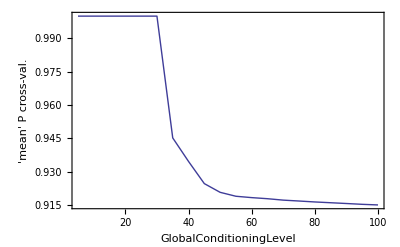

```mathematica
ListPlot[xCrossVallistNormalized,Joined->True,PlotRange->All,FrameLabel->{"GlobalConditioningLevel","'mean' P cross-val."}]
```

### Do 2 D plots

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/Paris/2DbinningCondSatNoise/Random";
SetDirectory@basedir;
```

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/Paris/OptimalParametersTest/Leogang";
SetDirectory@basedir;
```

```mathematica
startii=0;
endii=399;
xstarttime=AbsoluteTime[];
xCrossVallist=xCrossValVarlist=Table[{},{endii-startii+1}];
For[ii=startii,ii≤endii,ii++,
ShowStatus["ii = "<>ToString@ii<>", ETA "<>ETA[ii-startii,endii-startii+1,xstarttime]];
xadjA=Get["adjA_iteration"<>ToString@ii<>".mx"]⟦All,All,1⟧;
parsstring=Get["pars_iteration"<>ToString@ii<>".mx"];
crossvallist=<<("crossval_iteration"<>ToString@ii<>".mx");
(* fn=Interpolation[ReduceForInterpolation@N@GenerateROCsmart@xadjA,InterpolationOrder->1]; *)

(* x10percentlist⟦ii-startii+1⟧={bins/.parsstring,GlobalConditioningLevel/.parsstring,fn[0.1]}; *)
xCrossVallist⟦ii-startii+1⟧={bins/.parsstring,GlobalConditioningLevel/.parsstring,Mean@Flatten@crossvallist};
xCrossValVarlist⟦ii-startii+1⟧={bins/.parsstring,GlobalConditioningLevel/.parsstring,Variance@Flatten@crossvallist};
];
ShowStatus["done."];
Clear[xstarttime,ii,startii,endii,parsstring,xadjA,crossvallist,ROCpoints];
```

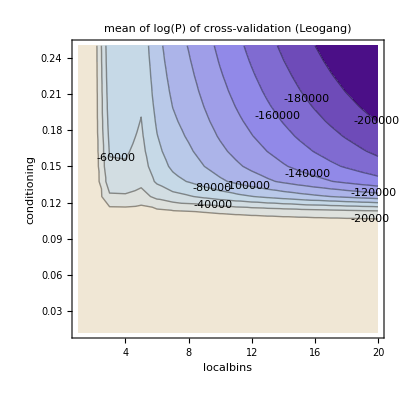

```mathematica
(* ListContourPlot[x10percentlist,PlotLabel->"TP rate at 10% FP (Leogang)",ContourLabels->All,Contours->15,FrameLabel->{"localbins","conditioning"}] *)
ListContourPlot[xCrossVallist,PlotLabel->"mean of log(P) of cross-validation (Leogang)",ContourLabels->All,Contours->10,FrameLabel->{"localbins","conditioning"}]
ListContourPlot[xCrossValVarlist,PlotLabel->"variance of log(P) of cross-validation",ContourLabels->All,Contours->10,FrameLabel->{"localbins","conditioning"}]
```

```mathematica
xFanolist=Table[{xCrossVallist⟦ii,1⟧,xCrossVallist⟦ii,2⟧,If[xCrossVallist⟦ii,3⟧≠0,xCrossValVarlist⟦ii,3⟧/(-xCrossVallist⟦ii,3⟧),0]},{ii,Length@xCrossVallist}];
ListContourPlot[xFanolist,PlotLabel->"Abs. Fano factor of log(P) of cross-validation",ContourLabels->All,Contours->10,FrameLabel->{"localbins","conditioning"}]
```

### try Fano factor of GTE itself

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/Paris/OptimalParametersTest/Leogang";
SetDirectory@basedir;
```

```mathematica
startii=0;
endii=399;
xstarttime=AbsoluteTime[];
xMeanlist=xVarlist=Table[{},{endii-startii+1}];
For[ii=startii,ii≤endii,ii++,
ShowStatus["ii = "<>ToString@ii<>", ETA "<>ETA[ii-startii,endii-startii+1,xstarttime]];
xadjA=Get["adjA_iteration"<>ToString@ii<>".mx"]⟦All,All,1⟧;
parsstring=Get["pars_iteration"<>ToString@ii<>".mx"];

xMeanlist⟦ii-startii+1⟧={bins/.parsstring,GlobalConditioningLevel/.parsstring,Mean@Flatten@xadjA};
xVarlist⟦ii-startii+1⟧={bins/.parsstring,GlobalConditioningLevel/.parsstring,Variance@Flatten@xadjA};
];
ShowStatus["done."];
Clear[xstarttime,ii,startii,endii,parsstring,xadjA,crossvallist,ROCpoints];
```

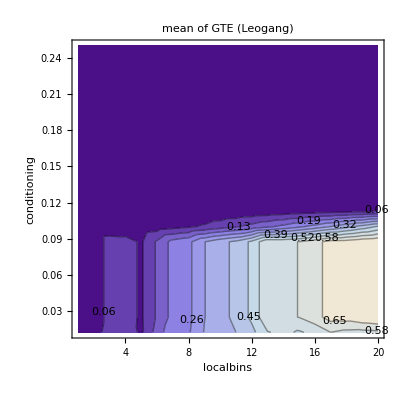

```mathematica
ListContourPlot[xMeanlist,PlotLabel->"mean of GTE (Leogang)",ContourLabels->All,Contours->10,FrameLabel->{"localbins","conditioning"}]
ListContourPlot[xVarlist,PlotLabel->"variance of GTE",ContourLabels->All,Contours->10,FrameLabel->{"localbins","conditioning"}]

xFanolist=Table[{xMeanlist⟦ii,1⟧,xMeanlist⟦ii,2⟧,If[xMeanlist⟦ii,3⟧≠0,xMeanlist⟦ii,3⟧/xVarlist⟦ii,3⟧,0]},{ii,Length@xMeanlist}];
ListContourPlot[xFanolist,PlotLabel->"Fano factor of GTE",ContourLabels->All,Contours->10,FrameLabel->{"localbins","conditioning"}]
```

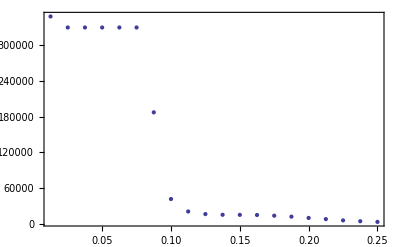

```mathematica
ListPlot@Cases[xFanolist,{20,_,_}]⟦All,2;;3⟧
```

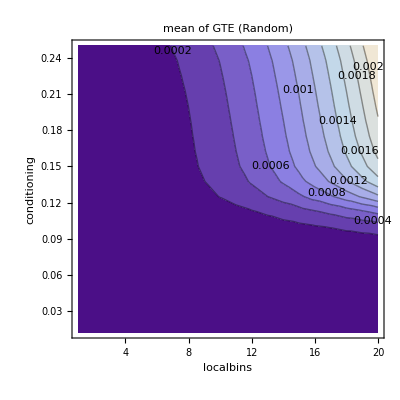

```mathematica
ListContourPlot[xMeanlist,PlotLabel->"mean of GTE (Random)",ContourLabels->All,Contours->10,FrameLabel->{"localbins","conditioning"}]
ListContourPlot[xVarlist,PlotLabel->"variance of GTE",ContourLabels->All,Contours->10,FrameLabel->{"localbins","conditioning"}]

xFanolist=Table[{xMeanlist⟦ii,1⟧,xMeanlist⟦ii,2⟧,If[xMeanlist⟦ii,3⟧≠0,xVarlist⟦ii,3⟧/xMeanlist⟦ii,3⟧,0]},{ii,Length@xMeanlist}];
ListContourPlot[xFanolist,PlotLabel->"Fano factor of GTE",ContourLabels->All,Contours->10,FrameLabel->{"localbins","conditioning"}]
```

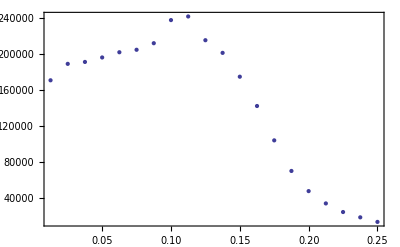

```mathematica
ListPlot@Cases[xFanolist,{5,_,_}]⟦All,2;;3⟧
```

### try Fano factor of GTE itself (this time, only off-diagonal elements)

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/Paris/OptimalParametersTest/Random";
SetDirectory@basedir;
```

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/Paris/2DbinningCondSatNoise/Random";
SetDirectory@basedir;
```

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/Live/2DConditioned";
SetDirectory@basedir;
```

```mathematica
startii=0;
endii=399;
xstarttime=AbsoluteTime[];
xMeanlist=xVarlist=Table[{},{endii-startii+1}];
For[ii=startii,ii≤endii,ii++,
ShowStatus["ii = "<>ToString@ii<>", ETA "<>ETA[ii-startii,endii-startii+1,xstarttime]];
xadjA=Get["adjA_iteration"<>ToString@ii<>".mx"]⟦All,All,1⟧;
parsstring=Get["pars_iteration"<>ToString@ii<>".mx"];

xdata=DeleteCases[Sort@Flatten[Table[If[ii≠jj,xadjA⟦ii,jj⟧,"nix"],{ii,Length@xadjA},{jj,Length@xadjA}],1],"nix"];

xMeanlist⟦ii-startii+1⟧={bins/.parsstring,GlobalConditioningLevel/.parsstring,Mean@Flatten@xdata};
xVarlist⟦ii-startii+1⟧={bins/.parsstring,GlobalConditioningLevel/.parsstring,Variance@Flatten@xdata};
];
ShowStatus["done."];
Clear[xstarttime,ii,startii,endii,parsstring,xadjA,xdata,crossvallist,ROCpoints];
```

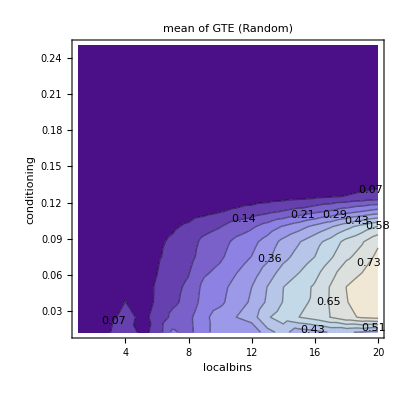

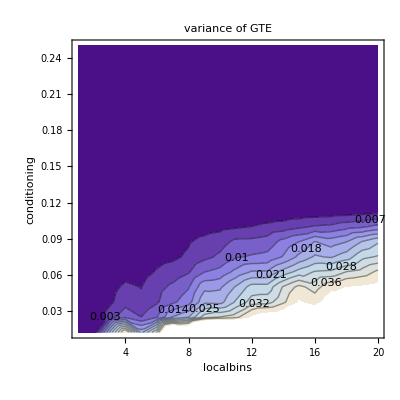

```mathematica
ListContourPlot[xMeanlist,PlotLabel->"mean of GTE (Random)",ContourLabels->All,Contours->10,FrameLabel->{"localbins","conditioning"}]
ListContourPlot[xVarlist,PlotLabel->"variance of GTE",ContourLabels->All,Contours->10,FrameLabel->{"localbins","conditioning"}]

xFanolist=Table[{xMeanlist⟦ii,1⟧,xMeanlist⟦ii,2⟧,If[xMeanlist⟦ii,3⟧≠0,xVarlist⟦ii,3⟧/xMeanlist⟦ii,3⟧,0]},{ii,Length@xMeanlist}];
ListContourPlot[xFanolist,PlotLabel->"Fano factor of GTE",ContourLabels->All,Contours->10,FrameLabel->{"localbins","conditioning"},PlotRange->All]
```

```mathematica
(* same, but logarithmic scale *)
ListContourPlot[{#⟦1⟧,#⟦2⟧,Log[#⟦3⟧]}&/@xMeanlist,PlotLabel->"log of mean of GTE (Random)",ContourLabels->All,Contours->10,FrameLabel->{"localbins","conditioning"}]
ListContourPlot[{#⟦1⟧,#⟦2⟧,Log[#⟦3⟧]}&/@xVarlist,PlotLabel->"log of variance of GTE",ContourLabels->All,Contours->10,FrameLabel->{"localbins","conditioning"}]

xFanolist=Table[{xMeanlist⟦ii,1⟧,xMeanlist⟦ii,2⟧,If[xMeanlist⟦ii,3⟧≠0,Log@(xMeanlist⟦ii,3⟧/xVarlist⟦ii,3⟧),0]},{ii,Length@xMeanlist}];
ListContourPlot[xFanolist,PlotLabel->"log of Fano factor of GTE",ContourLabels->All,Contours->10,FrameLabel->{"localbins","conditioning"},PlotRange->All]
```

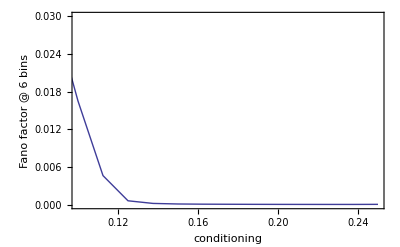

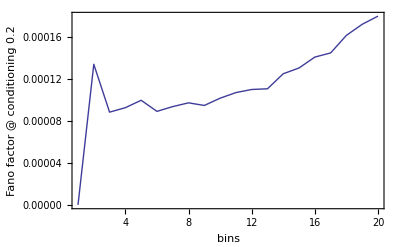

```mathematica
ListPlot[Cases[xFanolist,{6,_,_}]⟦All,2;;3⟧,Joined->True,FrameLabel->{"conditioning","Fano factor @ 6 bins"},PlotRange->{{0.1,0.25},{0,0.03}}]

ListPlot[Cases[xFanolist,{_,0.2,_}]⟦All,{1,3}⟧,Joined->True,FrameLabel->{"bins","Fano factor @ conditioning 0.2"}]
```

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/Paris/OptimalParametersTest/Leogang";
SetDirectory@basedir;
```

```mathematica
startii=0;
endii=399;
xstarttime=AbsoluteTime[];
xMeanlist=xVarlist=Table[{},{endii-startii+1}];
For[ii=startii,ii≤endii,ii++,
ShowStatus["ii = "<>ToString@ii<>", ETA "<>ETA[ii-startii,endii-startii+1,xstarttime]];
xin=Get["adjA_iteration"<>ToString@ii<>".mx"];
xadjA=xin⟦All,All,2⟧-xin⟦All,All,1⟧;
parsstring=Get["pars_iteration"<>ToString@ii<>".mx"];

xdata=DeleteCases[Sort@Flatten[Table[If[ii≠jj,xadjA⟦ii,jj⟧,"nix"],{ii,Length@xadjA},{jj,Length@xadjA}],1],"nix"];

xMeanlist⟦ii-startii+1⟧={bins/.parsstring,GlobalConditioningLevel/.parsstring,Mean@Flatten@xdata};
xVarlist⟦ii-startii+1⟧={bins/.parsstring,GlobalConditioningLevel/.parsstring,Log@Variance@Flatten@xdata};
];
ShowStatus["done."];
Clear[xstarttime,xin,ii,startii,endii,parsstring,xadjA,xdata,crossvallist,ROCpoints];
```

```mathematica
ListContourPlot[xMeanlist,PlotLabel->"mean of GTE Hxx (Leogang)",ContourLabels->All,Contours->10,FrameLabel->{"localbins","conditioning"}]
ListContourPlot[xVarlist,PlotLabel->"variance of GTE Hxx",ContourLabels->All,Contours->10,FrameLabel->{"localbins","conditioning"}]
```

```mathematica
ListContourPlot[xMeanlist,PlotLabel->"mean of GTE Hxxy (Leogang)",ContourLabels->All,Contours->10,FrameLabel->{"localbins","conditioning"}]
ListContourPlot[xVarlist,PlotLabel->"variance of GTE Hxxy",ContourLabels->All,Contours->10,FrameLabel->{"localbins","conditioning"}]
```

```mathematica
ListContourPlot[xVarlist,PlotLabel->"log variance of GTE Hxxy (Leogang)",ContourLabels->All,Contours->10,FrameLabel->{"localbins","conditioning"}]
```

## examine dependence on number of samples

### examine overall effect on quality of reconstruction

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/Paris/FractionOfSamplesTest";
SetDirectory@basedir;
```

```mathematica
startii=0;
endii=39;
xstarttime=AbsoluteTime[];
x10percentlist=AUClist=Table[{},{endii-startii+1}];
For[ii=startii,ii≤endii,ii++,
ShowStatus["ii = "<>ToString@ii<>", ETA "<>ETA[ii-startii,endii-startii+1,xstarttime]];
xadjA=Get["adjA_iteration"<>ToString@ii<>".mx"]⟦All,All,1⟧;
parsstring=Get["pars_iteration"<>ToString@ii<>".mx"];
xsamples=samples/.parsstring;
fn=Interpolation[ReduceForInterpolation@N@GenerateROCsmart@xadjA,InterpolationOrder->1];

x10percentlist⟦ii-startii+1⟧={First[AvailableSamples/.parsstring],fn[0.1]};
AUClist⟦ii-startii+1⟧={First[AvailableSamples/.parsstring]/.parsstring,NIntegrate[fn[x],{x,0,1}]};
];
ShowStatus["done."];
Clear[xstarttime,ii,startii,endii,parsstring,xadjA,fn,ROCpoints];
```

```mathematica
x10percentlist
AUClist
```

{{143648,0.426156},{72819,0.339067},{47830,0.275203},{36782,0.257222},{29536,0.231658},{24152,0.20596},{20980,0.196348},{18527,0.175563},{16466,0.168245},{14783,0.15758},{14068,0.158436},{12826,0.159167},{11600,0.152654},{10623,0.151027},{9980,0.141627},{9042,0.140222},{8631,0.14197},{8448,0.137456},{7991,0.137726},{7465,0.152207},{7167,0.146618},{6936,0.144458},{6632,0.139262},{6162,0.139729},{5988,0.146392},{5852,0.143611},{5485,0.135186},{5165,0.140469},{4906,0.131465},{4877,0.131612},{4830,0.128642},{4594,0.134798},{4340,0.134482},{4234,0.138172},{4127,0.141841},{3943,0.138976},{3906,0.142932},{3737,0.145274},{3647,0.146763},{3591,0.14595}}

{{143648,0.765237},{72819,0.693617},{47830,0.653632},{36782,0.637675},{29536,0.623772},{24152,0.615226},{20980,0.596204},{18527,0.581551},{16466,0.577269},{14783,0.574319},{14068,0.575185},{12826,0.56917},{11600,0.561365},{10623,0.561926},{9980,0.557322},{9042,0.547994},{8631,0.545511},{8448,0.543562},{7991,0.542053},{7465,0.545486},{7167,0.549146},{6936,0.544285},{6632,0.541515},{6162,0.539375},{5988,0.544318},{5852,0.54165},{5485,0.540723},{5165,0.53764},{4906,0.533842},{4877,0.534043},{4830,0.533952},{4594,0.531755},{4340,0.526416},{4234,0.527495},{4127,0.529809},{3943,0.526579},{3906,0.526652},{3737,0.529211},{3647,0.529164},{3591,0.528471}}

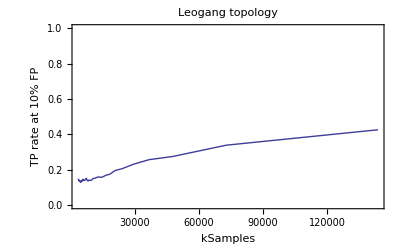

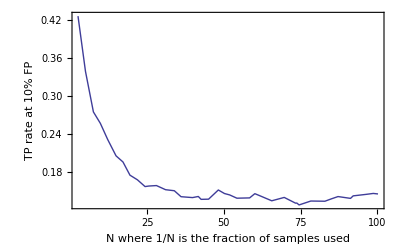

```mathematica
ListPlot[x10percentlist,PlotLabel->"Leogang topology",FrameLabel->{"kSamples","TP rate at 10% FP"},Joined->True,PlotRange->{All,{0,1}}]
ListPlot[{xsamples/(First@#),Second@#}&/@x10percentlist,FrameLabel->{"N where 1/N is the fraction of samples used","TP rate at 10% FP"},Joined->True,PlotRange->All]
```

### examine effect on distance dependence of connection probability

```mathematica
Sort[{1,2,3,5,6,3,4},Greater]
```

{6,5,4,3,3,2,1}

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/Paris/FractionOfSamplesTest";
SetDirectory@basedir;
```

```mathematica
startii=0;
endii=39;
xstarttime=AbsoluteTime[];
xdistlist=Table[{},{endii-startii+1}];
For[ii=startii,ii≤endii,ii++,
ShowStatus["ii = "<>ToString@ii<>", ETA "<>ETA[ii-startii,endii-startii+1,xstarttime]];
xadjA=Get["adjA_iteration"<>ToString@ii<>".mx"]⟦All,All,1⟧;
parsstring=Get["pars_iteration"<>ToString@ii<>".mx"];
xdistlist⟦ii-startii+1⟧={First[AvailableSamples/.parsstring]/.parsstring,MeanDistanceInNetwork[xadjA,0.1,pos]};
];
ShowStatus["done."];
Clear[xstarttime,ii,startii,endii,parsstring,xadjA,fn,ROCpoints];
```

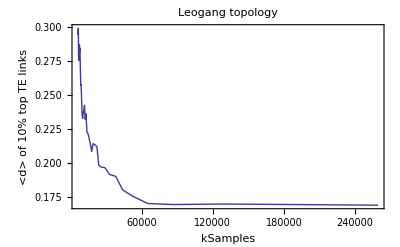

```mathematica
ListPlot[xdistlist,PlotLabel->"Leogang topology",FrameLabel->{"kSamples","<d> of 10% top TE links"},Joined->True,PlotRange->All]
```

### Debiasing : Do individual TE vales converge?

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/Paris/FractionOfSamplesTest";
SetDirectory@basedir;
```

```mathematica
startii=0;
endii=39;
xstarttime=AbsoluteTime[];
xManyadjAs=xManySamples={};
For[ii=startii,ii≤endii,ii++,
ShowStatus["ii = "<>ToString@ii<>", ETA "<>ETA[ii-startii,endii-startii+1,xstarttime]];
xadjA=Get["adjA_iteration"<>ToString@ii<>".mx"]⟦All,All,1⟧;
parsstring=Get["pars_iteration"<>ToString@ii<>".mx"];

AppendTo[xManyadjAs,xadjA];
AppendTo[xManySamples,First[AvailableSamples/.parsstring]];
];
xsamples=samples/.parsstring;
ShowStatus["done."];
Clear[xstarttime,ii,startii,endii,parsstring,xadjA];
```

```mathematica
xManyadjAs⟦All,1,2⟧
```

{0.000226087,0.000397503,0.000611975,0.000679951,0.000830255,0.00101186,0.000982961,0.00106965,0.00136935,0.00165523,0.00177292,0.00176023,0.0019794,0.00202369,0.00215159,0.00204372,0.00215579,0.00243564,0.0025625,0.00275847,0.00302821,0.00288568,0.00300559,0.00307575,0.00312785,0.00335475,0.00364444,0.00379889,0.00385512,0.00404238,0.00453079,0.00456102,0.00471891,0.00452358,0.00436669,0.00517233,0.00536353,0.00576056,0.00591105,0.00603858}

```mathematica
Table[{xManySamples⟦ii⟧,xManyadjAs⟦ii,1,2⟧},{ii,Length@xManyadjAs}]
```

{{259407,0.000226087},{130204,0.000397503},{86038,0.000611975},{65003,0.000679951},{52411,0.000830255},{43913,0.00101186},{38029,0.000982961},{32857,0.00106965},{28936,0.00136935},{25832,0.00165523},{23705,0.00177292},{22186,0.00176023},{20458,0.0019794},{18980,0.00202369},{17712,0.00215159},{16594,0.00204372},{15663,0.00215579},{14584,0.00243564},{13787,0.0025625},{12941,0.00275847},{12285,0.00302821},{11710,0.00288568},{10999,0.00300559},{10533,0.00307575},{10043,0.00312785},{9586,0.00335475},{9179,0.00364444},{8845,0.00379889},{8566,0.00385512},{8252,0.00404238},{7963,0.00453079},{7846,0.00456102},{7606,0.00471891},{7422,0.00452358},{7120,0.00436669},{6834,0.00517233},{6672,0.00536353},{6514,0.00576056},{6271,0.00591105},{6217,0.00603858}}

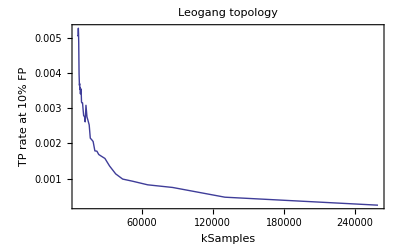

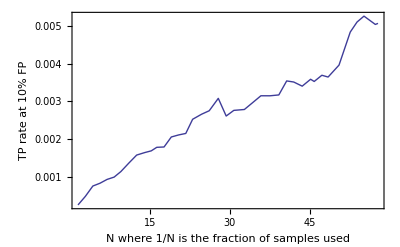

```mathematica
ListPlot[Table[{xManySamples⟦ii⟧,xManyadjAs⟦ii,1,3⟧},{ii,Length@xManyadjAs}],PlotLabel->"Leogang topology",FrameLabel->{"kSamples","TP rate at 10% FP"},Joined->True,PlotRange->All]
ListPlot[Table[{xsamples/xManySamples⟦ii⟧,xManyadjAs⟦ii,1,3⟧},{ii,Length@xManyadjAs}],FrameLabel->{"N where 1/N is the fraction of samples used","TP rate at 10% FP"},Joined->True,PlotRange->All]
```

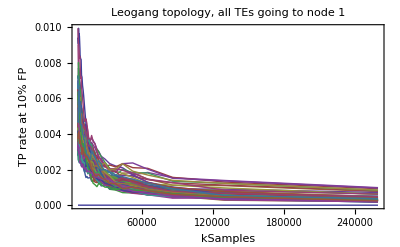

```mathematica
xindex=1;
ListPlot[Table[{xManySamples⟦ii⟧,xManyadjAs⟦ii,xindex,cto⟧},{cto,100},{ii,Length@xManyadjAs}],PlotLabel->"Leogang topology, all TEs going to node "<>ToString@xindex,FrameLabel->{"kSamples","TP rate at 10% FP"},Joined->True,PlotRange->All]
ListPlot[Table[{xsamples/xManySamples⟦ii⟧,xManyadjAs⟦ii,xindex,cto⟧},{cto,100},{ii,Length@xManyadjAs}],FrameLabel->{"N where 1/N is the fraction of samples used","TP rate at 10% FP"},Joined->True,PlotRange->All]
```

```mathematica
(* a) fit according to 01.11.10, p.1 while keeping offset fixed *)
xfn[x_]:=Qmax+α x;

xadjAdebiased=Table[0,{size/.pars},{size/.pars}];
For[cfrom=1,cfrom≤size/.pars,cfrom++,
For[cto=1,cto≤size/.pars,cto++,
If[cfrom≠cto,
xfitdata=Table[{xsamples/xManySamples⟦ii⟧,xManyadjAs⟦ii,cfrom,cto⟧},{ii,Length@xManyadjAs}];
Qmax:=xfitdata⟦1,2⟧;
xfit=FindFit[xfitdata,xfn[x],α,x];
xadjAdebiased⟦cfrom,cto⟧=(Qmax- α)/.xfit;
]]];
Clear[cfrom,cto,xfitdata,Qmax,xfit,x];
```

```mathematica
xadjAdebiasedFixed=xadjAdebiased;
```

```mathematica
(* b) fit according to 01.11.10, p.1 while fitting everything *)
xfn[x_]:=Qmax+α x;

xadjAdebiased=Table[0,{size/.pars},{size/.pars}];
For[cfrom=1,cfrom≤size/.pars,cfrom++,
For[cto=1,cto≤size/.pars,cto++,
If[cfrom≠cto,
xfitdata=Table[{xsamples/xManySamples⟦ii⟧,xManyadjAs⟦ii,cfrom,cto⟧},{ii,Length@xManyadjAs}];
xfit=FindFit[xfitdata,xfn[x],{{Qmax,xfitdata⟦1,2⟧},α},x];
xadjAdebiased⟦cfrom,cto⟧=(Qmax-α)/.xfit;
]]];
```

```mathematica
xManyadjAs⟦1,1;;3,1;;3⟧
xadjAdebiased⟦1;;3,1;;3⟧
```

{{0.,0.000226087,0.000246339},{0.000261541,0.,0.000251227},{0.00028417,0.000274668,0.}}

{{0,0.0000336512,0.000367507},{0.000267797,0,0.000311444},{-0.000388212,0.000766566,0}}

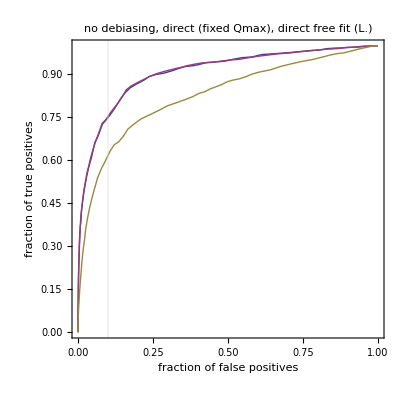

```mathematica
ListPlot[GenerateROCsmart/@{First@xManyadjAs,xadjAdebiasedFixed,xadjAdebiased},Joined->True,GridLines->{{0.1},{}},Axes->False,AspectRatio->1,FrameLabel->{"fraction of false positives","fraction of true positives"},PlotLabel->"no debiasing, direct (fixed Qmax), direct free fit (L.)",PlotRange->All]
```

## vector plots of different reconstructions

```mathematica
PlotVectorGraph[pos_,adjA_,title_]:=Module[{xplot,xrules,ii},
xplot={ListPlot[pos,PlotStyle->{Black,PointSize[Large]}]};
xrules=GetConnections@adjA;
For[ii=1,ii≤Length@xrules,ii++,AppendTo[xplot,Graphics[{Arrowheads[.025],Red,Arrow[{pos⟦xrules⟦ii,1⟧⟧,pos⟦xrules⟦ii,2⟧⟧}]}]]];
Show[xplot,DisplayFunction->$DisplayFunction,PlotRange->{{0,1},{0,1}},Frame->True,AspectRatio->1,PlotLabel->title]
];

AllPairs[x_Integer]:=AllPairs[x,x];
AllPairs[x_Integer,y_Integer]:=Module[{ii,jj},Flatten[Table[{ii,jj},{ii,x},{jj,y}],1]];
AboveDiagonalPairs[x_Integer]:=Module[{ii,jj},Flatten[Table[{ii,jj},{ii,x},{jj,ii+1,x}],1]];
```

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/Paris/2DbinningCondSatNoise/Leogang";
SetDirectory@basedir;
```

```mathematica
xindex=10+20*12;
importlist=<<("adjA_iteration"<>ToString@xindex<>".mx");
parsstring=<<("pars_iteration"<>ToString@xindex<>".mx")
importlist2=Table[importlist⟦All,All,ii⟧,{ii,Last@Dimensions@importlist}];
Clear[importlist,xindex];
```

{executable→teextendedsim,iteration→213,size→22,rawdatabins→255,bins→11,cutoff→-1,globalbins→2,samples→8000,StartSampleIndex→1,EndSampleIndex→7999,EqualSampleNumberQ→False,MaxSampleNumberPerBin→-1,AvailableSamples→{5960,2038},noise→-1,tauF→10,OverrideRescalingQ→False,HighPassFilterQ→True,InstantFeedbackTermQ→True,saturation→-1,IncludeGlobalSignalQ→True,GenerateGlobalFromFilteredDataQ→False,GlobalConditioningLevel→3900,TargetMarkovOrder→1,SourceMarkovOrder→1,inputfile→../../Imaging/NewCameraClusters/xresponse_255bins_cutoff.dat,outputfile→NewCameraClusters/k1_IF/adjA_iteration250.mx}

```mathematica
ListJoinDelimited[ToString@First@#<>"="<>If[StringQ[xtemp=Second@#],"\""<>xtemp<>"\"",ToString@Second@#]&/@parsstring,", "]
```

executable=teextendedsim, iteration=213, size=22, rawdatabins=255, bins=11, cutoff=-1, globalbins=2, samples=8000, StartSampleIndex=1, EndSampleIndex=7999, EqualSampleNumberQ=False, MaxSampleNumberPerBin=-1, AvailableSamples={5960, 2038}, noise=-1, tauF=10, OverrideRescalingQ=False, HighPassFilterQ=False, InstantFeedbackTermQ=True, saturation=-1, IncludeGlobalSignalQ=True, GenerateGlobalFromFilteredDataQ=False, GlobalConditioningLevel=3900, TargetMarkovOrder=1, SourceMarkovOrder=1, inputfile="../../Imaging/NewCameraClusters/xresponse_255bins_cutoff.dat", outputfile="NewCameraClusters/adjA_iteration250.mx"

```mathematica
temp=importlist2;
```

```mathematica
count=0;
xplot=PlotVectorGraph[pos,ThresholdedFractionA[#,0.1],"top 10% GTE links (hack: none)\ng.bin #"<>ToString[++count]<>", "<>ToString[(AvailableSamples/.parsstring)⟦count⟧]<>" samples, TP@10%FP="<>ToString@NumberForm[Interpolation[ReduceForInterpolation@N@GenerateROCsmart@#,InterpolationOrder->1][0.1],2]]&/@importlist2;
GraphicsRow[xplot,ImageSize->(globalbins/.parsstring)*350]
```

```mathematica
MeanDistanceInNetwork[First@importlist2,0.1,pos]
```

0.168786

```mathematica
xindex=8+8*20
importlist=<<("adjA_iteration"<>ToString@xindex<>".mx");
parsstring=<<("pars_iteration"<>ToString@xindex<>".mx")
importlist2=Table[importlist⟦All,All,ii⟧,{ii,Last@Dimensions@importlist}];
Clear[importlist,xindex];
```

168

{executable→teglobalsim,iteration→169,size→100,rawdatabins→255,bins→9,cutoff→-1,globalbins→2,samples→359951,p→1,noise→0.03,tauF→20,OverrideRescalingQ→0,HighPassFilterQ→1,InstantFeedbackTermQ→1,saturation→300,IncludeGlobalSignalQ→1,GenerateGlobalFromFilteredDataQ→0,GlobalConditioningLevel→0.1125,inputfile→../../Simulationen/NEST/calciumbursts2/Paris/LeogangTopology/noisefree_rawCalcium_uchar_20ms.dat,outputfile→Paris/2DbinningCondSatNoise/Leogang/adjA_iteration168.mx,outputparsfile→Paris/2DbinningCondSatNoise/Leogang/pars_iteration168.mx,outputcrossvalfile→Paris/2DbinningCondSatNoise/Leogang/crossval_iteration168.mx}

```mathematica
ThresholdedFractionA[First@importlist2,0.1]
```

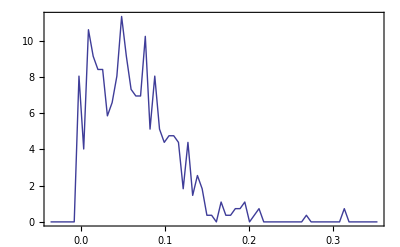

```mathematica
ListPlot[FineHistogramP[Flatten@First@importlist2,70],Joined->True]
```

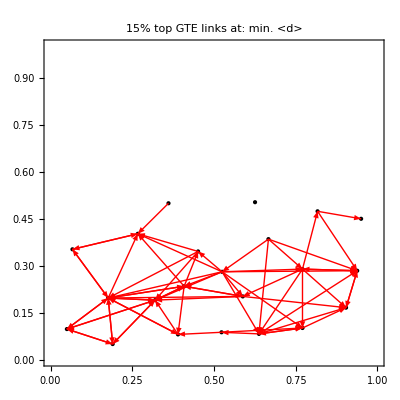

```mathematica
PlotVectorGraph[pos,ThresholdedFractionA[First@importlist2,0.15],"15% top GTE links at: min. <d>"]
```

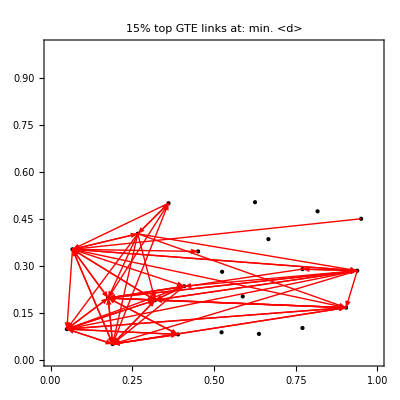

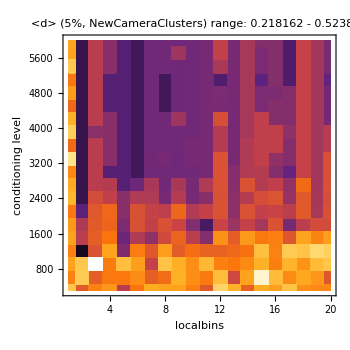
-Graphics-   -Graphics-

```mathematica
PlotVectorGraph[pos,ThresholdedFractionA[First@importlist2,0.15],"15% top GTE links at: min. <d>"]
```

```mathematica
MeanDistanceInNetwork[First@importlist2,0.1,pos]
```

0.189124

### DemianVectorPlots

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/Paris/DemianVectorPlots";
SetDirectory@basedir;
```

```mathematica
startii=0;
endii=10;
xstarttime=AbsoluteTime[];
xadjAlist=x10percentlist=AUClist=meandistList=parsList=Table[{},{endii-startii+1}];
For[ii=startii,ii≤endii,ii++,
ShowStatus["ii = "<>ToString@ii<>", ETA "<>ETA[ii-startii,endii-startii+1,xstarttime]];
xadjA=Get["adjA_iteration"<>ToString@ii<>".mx"]⟦All,All,2⟧;
parsstring=Get["pars_iteration"<>ToString@ii<>".mx"];
xsamples=samples/.parsstring;
fn=Interpolation[ReduceForInterpolation@N@GenerateROCsmart@xadjA,InterpolationOrder->1];

xadjAlist⟦ii-startii+1⟧=xadjA;
x10percentlist⟦ii-startii+1⟧=fn[0.1];
AUClist⟦ii-startii+1⟧={First[AvailableSamples/.parsstring]/.parsstring,NIntegrate[fn[x],{x,0,1}]};
meandistList⟦ii-startii+1⟧=MeanDistanceInNetwork[xadjA,0.1,pos];
parsList⟦ii-startii+1⟧=parsstring;
];
ShowStatus["done."];
Clear[xstarttime,ii,startii,endii,parsstring,xadjA,fn,ROCpoints];
```

```mathematica
plots={};
For[ii=1,ii≤Length@parsList,ii++,
AppendTo[plots,PlotVectorGraph[pos,ThresholdAdjAonFractionOfConnections[xadjAlist⟦ii⟧,0.1],"cond. above "<>ToString[GlobalConditioningLevel/.parsList⟦ii⟧]<>", TP@10%FP="<>ToString@NumberForm[x10percentlist⟦ii⟧,2]<>", <d_0.1> = "<>ToString@NumberForm[meandistList⟦ii⟧,2]]]
];
```

```mathematica
GraphicsRow[plots,ImageSize->Length[parsList]*350]
```

### DemianVectorPlots (separated, same number of data points)

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/Paris/DemianVectorPlots/Separated100kPoints/";
SetDirectory@basedir;
```

```mathematica
xstarttime=AbsoluteTime[];
parsstring=Get["pars_iteration0.mx"];
xadjAlist=x10percentlist=AUClist=meandistList=parsList=Table[{},{globalbins/.parsstring}];

xadjAlist=Table[Get["adjA_iteration0.mx"]⟦All,All,ii⟧,{ii,globalbins/.parsstring}];
xsamples=AvailableSamples/.parsstring;

For[ii=1,ii≤globalbins/.parsstring,ii++,
xadjA=xadjAlist⟦ii⟧;
fn=Interpolation[ReduceForInterpolation@N@GenerateROCsmart@xadjA,InterpolationOrder->1];

xadjAlist⟦ii⟧=xadjA;
x10percentlist⟦ii⟧=fn[0.1];
AUClist⟦ii⟧={First[AvailableSamples/.parsstring]/.parsstring,NIntegrate[fn[x],{x,0,1}]};
meandistList⟦ii⟧=MeanDistanceInNetwork[xadjA,0.1,pos];
parsList⟦ii⟧=parsstring;
];
ShowStatus["done."];
Clear[xstarttime,ii,startii,endii,xadjA,fn,ROCpoints];
```

Warning: ThresholdedFractionA: MiniShuffle Hack (nr=475)!

```mathematica
maxglobal=0.525;
plots={};
For[ii=1,ii≤Length@parsList,ii++,
AppendTo[plots,PlotVectorGraph[pos,ThresholdAdjAonFractionOfConnections[xadjAlist⟦ii⟧,0.1],"TE sep. between "<>ToString[((ii-1)*maxglobal)/(globalbins/.parsstring)]<>" and "<>ToString[(ii*maxglobal)/(globalbins/.parsstring)]<>" ("<>If[(AvailableSamples/.parsstring)⟦ii⟧<Max[AvailableSamples/.parsstring],"warning! ",""]<>ToString[(AvailableSamples/.parsstring)⟦ii⟧]<>" samples),\n TP@10%FP="<>ToString@NumberForm[x10percentlist⟦ii⟧,2]<>", <d_0.1> = "<>ToString@NumberForm[meandistList⟦ii⟧,2]]]
];
```

```mathematica
GraphicsRow[plots,ImageSize->Length[parsList]*350]
```

### Vector plots ("VectorPlotReplicateTest")

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/VectorPlotReplicateTest/";
SetDirectory@basedir;
```

```mathematica
parsstring=Get["pars_iteration5.mx"];importlist2=Table[Get["adjA_iteration5.mx"]⟦All,All,ii⟧,{ii,globalbins/.parsstring}];
```

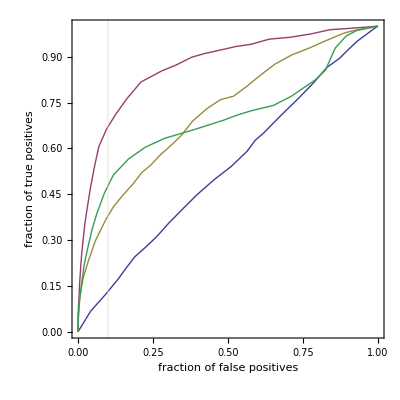

```mathematica
ListPlot[GenerateROCsmart/@importlist2,Joined->True,GridLines->{{0.1},{}},Axes->False,AspectRatio->1,FrameLabel->{"fraction of false positives","fraction of true positives"},PlotLabel->"",PlotRange->All]
```

## Cross - correlation analysis, communities

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/VectorPlotReplicateTest/";
SetDirectory@basedir;
```

```mathematica
parsstring=Get["pars_iteration5.mx"];importlist2=Table[Get["adjA_iteration5.mx"]⟦All,All,ii⟧,{ii,globalbins/.parsstring}];
```

```mathematica
xadjAlist:=importlist2;
```

```mathematica
plots=(PlotVectorGraph[pos,ThresholdedFractionA[#,0.1],""]&/@xadjAlist);
```

```mathematica
ROCs=ListPlot[GenerateROCsmart@#,Joined->True,GridLines->{{0.1},{}},Axes->False,AspectRatio->1,FrameLabel->{"fraction of false positives","fraction of true positives"},PlotLabel->"",PlotRange->All]&/@importlist2;
```

```mathematica
GraphicsGrid[{plots,ROCs},ImageSize->Length[plots]*350]
```

```mathematica
adjAsThresholded=(ThresholdedFractionA[#,0.1]&/@xadjAlist);
indegreesNow=((Total/@#&)/@adjAsThresholded);
```

```mathematica
Print["<k_in> = ",μ=N[0.1*(size-1)size/size/.pars]];
```

<k_in> = 9.9

```mathematica
testfn[x_]:=If[x>μ,True,False];
nodesSelected=(Flatten@Position[#,_?testfn]&/@indegreesNow)
```

{{1,4,5,6,7,9,10,14,16,19,20,21,23,29,31,36,41,44,50,51,52,55,57,59,62,64,67,69,72,73,74,75,81,83,86,88,89,90,91,93,96,97,98},{3,4,7,11,12,14,17,18,21,25,26,27,29,32,33,36,40,42,43,48,51,54,56,57,58,61,62,63,66,67,68,70,71,73,76,77,79,80,82,83,84,85,90,91,92,95,99,100},{11,12,14,18,25,32,36,43,45,48,56,58,62,63,66,67,68,70,71,73,76,77,80,83,84,90,92,99,100},{1,2,3,4,6,7,9,10,13,15,17,21,24,26,27,28,29,30,31,33,34,35,37,38,39,40,42,44,45,46,47,49,50,51,52,54,57,58,60,64,65,66,72,75,77,79,82,85,86,87,91,92,93,95,99}}

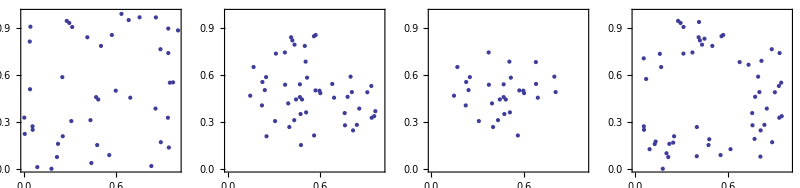

```mathematica
posplots=(If[Length@#>0,ListPlot[pos⟦#⟧,PlotRange->{{0,1},{0,1}},AspectRatio->1,PlotStyle->PointSize[Large]]]&/@nodesSelected);
GraphicsRow[posplots,ImageSize->Length[plots]*200]
```

#### 1st try of seperating communities

```mathematica
intersectOnes=Intersection[nodesSelected⟦2⟧,nodesSelected⟦4⟧];
Length@intersectOnes
```

15

```mathematica
nodesSelectedExclusive=(Complement[#,intersectOnes]&/@nodesSelected)
```

{{4,5,7,9,14,16,19,20,23,31,55,59,62,64,67,69,73,74,81,88,89,91,96,98},{11,12,14,18,25,32,36,43,48,56,61,62,63,67,70,71,73,76,77,80,83,84,90,100},{11,12,14,18,25,32,36,43,45,48,56,62,63,67,68,70,71,73,76,77,80,83,84,90,99,100},{1,2,4,6,7,10,15,17,24,30,31,34,35,37,38,39,40,44,45,46,47,49,50,52,60,65,75,86,91,95,99}}

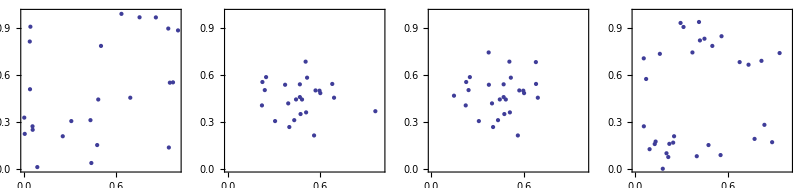

```mathematica
posplots=(If[Length@#>0,ListPlot[pos⟦#⟧,PlotRange->{{0,1},{0,1}},AspectRatio->1,PlotStyle->PointSize[Large]]]&/@nodesSelectedExclusive);
GraphicsRow[posplots,ImageSize->Length[plots]*200,PlotLabel->"without intersection of #2 and #4"]
```

```mathematica
Correlation[xresponse⟦nodesSelectedExclusive⟦2,1⟧⟧,xresponse⟦nodesSelectedExclusive⟦4,2⟧⟧]
```

0.0361057

```mathematica
xpairs=Flatten[Table[{ii,jj},{ii,Length@nodesSelectedExclusive},{jj,ii+1,Length@nodesSelectedExclusive}],1]
```

{{1,2},{1,3},{1,4},{2,3},{2,4},{3,4}}

```mathematica
xcorwithin2=Correlation[xresponse⟦nodesSelectedExclusive⟦2,#⟦1⟧⟧⟧,xresponse⟦nodesSelectedExclusive⟦2,#⟦2⟧⟧⟧]&/@AboveDiagonalPairs[Length@nodesSelectedExclusive⟦2⟧];
```

```mathematica
xcorwithin4=Correlation[xresponse⟦nodesSelectedExclusive⟦4,#⟦1⟧⟧⟧,xresponse⟦nodesSelectedExclusive⟦4,#⟦2⟧⟧⟧]&/@AboveDiagonalPairs[Length@nodesSelectedExclusive⟦4⟧];
```

```mathematica
xcrosscor24=Correlation[xresponse⟦nodesSelectedExclusive⟦2,#⟦1⟧⟧⟧,xresponse⟦nodesSelectedExclusive⟦4,#⟦2⟧⟧⟧]&/@AllPairs[Length@nodesSelectedExclusive⟦2⟧,Length@nodesSelectedExclusive⟦4⟧];
```

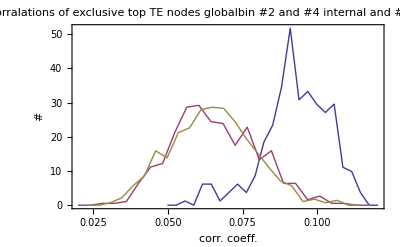

```mathematica
ListPlot[{FineHistogramP[xcorwithin2,xbins=25],FineHistogramP[xcorwithin4,xbins],FineHistogramP[xcrosscor24,xbins]},Joined->True,PlotRange->All,PlotLabel->"corralations of exclusive top TE nodes\nglobalbin #2 and #4 internal and #2-#4-Xcorr.",FrameLabel->{"corr. coeff.","#"}]
```

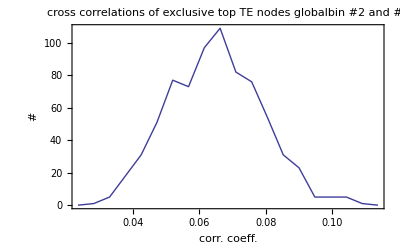

```mathematica
ListPlot[FineHistogram[xcrosscor24,20],Joined->True,PlotRange->All,PlotLabel->"cross correlations of exclusive top TE nodes\nglobalbin #2 and #4",FrameLabel->{"corr. coeff.","#"}]
```

```mathematica
AllPairs[Length@nodesSelectedExclusive⟦2⟧,Length@nodesSelectedExclusive⟦4⟧]
```

#### 2nd try, separating the fringe communities into upper and lower nodes

```mathematica
nodeCommunities={nodesSelectedExclusive⟦2⟧,{},{}};
If[pos⟦#,2⟧>1/2,AppendTo[nodeCommunities⟦2⟧,#],AppendTo[nodeCommunities⟦3⟧,#]]&/@nodesSelectedExclusive⟦4⟧;
```

```mathematica
nodeCommunities
```

{{11,12,14,18,25,32,36,43,48,56,61,62,63,67,70,71,73,76,77,80,83,84,90,100},{2,4,24,30,34,35,39,40,44,45,47,52,86,95,99},{1,6,7,10,15,17,31,37,38,46,49,50,60,65,75,91}}

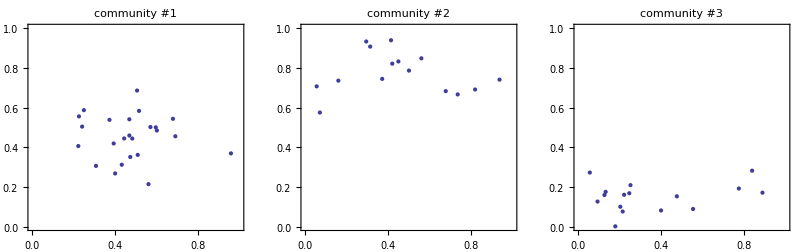

```mathematica
communityplots=(count=1;(If[Length@#>0,ListPlot[pos⟦#⟧,PlotRange->{{0,1},{0,1}},AspectRatio->1,PlotStyle->PointSize[Large],PlotLabel->"community #"<>ToString[count++]]]&/@nodeCommunities));
GraphicsRow[communityplots,ImageSize->Length[plots]*200]
```

```mathematica
Length/@nodeCommunities
```

{24,15,16}

```mathematica
xcorwithincomm1=Correlation[xresponse⟦nodeCommunities⟦1,#⟦1⟧⟧⟧,xresponse⟦nodeCommunities⟦1,#⟦2⟧⟧⟧]&/@AboveDiagonalPairs[Length@nodeCommunities⟦1⟧];
```

```mathematica
xcorwithincomm2=Correlation[xresponse⟦nodeCommunities⟦2,#⟦1⟧⟧⟧,xresponse⟦nodeCommunities⟦2,#⟦2⟧⟧⟧]&/@AboveDiagonalPairs[Length@nodeCommunities⟦2⟧];
```

```mathematica
xcorwithincomm3=Correlation[xresponse⟦nodeCommunities⟦3,#⟦1⟧⟧⟧,xresponse⟦nodeCommunities⟦3,#⟦2⟧⟧⟧]&/@AboveDiagonalPairs[Length@nodeCommunities⟦3⟧];
```

```mathematica
xcrosscor12=Correlation[xresponse⟦nodeCommunities⟦1,#⟦1⟧⟧⟧,xresponse⟦nodeCommunities⟦2,#⟦2⟧⟧⟧]&/@AllPairs[Length@nodeCommunities⟦1⟧,Length@nodeCommunities⟦2⟧];
```

```mathematica
xcrosscor13=Correlation[xresponse⟦nodeCommunities⟦1,#⟦1⟧⟧⟧,xresponse⟦nodeCommunities⟦3,#⟦2⟧⟧⟧]&/@AllPairs[Length@nodeCommunities⟦1⟧,Length@nodeCommunities⟦3⟧];
```

```mathematica
xcrosscor23=Correlation[xresponse⟦nodeCommunities⟦2,#⟦1⟧⟧⟧,xresponse⟦nodeCommunities⟦3,#⟦2⟧⟧⟧]&/@AllPairs[Length@nodeCommunities⟦2⟧,Length@nodeCommunities⟦3⟧];
```

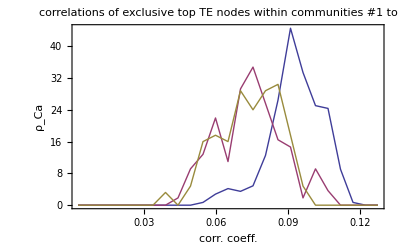

avg.: {0.0928831,0.0740271,0.0737988}

```mathematica
ListPlot[{FineHistogramP[xcorwithincomm1,xbins=25,xrange],FineHistogramP[xcorwithincomm2,xbins,xrange],FineHistogramP[xcorwithincomm3,xbins,xrange]},Joined->True,PlotRange->All,PlotLabel->"correlations of exclusive top TE nodes\nwithin communities #1 to #3",FrameLabel->{"corr. coeff.","ρ_Ca"}]
Print["avg.: ",Mean/@{xcorwithincomm1,xcorwithincomm2,xcorwithincomm3}]
```

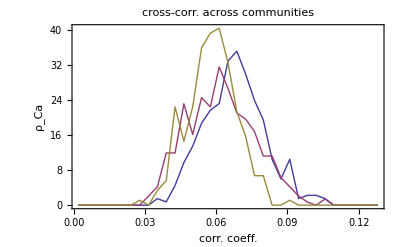

avg.: {0.0679103,0.0618595,0.0580706}

```mathematica
ListPlot[{FineHistogramP[xcrosscor12,xbins=35,xrange={0,0.13}],FineHistogramP[xcrosscor13,xbins,xrange],FineHistogramP[xcrosscor23,xbins,xrange]},Joined->True,PlotRange->All,PlotLabel->"cross-corr. across communities",FrameLabel->{"corr. coeff.","ρ_Ca"}]
Print["avg.: ",Mean/@{xcrosscor12,xcrosscor13,xcrosscor23}]
```

#### 3rd try, do Demian' s bidding

```mathematica
nodeCommunities={{},{},{}};
If[pos⟦#,1⟧>0.6,AppendTo[nodeCommunities⟦3⟧,#],If[pos⟦#,2⟧>1/2,AppendTo[nodeCommunities⟦1⟧,#],AppendTo[nodeCommunities⟦2⟧,#]]]&/@nodesSelected⟦4⟧;
```

```mathematica
nodeCommunities
```

{{2,4,29,30,34,35,40,42,44,47,52,54,57,58,72,95,99},{1,7,10,15,28,31,37,38,46,49,50,64,65,75,77,91},{3,6,9,13,17,21,24,26,27,33,39,45,51,60,66,79,82,85,86,87,92,93}}

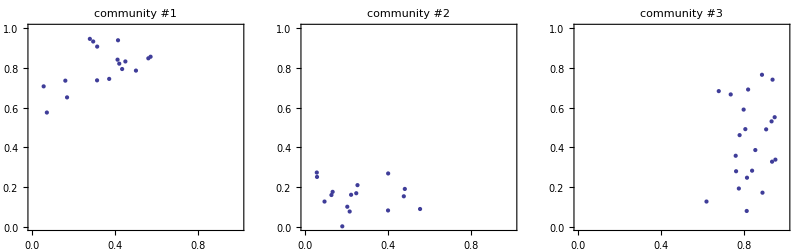

```mathematica
communityplots=(count=1;(If[Length@#>0,ListPlot[pos⟦#⟧,PlotRange->{{0,1},{0,1}},AspectRatio->1,PlotStyle->PointSize[Large],PlotLabel->"community #"<>ToString[count++]]]&/@nodeCommunities));
GraphicsRow[communityplots,ImageSize->Length[plots]*200]
```

```mathematica
(* cut out top bin signal *)
xdata:=xtest;
xmean=Mean@xdata;
xmeanD=DiscretizeNew[xmean,4];
xresponse=SwitchToDiff/@xdata;
```

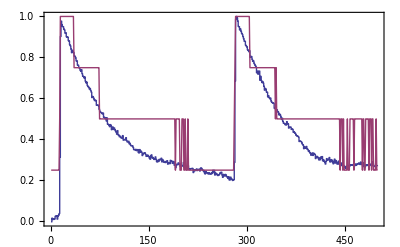

```mathematica
xrange=1;;500;
ListPlot[{xmean⟦xrange⟧/Max[xmean⟦xrange⟧],xmeanD⟦xrange⟧/Max[xmeanD⟦xrange⟧]},Joined->True,InterpolationOrder->{0,1}]
```

```mathematica
BinIndex=1;
posTopBin=Flatten@Position[xmeanD,BinIndex];
(* removing un-closed ranges *)
count=1;
While[First@posTopBin==count++,posTopBin=Drop[posTopBin,1]];
count=Length@xmeanD;
While[Last@posTopBin==count--,posTopBin=Drop[posTopBin,-1]];
posTopBin=Drop[posTopBin,-10];

onsetsTopBin=offsetsTopBin={};
If[(xmeanD⟦#-1⟧≠BinIndex)&&(xmeanD⟦#+1⟧==BinIndex),AppendTo[onsetsTopBin,#]]&/@posTopBin;
If[(xmeanD⟦#-1⟧==BinIndex)&&(xmeanD⟦#+1⟧≠BinIndex),AppendTo[offsetsTopBin,#]]&/@posTopBin;
Length[onsetsTopBin]==Length[offsetsTopBin]
Clear[count,posTopBin];
```

True

```mathematica
onsetsTopBin
offsetsTopBin
```

```mathematica
(* exclude very short ranges *)
rangesTopBin=(First@#;;Second@#)&/@Cases[Transpose[{onsetsTopBin,offsetsTopBin}],{x_,y_}/;y-x>10];
Length@rangesTopBin
```

222

```mathematica
lengthrangesTopBin=(-First@#+Second@#+1)&/@rangesTopBin
Min@%
```

{70,45,150,31,37,156,63,16,108,161,574,33,25,103,36,113,113,94,47,13,135,30,43,362,19,12,45,84,14,46,56,29,32,12,93,101,37,158,23,259,37,219,51,76,226,25,146,20,68,25,31,267,45,26,50,21,84,82,439,24,16,47,223,20,205,139,35,37,24,170,169,397,115,50,156,227,85,109,55,215,117,91,21,538,115,45,22,63,366,12,152,255,169,407,169,344,44,140,45,146,33,102,223,55,23,15,30,17,136,21,119,113,26,286,39,32,119,48,220,89,14,43,37,27,182,224,27,20,29,13,192,65,51,100,12,298,46,99,26,13,25,48,97,15,29,19,19,332,33,26,266,19,22,19,108,253,22,43,23,130,54,21,44,25,102,168,95,264,47,38,14,171,12,539,48,192,178,186,490,130,23,81,312,162,30,42,13,52,19,15,37,14,26,266,92,68,29,104,17,188,208,34,456,324,197,467,144,36,16,138,290,36,157,15,15,29,60,12,242,33,24,189}

12

```mathematica
ShiftRange[range_Span,lag_Integer]:=Module[{startii=First@range,endii=Second@range,rstart,rend},
rstart=startii;
rend=endii;

If[lag>0,rstart+=lag];
If[lag<0,rend+=lag];
(*If[rstart<1,rstart=1];
If[rend<1,rend=1];*)
If[rstart≥rend,rstart=endii;rend=endii-1];
(*Print[rstart;;rend];*)

Return[rstart;;rend];
];
```

```mathematica
ShiftRange[xrange=(2;;10),0]
ShiftRange[xrange,1]
ShiftRange[xrange,100]
ShiftRange[xrange,-1]
ShiftRange[xrange,-100]
```

2;;10

3;;10

10;;9

2;;9

10;;9

```mathematica
lagStart=-1;
lagEnd=+2;
lagIndexZero=1-lagStart
```

2

```mathematica
XCorWithinCommunityLagged=Table[Mean[Correlation[xresponse⟦nodeCommunities⟦commii,#⟦1⟧⟧,ShiftRange[rangesTopBin⟦rangeii⟧,lag]⟧,xresponse⟦nodeCommunities⟦commii,#⟦2⟧⟧,ShiftRange[rangesTopBin⟦rangeii⟧,-lag]⟧]&/@AboveDiagonalPairs[Length@nodeCommunities⟦commii⟧]],{commii,3},{lag,lagStart,lagEnd,1},{rangeii,Length@rangesTopBin}];
```

```mathematica
XCorMeanList=Table[{lag,Mean@Flatten@XCorWithinCommunityLagged⟦All,lag-lagStart+1⟧},{lag,lagStart,lagEnd,1}]
XCorMeanListPlus=Table[{{lag,Mean@(xtemp=Flatten[XCorWithinCommunityLagged⟦All,lag-lagStart+1⟧])},Sqrt@Variance@xtemp},{lag,lagStart,lagEnd,1}]
```

{{-2,0.000436905},{-1,0.000153966},{0,-0.000234415},{1,0.00089377},{2,0.0000449075}}

{{{-2,0.000436905},0.0144854},{{-1,0.000153966},0.0147279},{{0,-0.000234415},0.0150465},{{1,0.00089377},0.0143093},{{2,0.0000449075},0.0160029}}

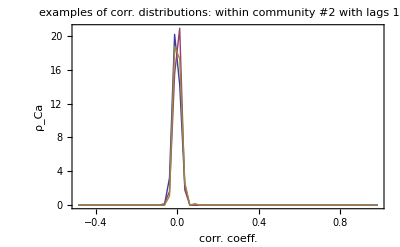

```mathematica
ListPlot[FineHistogramP[Flatten@#,xbins=60,{-0.5,1}]&/@XCorWithinCommunityLagged⟦1,lagIndexZero;;All⟧,Joined->True,PlotRange->All,InterpolationOrder->1,Filling->False,FrameLabel->{"corr. coeff.","ρ_Ca"},PlotLabel->"examples of corr. distributions:\nwithin community #2 with lags 1...4"]
```

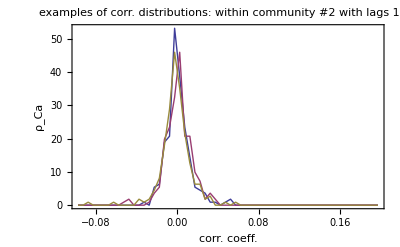

```mathematica
ListPlot[FineHistogramP[Flatten@#,xbins=60,{-0.1,0.2}]&/@XCorWithinCommunityLagged⟦3,lagIndexZero;;All⟧,Joined->True,PlotRange->All,InterpolationOrder->1,Filling->False,FrameLabel->{"corr. coeff.","ρ_Ca"},PlotLabel->"examples of corr. distributions:\nwithin community #2 with lags 1...4"]
```

```mathematica
XCorAcrossCommunitiesLagged=Table[Mean[Correlation[xresponse⟦nodeCommunities⟦commii1,#⟦1⟧⟧,ShiftRange[rangesTopBin⟦rangeii⟧,lag]⟧,xresponse⟦nodeCommunities⟦commii2,#⟦2⟧⟧,ShiftRange[rangesTopBin⟦rangeii⟧,-lag]⟧]&/@AllPairs[Length@nodeCommunities⟦commii1⟧,Length@nodeCommunities⟦commii2⟧]],{commii1,3},{commii2,commii1+1,3},{lag,lagStart,lagEnd,1},{rangeii,Length@rangesTopBin}];
```

```mathematica
XCorAcrossMeanList=Table[{lag,Mean@Flatten@XCorAcrossCommunitiesLagged⟦All,All,lag-lagStart+1⟧},{lag,lagStart,lagEnd,1}]
XCorAcrossMeanListPlus=Table[{{lag,Mean[xtemp=Flatten@XCorAcrossCommunitiesLagged⟦All,All,lag-lagStart+1⟧]},Sqrt@Variance@xtemp},{lag,lagStart,lagEnd,1}]
```

{{-1,0.000655687},{0,-0.00039473},{1,0.000376671},{2,-0.000390341}}

{{{-1,0.000655687},0.00970349},{{0,-0.00039473},0.0097849},{{1,0.000376671},0.0101666},{{2,-0.000390341},0.0102982}}

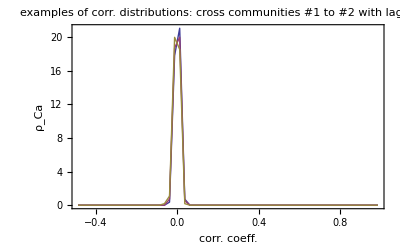

```mathematica
ListPlot[FineHistogramP[Flatten@#,xbins=60,{-0.5,1}]&/@XCorAcrossCommunitiesLagged⟦1,1,lagIndexZero;;All⟧,Joined->True,PlotRange->All,InterpolationOrder->1,Filling->False,FrameLabel->{"corr. coeff.","ρ_Ca"},PlotLabel->"examples of corr. distributions:\ncross communities #1 to #2 with lags 1...4"]
```

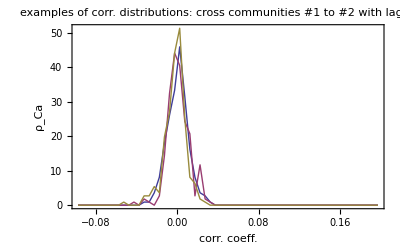

```mathematica
ListPlot[FineHistogramP[Flatten@#,xbins=60,{-0.1,0.2}]&/@XCorAcrossCommunitiesLagged⟦1,1,lagIndexZero;;All⟧,Joined->True,PlotRange->All,InterpolationOrder->1,Filling->False,FrameLabel->{"corr. coeff.","ρ_Ca"},PlotLabel->"examples of corr. distributions:\ncross communities #1 to #2 with lags 1...4"]
```

```mathematica
f[x_,y_,opts:OptionsPattern[]]:=bla;
Options[f,opts]={offset->0};
```

```mathematica
f[x_,y_,opts___Rule]:=x+y+(offset /.{opts}/.Options[f]);
Options[f]={offset->0};
```

```mathematica
ListPlotWithStd[wholelist_List,opts:OptionsPattern[]]:=ListPlotWithStd[wholelist⟦All,1⟧,wholelist⟦All,2⟧,opts];

ListPlotWithStd[list_List,error_Number,opts:OptionsPattern[]]:=ListPlotWithStd[list,Table[error,{Length@list}],opts];

ListPlotWithStd[list_List,errors_List,opts:OptionsPattern[]]:=Module[{xplot1,xplot2,errorsexpanded},
xplot1=ListPlot[list,Joined->True,PlotRange->All,DisplayFunction->Identity,opts];
errorsexpanded=Transpose[{Table[0,{Length@errors}],errors}];
xplot2=ListPlot[{list+errorsexpanded,list-errorsexpanded},Joined->True,PlotRange->All,Filling->{1->{2}},PlotStyle->None,opts];
Show[xplot1,xplot2,PlotRange->All,opts]
];
```

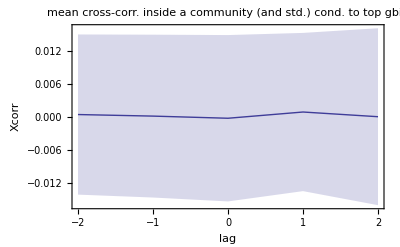

```mathematica
ListPlotWithStd[XCorMeanListPlus,PlotLabel->"mean cross-corr. inside a community (and std.)\ncond. to top gbin",FrameLabel->{"lag","Xcorr"}]
```

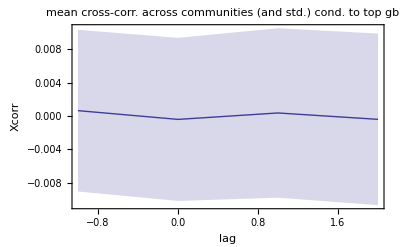

```mathematica
ListPlotWithStd[XCorAcrossMeanListPlus,PlotLabel->"mean cross-corr. across communities (and std.)\ncond. to top gbin",FrameLabel->{"lag","Xcorr"}]
```

#### test significance

```mathematica
Needs["HypothesisTesting`"]
```

```mathematica
xtestvaluesWithin = Flatten[XCorAcrossCommunitiesLagged[[All,All,lagIndexZero]]]; 
μWithin = Mean[xtestvaluesWithin]
VarWithin = Variance[xtestvaluesWithin]
xtestvaluesAcross = Flatten[XCorWithinCommunityLagged[[All,lagIndexZero]]]; 
μAcross = Mean[xtestvaluesAcross]
VarAcross = Variance[xtestvaluesAcross]
```

0.359255

0.0399209

0.416712

0.0452262

```mathematica
MeanTest[xtestvaluesWithin,μAcross,KnownVariance->4*VarAcross]
MeanTest[xtestvaluesAcross,μWithin,KnownVariance->4*VarWithin]
```

OneSidedPValue→0.00286823

OneSidedPValue→0.00159036

```mathematica
KolmogorovSmirnovTestForManySamples[listX_List,listY_List]:=Module[{ii,ordering,seq,n=Length[listX],m=Length[listY],Pnm},
If[Length[Union[Flatten[{listX,listY}]]]≠n+m,
Print["KolmogorovSmirnovTestForManySamples: error: samples not all distinct."];Abort[]];

ordering=Ordering[Flatten[{listX,listY}]];
seq=(If[#>Length@listX,1,0]&/@ordering);
Pnm=Count[{
];
```

```mathematica
Export["MWhypoData.mat",{xtestvaluesWithin,xtestvaluesAcross}]
```

MWhypoData.mat

```mathematica
xtemp={xtestvaluesWithin,xtestvaluesAcross};
Dimensions@xtemp
```

{2,855}

```mathematica
Length/@xtemp
```

{855,855}

```mathematica
listX={1.1,2.1,3.1,4.1};
listY={1/5,2,1/2,2.3};
```

```mathematica
Flatten@{listX,listY}
Ordering@Flatten@{listX,listY}
If[#>Length@listX,1,0]&/@%
Partition[%,2,1]
Count[%,{1,0}]
```

{1.1,2.1,3.1,4.1,1/5,2,1/2,2.3}

{5,7,1,6,2,8,3,4}

{1,1,0,1,0,1,0,0}

{{1,1},{1,0},{0,1},{1,0},{0,1},{1,0},{0,0}}

3

#### test lagged correlation code

```mathematica
testtrace1=Table[Mod[t,3],{i,3},{t,27}]
testtrace2=Table[Mod[t+RandomInteger[{0,1}],3],{i,3},{t,27}]
```

{{1,2,0,1,2,0,1,2,0,1,2,0,1,2,0,1,2,0,1,2,0,1,2,0,1,2,0},{1,2,0,1,2,0,1,2,0,1,2,0,1,2,0,1,2,0,1,2,0,1,2,0,1,2,0},{1,2,0,1,2,0,1,2,0,1,2,0,1,2,0,1,2,0,1,2,0,1,2,0,1,2,0}}

{{2,2,1,2,2,1,1,2,1,2,0,0,2,2,1,1,2,1,2,0,0,2,0,0,2,2,1},{2,0,1,1,2,1,2,0,0,1,0,1,2,2,1,1,0,0,1,2,0,2,2,1,1,0,0},{1,2,1,1,2,1,2,0,1,2,0,0,1,2,0,1,0,0,1,2,1,1,2,0,2,0,0}}

```mathematica
XCorAcrossCommunitiesLaggedTest=Table[{lag,Correlation[N@testtrace1⟦rangeii,ShiftRange[1;;27,lag]⟧,testtrace2⟦rangeii,ShiftRange[1;;27,-lag]⟧]},{lag,-10,10,1},{rangeii,3}]
```

{{{-10,-0.593217},{-10,-0.451613},{-10,-0.524072}},{{-9,0.233314},{-9,0.261778},{-9,0.408248}},{{-8,0.388692},{-8,0.168148},{-8,0.163128}},{{-7,-0.593733},{-7,-0.45888},{-7,-0.5201}},{{-6,0.280056},{-6,0.215758},{-6,0.280056}},{{-5,0.279869},{-5,0.287588},{-5,0.279869}},{{-4,-0.540266},{-4,-0.465116},{-4,-0.51433}},{{-3,0.312908},{-3,0.258558},{-3,0.31414}},{{-2,0.25},{-2,0.193908},{-2,0.188445}},{{-1,-0.549857},{-1,-0.422284},{-1,-0.469388}},{{0,0.341144},{0,0.171686},{0,0.343371}},{{1,0.227893},{1,0.294628},{1,0.117851}},{{2,-0.58238},{2,-0.436949},{2,-0.436949}},{{3,0.312908},{3,0.193919},{3,0.400892}},{{4,0.263205},{4,0.258574},{4,0.}},{{5,-0.555822},{5,-0.483779},{5,-0.373244}},{{6,0.381246},{6,0.148522},{6,0.308607}},{{7,0.164566},{7,0.308607},{7,0.0771517}},{{8,-0.527736},{8,-0.424397},{8,-0.424397}},{{9,0.501675},{9,0.},{9,0.261778}},{{10,0.},{10,0.456435},{10,0.182574}}}

{{-10,-0.522967},{-9,0.301114},{-8,0.239989},{-7,-0.524238},{-6,0.258624},{-5,0.282442},{-4,-0.50657},{-3,0.295202},{-2,0.210784},{-1,-0.48051},{0,0.2854},{1,0.213457},{2,-0.485426},{3,0.302573},{4,0.173926},{5,-0.470948},{6,0.279458},{7,0.183441},{8,-0.458843},{9,0.254484},{10,0.213003}}

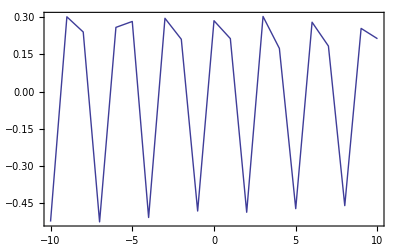

```mathematica
Mean/@XCorAcrossCommunitiesLaggedTest
ListPlot[%,PlotRange->All,Joined->True]
```

#### nearest neighbor correlation plots

```mathematica
GBinRange={};
For[BinIndex=1,BinIndex≤4,BinIndex++,
posTopBin=Flatten@Position[xmeanD,BinIndex];
(* removing un-closed ranges *)
count=1;
While[First@posTopBin==count++,posTopBin=Drop[posTopBin,1]];
count=Length@xmeanD;
While[Last@posTopBin==count--,posTopBin=Drop[posTopBin,-1]];

onsetsTopBin=offsetsTopBin={};
If[(xmeanD⟦#-1⟧≠BinIndex)&&(xmeanD⟦#+1⟧==BinIndex),AppendTo[onsetsTopBin,#]]&/@posTopBin;
If[(xmeanD⟦#-1⟧==BinIndex)&&(xmeanD⟦#+1⟧≠BinIndex),AppendTo[offsetsTopBin,#]]&/@posTopBin;
If[Length[onsetsTopBin]≠Length[offsetsTopBin],Abort[]];

(* exclude very short ranges *)
rangesTopBin=(First@#;;Second@#)&/@Cases[Transpose[{onsetsTopBin,offsetsTopBin}],{x_,y_}/;y-x>10];
AppendTo[GBinRange,rangesTopBin];
];

Clear[count,posTopBin,onsetsTopBin,offsetsTopBin];
```

```mathematica
Length/@GBinRange
```

{222,160,132,132}

```mathematica
(* for lag zero we can just glue together the time series *)
xdataGlued={};
For[gbin=1,gbin≤4,gbin++,
xtemp={};
For[ii=1,ii≤size/.pars,ii++,
AppendTo[xtemp,Flatten[xdata⟦ii,#⟧&/@GBinRange⟦gbin⟧]];
];
AppendTo[xdataGlued,xtemp];
];
Clear[gbin,ii];
```

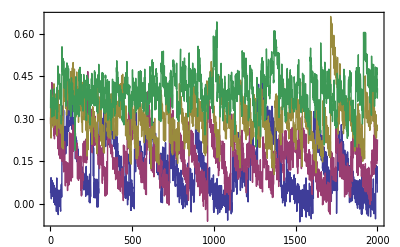

```mathematica
ListPlot[xdataGlued⟦All,1,1;;2000⟧,Joined->True]
```

```mathematica
(* for lag zero we can just glue together the HP time series *)
xdataGluedHP={};
For[gbin=1,gbin≤4,gbin++,
xtemp={};
For[ii=1,ii≤size/.pars,ii++,
AppendTo[xtemp,Flatten[xresponse⟦ii,#⟧&/@GBinRange⟦gbin⟧]];
];
AppendTo[xdataGluedHP,xtemp];
];
Clear[gbin,ii];
```

```mathematica
ListPlot[xdataGluedHP⟦All,1,1;;2000⟧,Joined->True,PlotRange->All]
```

```mathematica
xNeighborList[ii_]:=Module[{cons,consInHere,consOutHere},
cons=GetConnections@adjA;
consInHere=Cases[cons,{_,ii}];
consOutHere=Cases[cons,{ii,_}];
Return[Union@Flatten@{consInHere⟦All,1⟧,consOutHere⟦All,2⟧}];
];
```

```mathematica
xSampleLength=Min[Length/@xdataGlued⟦All,1⟧];
xSampleRange=1;;xSampleLength
```

1;;3182

```mathematica
(* calculate mean cross-corr. of neurons to neighbors *)
xXCorByNode=Table[0,{4},{size/.pars}];
For[gbin=1,gbin≤4,gbin++,
For[ii=1,ii≤size/.pars,ii++,
xXCorByNode⟦gbin,ii⟧=Mean[Correlation[xdataGlued⟦gbin,ii,xSampleRange⟧,xdataGlued⟦gbin,#,xSampleRange⟧]&/@xNeighborList[ii]];
];
];
Clear[gbin,ii];
```

```mathematica
xSampleLengthHP=Min[Length/@xdataGluedHP⟦All,1⟧];
xSampleRangeHP=1;;xSampleLength
```

1;;3182

```mathematica
(* calculate mean cross-corr. of neurons to neighbors - HP, equal sample size version *)
xXCorByNodeHP=Table[0,{4},{size/.pars}];
For[gbin=1,gbin≤4,gbin++,
For[ii=1,ii≤size/.pars,ii++,
xXCorByNodeHP⟦gbin,ii⟧=Mean[Correlation[xdataGluedHP⟦gbin,ii,xSampleRangeHP⟧,xdataGluedHP⟦gbin,#,xSampleRangeHP⟧]&/@xNeighborList[ii]];
];
];
Clear[gbin,ii];
```

```mathematica
xXCorByNode⟦4⟧
```

```mathematica
xXCorByNodeHP⟦4⟧
```

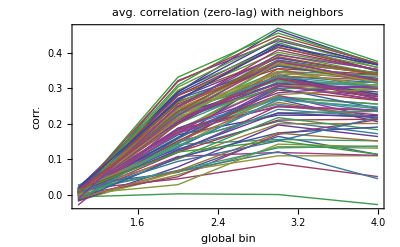

```mathematica
ListPlot[Transpose@xXCorByNode,Joined->True,PlotLabel->"avg. correlation (zero-lag) with neighbors",FrameLabel->{"global bin","corr."}]
```

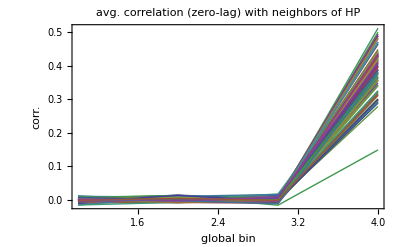

```mathematica
ListPlot[Transpose@xXCorByNodeHP,Joined->True,PlotLabel->"avg. correlation (zero-lag) with neighbors of HP",FrameLabel->{"global bin","corr."}]
```

```mathematica
xCfnNorm[xNorm_]:=RGBColor[xNorm,0.2,0.2];
```

```mathematica
xCfnRaw[x_]:=RGBColor[2x,0.2,0.2];
```

```mathematica
legendNorm=Row[{"   ",QuickLegend[0,1,xCfnNorm]},FrameMargins->20];
```

```mathematica
legendRaw=Row[{"   ",QuickLegend[0,1/2,xCfnRaw,False]},FrameMargins->20];
```

```mathematica
communityplots=(count=1;(If[Length@#>0,ListPlot[Table[{pos⟦jj⟧},{jj,size/.pars}],PlotRange->{{0,1},{0,1}},AspectRatio->1,PlotStyle->Table[Directive[PointSize[0.1],xCfnRaw[#⟦ii⟧]],{ii,size/.pars}],PlotLabel->"globalbin #"<>ToString[count++]]]&/@xXCorByNode));
GraphicsRow[Append[communityplots,legendRaw],Alignment->{Left,Center},ImageSize->280*Length[communityplots]+40,PlotLabel->"zero-lag correlation coeff. between nearest neighbors in the different (eparated, equal sample size) global bins"]
```

-Graphics-

```mathematica
communityplots=(count=1;(If[Length@#>0,ListPlot[Table[{pos⟦jj⟧},{jj,size/.pars}],PlotRange->{{0,1},{0,1}},AspectRatio->1,PlotStyle->Table[Directive[PointSize[0.1],RGBColor[#⟦ii⟧/Max[#],0.2,0.2]],{ii,size/.pars}],PlotLabel->"globalbin #"<>ToString[count++]<>" (color norm.)"]]&/@xXCorByNode));
GraphicsRow[Append[communityplots,legendNorm],Alignment->{Left,Center},ImageSize->280*Length[communityplots]+40,PlotLabel->"zero-lag correlation coeff. between nearest neighbors in the different (eparated, equal sample size) global bins"]
```

-Graphics-

```mathematica
communityplots=(count=1;(If[Length@#>0,ListPlot[Table[{pos⟦jj⟧},{jj,size/.pars}],PlotRange->{{0,1},{0,1}},AspectRatio->1,PlotStyle->Table[Directive[PointSize[0.1],xCfnRaw[#⟦ii⟧]],{ii,size/.pars}],PlotLabel->"globalbin #"<>ToString[count++]<>" (HP)"]]&/@xXCorByNodeHP));
GraphicsRow[Append[communityplots,legendRaw],Alignment->{Left,Center},ImageSize->280*Length[communityplots]+40]
```

-Graphics-

```mathematica
communityplots=(count=1;(If[Length@#>0,ListPlot[Table[{pos⟦jj⟧},{jj,size/.pars}],PlotRange->{{0,1},{0,1}},AspectRatio->1,PlotStyle->Table[Directive[PointSize[0.1],RGBColor[#⟦ii⟧/Max[#],0.2,0.2]],{ii,size/.pars}],PlotLabel->"globalbin #"<>ToString[count++]<>" (color norm., HP)"]]&/@xXCorByNodeHP));
GraphicsRow[Append[communityplots,legendNorm],Alignment->{Left,Center},ImageSize->280*Length[communityplots]+40]
```

-Graphics-

## Test cond. cross - correlation as measure for the reconstruction

### generate conditioned signal

```mathematica
(* cut out top bin signal *)
xdata:=xtest;
xmean=Mean@xdata;
xmeanD=DiscretizeNew[xmean,2];
xresponse=SwitchToDiff/@xdata;
```

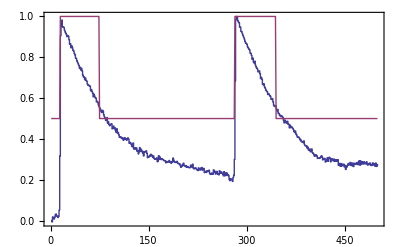

```mathematica
xrange=1;;500;
ListPlot[{xmean⟦xrange⟧/Max[xmean⟦xrange⟧],xmeanD⟦xrange⟧/Max[xmeanD⟦xrange⟧]},Joined->True,InterpolationOrder->{0,1}]
```

```mathematica
BinIndex=1;
posTopBin=Flatten@Position[xmeanD,BinIndex];
(* removing un-closed ranges *)
count=1;
While[First@posTopBin==count++,posTopBin=Drop[posTopBin,1]];
count=Length@xmeanD;
While[Last@posTopBin==count--,posTopBin=Drop[posTopBin,-1]];

onsetsTopBin=offsetsTopBin={};
If[(xmeanD⟦#-1⟧≠BinIndex)&&(xmeanD⟦#+1⟧==BinIndex),AppendTo[onsetsTopBin,#]]&/@posTopBin;
If[(xmeanD⟦#-1⟧==BinIndex)&&(xmeanD⟦#+1⟧≠BinIndex),AppendTo[offsetsTopBin,#]]&/@posTopBin;
Length[onsetsTopBin]==Length[offsetsTopBin]
Clear[count,posTopBin];
```

True

```mathematica
Length[onsetsTopBin]
Length[offsetsTopBin]
```

269

269

```mathematica
onsetsTopBin⟦xrange=1;;10⟧
offsetsTopBin⟦xrange⟧
```

{75,345,844,962,1111,1292,1797,2065,2288,2781}

{281,711,888,1042,1220,1731,1997,2223,2717,3642}

```mathematica
onsetsTopBin
offsetsTopBin
```

```mathematica
(* exclude very short ranges *)
rangesTopBin=(First@#;;Second@#)&/@Cases[Transpose[{onsetsTopBin,offsetsTopBin}],{x_,y_}/;y-x>10];
Length@rangesTopBin
```

238

```mathematica
lengthrangesTopBin=(-First@#+Second@#+1)&/@rangesTopBin
Min@%
```

{207,367,45,81,110,440,201,159,430,862,138,427,294,418,182,602,226,115,246,145,220,67,176,178,432,20,312,32,445,173,866,51,273,78,313,120,610,43,263,256,593,420,492,62,1161,382,619,77,656,862,299,793,553,27,83,594,686,64,367,294,265,554,629,33,22,119,1201,350,674,114,197,594,142,209,103,240,154,67,429,80,70,49,108,268,135,64,176,477,135,118,62,556,669,20,117,102,138,406,163,516,884,665,16,171,341,494,1229,302,142,130,101,359,756,221,236,625,1123,108,107,1009,43,628,484,1011,365,436,40,181,502,96,1042,97,46,241,123,52,50,338,315,322,103,272,396,237,104,15,200,33,453,67,72,1276,281,428,259,238,48,200,126,81,134,45,198,438,277,954,21,336,377,1014,292,149,231,364,26,186,194,165,230,234,779,397,135,188,145,44,100,702,111,278,101,282,101,125,26,446,342,149,44,220,68,770,62,295,19,615,161,1011,333,78,438,716,305,279,187,78,142,254,157,669,27,55,94,69,70,727,32,632,134,381,1230,40,364,221,274,208,266,100}

15

```mathematica
ShiftRange[range_Span,lag_Integer]:=Module[{startii=First@range,endii=Second@range,rstart,rend},
rstart=startii;
rend=endii;

If[lag>0,rstart+=lag];
If[lag<0,rend+=lag];
(*If[rstart<1,rstart=1];
If[rend<1,rend=1];*)
If[rstart≥rend,rstart=endii;rend=endii-1];
(*Print[rstart;;rend];*)

Return[rstart;;rend];
];
```

```mathematica
xdataGlued=Table[Flatten[xdata⟦ii,#⟧&/@rangesTopBin],{ii,Length@xdata}];
xdataGluedHP=Table[Flatten[xresponse⟦ii,#⟧&/@rangesTopBin],{ii,Length@xdata}];
```

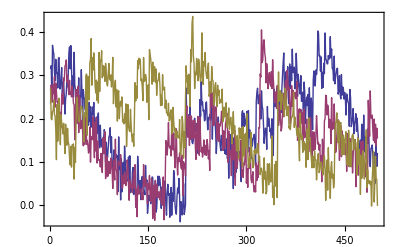

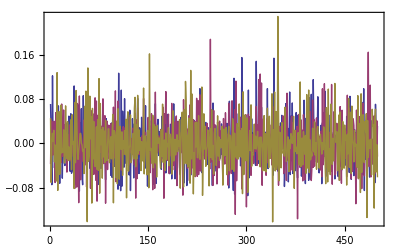

```mathematica
xrange=1;;500;
ListPlot[xdataGlued⟦1;;3,xrange⟧,Joined->True]
ListPlot[xdataGluedHP⟦1;;3,xrange⟧,Joined->True]
```

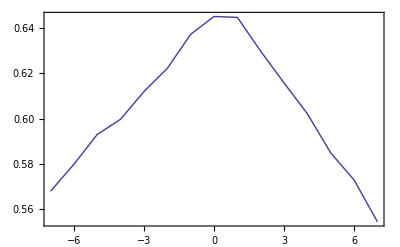

```mathematica
xindexfrom=1;
xindexto=6;
xrange=1;;2000;
ListPlot[Table[{lag,Correlation[xdata⟦xindexfrom,ShiftRange[xrange,lag]⟧,xdata⟦xindexto,ShiftRange[xrange,-lag]⟧]},{lag,-7,7}],Joined->True,PlotRange->All]
Clear[xindexfrom,xindexto,xrange];
```

```mathematica
ShiftRange[xrange,-1]
```

1;;1999

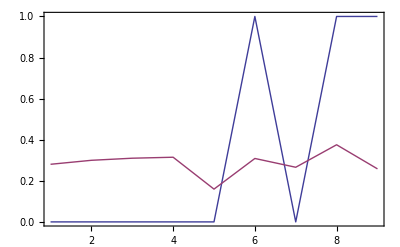

```mathematica
xindexfrom=1;
xrange=1;;2000;
ListPlot[{adjA⟦1,2;;10⟧,Table[8*Max@Table[Correlation[xresponse⟦xindexfrom,ShiftRange[xrange,lag]⟧,xdata⟦xindexto,ShiftRange[xrange,-lag]⟧],{lag,0,2}],{xindexto,2,10}]},Joined->True,PlotRange->All]
```

### calculate raw XCorr reconstruction (zero lag)

```mathematica
lag=0;
xrange=1;;2000;
Print["system size: ",xsize=Length@xdata];
adjAtest=Table[0,{xsize},{xsize}];
For[cfrom=1,cfrom≤xsize,cfrom++,
ShowStatus["running: ii = ",cfrom];
For[cto=1,cto≤xsize,cto++,
If[cfrom≠cto,
adjAtest⟦cfrom,cto⟧=Correlation[xdata⟦cfrom,ShiftRange[xrange,lag]⟧,xdata⟦cto,ShiftRange[xrange,-lag]⟧];
]]];
ShowStatus["done"];
Clear[cfrom,cto,xsize];
```

system size: 100

```mathematica
xadjAcorrRaw=adjAtest;
```

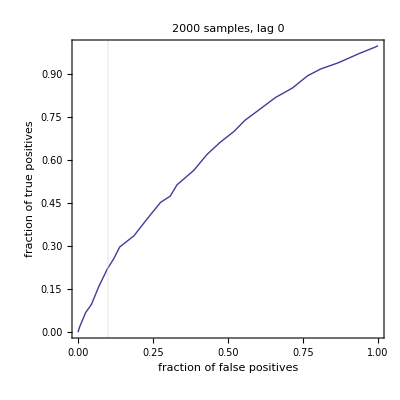

```mathematica
ListPlot[GenerateROCsmart@adjAtest,Joined->True,GridLines->{{0.1},{}},Axes->False,AspectRatio->1,FrameLabel->{"fraction of false positives","fraction of true positives"},PlotLabel->"2000 samples, lag 0",PlotRange->All]
```

### calculate XCorr reconstruction, unconditioned, maxlag, noHP

```mathematica
xrange=1;;1000;
Print["system size: ",xsize=Length@xdata];
adjAtest=Table[0,{xsize},{xsize}];
For[cfrom=1,cfrom≤xsize,cfrom++,
ShowStatus["running: ii = ",cfrom];
For[cto=1,cto≤xsize,cto++,
If[cfrom≠cto,
adjAtest⟦cfrom,cto⟧=Max@Table[Correlation[xdata⟦cfrom,ShiftRange[xrange,lag]⟧,xdata⟦cto,ShiftRange[xrange,-lag]⟧],{lag,0,2}];
]]];
ShowStatus["done"];
Clear[cfrom,cto,xsize];
```

system size: 100

```mathematica
xadjAcorrUncondnoHP=adjAtest;
```

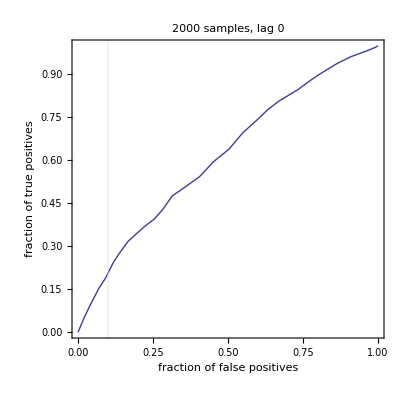

```mathematica
ListPlot[GenerateROCsmart@adjAtest,Joined->True,GridLines->{{0.1},{}},Axes->False,AspectRatio->1,FrameLabel->{"fraction of false positives","fraction of true positives"},PlotLabel->"2000 samples, lag 0",PlotRange->All]
```

### calculate XCorr reconstruction, unconditioned, maxlag, HP

```mathematica
xrange=1;;1000;
Print["system size: ",xsize=Length@xdata];
adjAtest=Table[0,{xsize},{xsize}];
For[cfrom=1,cfrom≤xsize,cfrom++,
ShowStatus["running: ii = ",cfrom];
For[cto=1,cto≤xsize,cto++,
If[cfrom≠cto,
adjAtest⟦cfrom,cto⟧=Max@Table[Correlation[xresponse⟦cfrom,ShiftRange[xrange,lag]⟧,xresponse⟦cto,ShiftRange[xrange,-lag]⟧],{lag,0,2}];
]]];
ShowStatus["done"];
Clear[cfrom,cto,xsize];
```

system size: 100

```mathematica
xadjAcorrUncondHP=adjAtest;
```

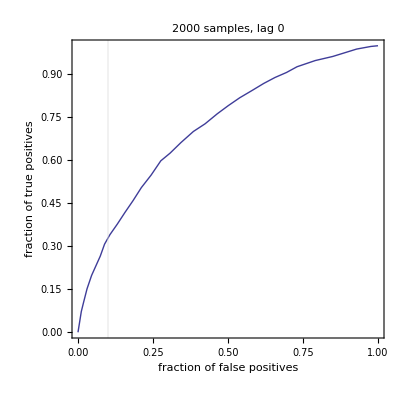

```mathematica
ListPlot[GenerateROCsmart@adjAtest,Joined->True,GridLines->{{0.1},{}},Axes->False,AspectRatio->1,FrameLabel->{"fraction of false positives","fraction of true positives"},PlotLabel->"2000 samples, lag 0",PlotRange->All]
```

### calculate XCorr reconstruction, conditioned, maxlag, HP

```mathematica
xrange=1;;1000;
Print["system size: ",xsize=Length@xdata];
adjAtest=Table[0,{xsize},{xsize}];
For[cfrom=1,cfrom≤xsize,cfrom++,
ShowStatus["running: ii = ",cfrom];
For[cto=1,cto≤xsize,cto++,
If[cfrom≠cto,
adjAtest⟦cfrom,cto⟧=Max@Table[Correlation[xdataGluedHP⟦cfrom,ShiftRange[xrange,lag]⟧,xdataGluedHP⟦cto,ShiftRange[xrange,-lag]⟧],{lag,0,2}];
]]];
ShowStatus["done"];
Clear[cfrom,cto,xsize];
```

system size: 100

```mathematica
xadjAcorrCondHP=adjAtest;
```

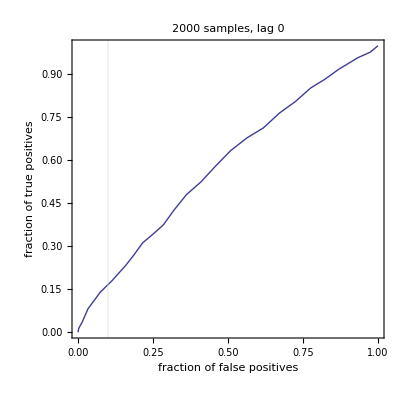

```mathematica
ListPlot[GenerateROCsmart@adjAtest,Joined->True,GridLines->{{0.1},{}},Axes->False,AspectRatio->1,FrameLabel->{"fraction of false positives","fraction of true positives"},PlotLabel->"2000 samples, lag 0",PlotRange->All]
```

### calculate XCorr reconstruction, conditioned, maxlag, noHP

```mathematica
xrange=1;;1000;
Print["system size: ",xsize=Length@xdata];
adjAtest=Table[0,{xsize},{xsize}];
For[cfrom=1,cfrom≤xsize,cfrom++,
ShowStatus["running: ii = ",cfrom];
For[cto=1,cto≤xsize,cto++,
If[cfrom≠cto,
adjAtest⟦cfrom,cto⟧=Max@Table[Correlation[xdataGlued⟦cfrom,ShiftRange[xrange,lag]⟧,xdataGlued⟦cto,ShiftRange[xrange,-lag]⟧],{lag,0,2}];
]]];
ShowStatus["done"];
Clear[cfrom,cto,xsize];
```

system size: 100

```mathematica
xadjAcorrCondNoHP=adjAtest;
```

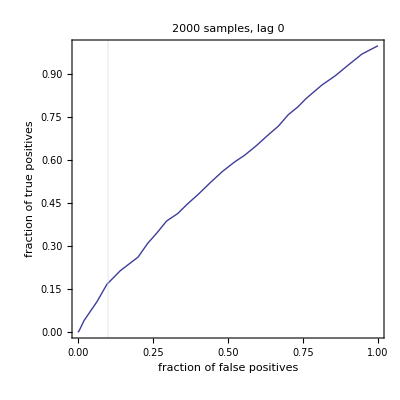

```mathematica
ListPlot[GenerateROCsmart@adjAtest,Joined->True,GridLines->{{0.1},{}},Axes->False,AspectRatio->1,FrameLabel->{"fraction of false positives","fraction of true positives"},PlotLabel->"2000 samples, lag 0",PlotRange->All]
```

### summary

```mathematica
ListPlot[GenerateROCsmart/@{xadjAcorrUncondHP,xadjAcorrCondHP},Joined->True,GridLines->{{0.1},{}},Axes->False,AspectRatio->1,FrameLabel->{"fraction of false positives","fraction of true positives"},PlotLabel->"xadjAcorrUncondHP,xadjAcorrCondHP\n1000 samples\n",PlotRange->All]
```

-Graphics-

## examine conditioning on firing rate (HowManyAreActive) signal

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/Paris/RateConditioningTest/Random";
SetDirectory@basedir;
```

```mathematica
startii=0;
endii=19;
xstarttime=AbsoluteTime[];
x10percentlist=AUClist=Table[{},{endii-startii+1}];
For[ii=startii,ii≤endii,ii++,
ShowStatus["ii = "<>ToString@ii<>", ETA "<>ETA[ii-startii,endii-startii+1,xstarttime]];
xadjA=Get["adjA_iteration"<>ToString@ii<>".mx"]⟦All,All,1⟧;
parsstring=Get["pars_iteration"<>ToString@ii<>".mx"];
fn=Interpolation[ReduceForInterpolation@N@GenerateROCsmart@xadjA,InterpolationOrder->1];

x10percentlist⟦ii-startii+1⟧={bins/.parsstring,fn[0.1]};
];
AvailableSamples/.parsstring
ShowStatus["done."];
Clear[xstarttime,ii,startii,endii,parsstring,xadjA,fn,ROCpoints,xsamples];
```

{355902,4047}

```mathematica
x10percentlist
```

{{1,0.1},{2,0.790299},{3,0.631307},{4,0.752259},{5,0.739368},{6,0.739343},{7,0.72941},{8,0.721905},{9,0.682656},{10,0.646044},{11,0.626629},{12,0.603136},{13,0.557997},{14,0.523324},{15,0.480375},{16,0.442821},{17,0.389351},{18,0.356271},{19,0.31779},{20,0.271785}}

```mathematica
ListPlot[x10percentlist,PlotLabel->"Leogang topology, cond. to 24% of nodes active",FrameLabel->{"localbins","TP rate at 10% FP"},Joined->True,PlotRange->{All,{0,1}}]
```

-Graphics-

## evaluate a number of topologies

```mathematica
ListPlotWithStd[wholelist_List,opts:OptionsPattern[]]:=ListPlotWithStd[wholelist⟦All,1⟧,wholelist⟦All,2⟧,opts];

ListPlotWithStd[list_List,error_Number,opts:OptionsPattern[]]:=ListPlotWithStd[list,Table[error,{Length@list}],opts];

ListPlotWithStd[list_List,errors_List,opts:OptionsPattern[]]:=Module[{xplot1,xplot2,errorsexpanded},
xplot1=ListPlot[list,Joined->True,PlotRange->All,DisplayFunction->Identity,opts];
errorsexpanded=Transpose[{Table[0,{Length@errors}],errors}];
xplot2=ListPlot[{list+errorsexpanded,list-errorsexpanded},Joined->True,PlotRange->All,Filling->{1->{2}},PlotStyle->None,opts];
Show[xplot1,xplot2,PlotRange->All,opts]
];
```

```mathematica
basedir = "~/Desktop/Doktorarbeit/Causality/transferentropy-sim/Paris/2DbinningCondSatNoise/Leogang";
SetDirectory@basedir;
```

```mathematica
xLocalBinsList={7,7,7,7,7};
xCondList={12,13,14,15,16};
xFileIndices=(#⟦1⟧-1+20*(#⟦2⟧-1)+1)&/@Transpose[{xLocalBinsList,xCondList}]
```

{227,247,267,287,307}

```mathematica
Get["pars_iteration247.mx"]
```

{executable→teglobalsim,iteration→153,size→100,rawdatabins→255,bins→8,cutoff→-1,globalbins→2,samples→359951,p→1,noise→0.03,tauF→20,OverrideRescalingQ→0,HighPassFilterQ→1,InstantFeedbackTermQ→1,saturation→300,IncludeGlobalSignalQ→1,GenerateGlobalFromFilteredDataQ→0,GlobalConditioningLevel→0.1625,inputfile→../../Simulationen/NEST/calciumbursts2/Paris/LeogangTopology/noisefree_rawCalcium_uchar_20ms.dat,outputfile→Paris/2DbinningCondSatNoise/Leogang/adjA_iteration247.mx,outputparsfile→Paris/2DbinningCondSatNoise/Leogang/pars_iteration247.mx,outputcrossvalfile→Paris/2DbinningCondSatNoise/Leogang/crossval_iteration247.mx}

```mathematica
xadjAList=parsList={};
For[ii=1,ii≤Length@xFileIndices,ii++,
AppendTo[xadjAList,Get["adjA_iteration"<>ToString@xFileIndices⟦ii⟧<>".mx"]⟦All,All,1⟧];
AppendTo[parsList,Get["pars_iteration"<>ToString@xFileIndices⟦ii⟧<>".mx"]];
];
Clear[ii];
```

```mathematica
TellMeWhatHappened@parsList
```

```mathematica
ListPlot[GenerateROCsmart/@xadjAList,Joined->True,GridLines->{{0.1},{}},Axes->False,AspectRatio->1,FrameLabel->{"fraction of false positives","fraction of true positives"},PlotLabel->"",PlotRange->All]
```

-Graphics-

```mathematica
xROCPoints=GenerateROCsmart/@xadjAList;
```

```mathematica
Dimensions@xROCPoints
```

{5}

```mathematica
xROCLines=Interpolation[ReduceForInterpolation@N@#,InterpolationOrder->1]&/@xROCPoints;
```

```mathematica
xROCLines⟦1⟧[0.1]
```

0.551008

```mathematica
xROCMeanCurve=Mean/@Table[{xx,xROCLines⟦ii⟧@xx},{xx,0,1,0.02},{ii,1,Length@xROCLines}]
xROCStdCurve=Sqrt@Variance@#&/@Table[xROCLines⟦ii⟧@xx,{xx,0,1,0.02},{ii,1,Length@xROCLines}];
```

{{0.,0.},{0.02,0.482731},{0.04,0.570404},{0.06,0.623775},{0.08,0.665095},{0.1,0.702144},{0.12,0.732565},{0.14,0.756463},{0.16,0.775255},{0.18,0.791192},{0.2,0.805642},{0.22,0.817744},{0.24,0.828299},{0.26,0.837919},{0.28,0.846406},{0.3,0.854621},{0.32,0.863069},{0.34,0.872128},{0.36,0.881474},{0.38,0.889726},{0.4,0.897386},{0.42,0.904756},{0.44,0.911366},{0.46,0.917073},{0.48,0.922232},{0.5,0.927082},{0.52,0.932109},{0.54,0.937616},{0.56,0.942303},{0.58,0.946159},{0.6,0.949797},{0.62,0.952803},{0.64,0.955698},{0.66,0.958768},{0.68,0.962378},{0.7,0.966379},{0.72,0.970261},{0.74,0.972877},{0.76,0.97537},{0.78,0.978051},{0.8,0.980505},{0.82,0.983024},{0.84,0.985444},{0.86,0.987867},{0.88,0.989861},{0.9,0.991539},{0.92,0.99339},{0.94,0.995336},{0.96,0.99733},{0.98,0.999123},{1.,1.}}

```mathematica
ListPlot[xROCMeanCurve,Joined->True,GridLines->{{0.1},{}},Axes->False,AspectRatio->1,FrameLabel->{"fraction of false positives","fraction of true positives"},PlotLabel->"",PlotRange->All]
```

```mathematica
ListPlotWithStd[xROCMeanCurve,xROCStdCurve,GridLines->{{0.1},{}},Axes->False,AspectRatio->1,FrameLabel->{"fraction of false positives","fraction of true positives"},PlotLabel->"",PlotRange->All]
```

-Graphics-

```mathematica
ListPlotWithStdMultiple::nnarg="bla .b41.b4 is wrong.";
ListPlotWithStdMultiple[listIn_List,opts:OptionsPattern[]]:=Module[{list,linedata,errordata,xplot1,xplot2,errorsexpanded,ii,errorriffledata},
If[Dimensions@listIn≠{_,2,_},
If[Length@Dimensions@listIn≠{2,_},
Message[ListPlotWithStdMultiple::nnarg,listIn];
Abort[],
list={listIn}];
,list=listIn;
];
linedata=list⟦All,1⟧;
errordata=list⟦All,2⟧;
xplot1=ListPlot[linedata,Joined->True,PlotRange->All,DisplayFunction->Identity,PlotStyle->Thickness[0.003],opts];
errorsexpanded=Transpose[{Table[0,{Length@#}],#}]&/@errordata;
errorriffledata=Flatten[{Table[linedata⟦ii⟧+errorsexpanded⟦ii⟧,{ii,Length@list}],Table[linedata⟦ii⟧-errorsexpanded⟦ii⟧,{ii,Length@list}]},1];
xplot2=ListPlot[errorriffledata,Joined->True,PlotRange->All,Filling->Table[{ii->{ii+Length[list]}},{ii,Length@list}],PlotStyle->None,opts];
Show[xplot2,xplot1,PlotRange->All,opts]
];
```

```mathematica
ListPlotWithStdMultiple[listIn_List,opts:OptionsPattern[]]:=Module[{list,linedata,errordata,xplot1,xplot2,errorsexpanded,ii,errorriffledata},
If[Length@Dimensions@listIn≠3,
If[Length@Dimensions@listIn≠2,
Abort[],
list={listIn}];
,list=listIn;
];
linedata=list⟦All,1⟧;
errordata=list⟦All,2⟧;
xplot1=ListPlot[linedata,Joined->True,PlotRange->All,DisplayFunction->Identity,PlotStyle->Thickness[3/1000],opts];
errorsexpanded=Transpose[{Table[0,{Length@#}],#}]&/@errordata;
errorriffledata=Flatten[{Table[linedata⟦ii⟧+errorsexpanded⟦ii⟧,{ii,Length@list}],Table[linedata⟦ii⟧-errorsexpanded⟦ii⟧,{ii,Length@list}]},1];
xplot2=ListPlot[errorriffledata,Joined->True,PlotRange->All,Filling->Table[{ii->{ii+Length[list]}},{ii,Length@list}],PlotStyle->None,opts];
Show[xplot2,xplot1,PlotRange->All,opts]
];
```

```mathematica
xROCMeanCurveLess:= {First@#,0.9 Second@#}&/@xROCMeanCurve;
xROCMeanCurveLesser:= {First@#,0.85 Second@#}&/@xROCMeanCurve;
```

```mathematica
ListPlotWithStdMultiple[xtemp={{xROCMeanCurve,xROCStdCurve},{xROCMeanCurveLess,xROCStdCurve},{xROCMeanCurveLesser,xROCStdCurve}},GridLines->{{0.1},{}},Axes->False,AspectRatio->1,FrameLabel->{"fraction of false positives","fraction of true positives"},PlotLabel->"",PlotRange->All]
```

-Graphics-

```mathematica
Dimensions@xtemp
```

{2,2,101}

```mathematica
ListPlotWithStdMultiple[{"temp",1,2,3,4},GridLines->{{0.1},{}},Axes->False,AspectRatio->1,FrameLabel->{"fraction of false positives","fraction of true positives"},PlotLabel->"",PlotRange->All]
```

ListPlotWithStdMultiple::nnarg: bla .b41.b4 is wrong.

$Aborted